```mathematica
Off[Inverse::luc]
Off[LinearSolve::luc]

workingdirectory=$HomeDirectory<>"/kette_repo/limit_cycles/systems/3_B2-05_B3-10.0/6.00/123";
SetDirectory[workingdirectory];
matrixfilenamesA="o2";
matrixfilenamesB="o2";
strA=OpenRead[matrixfilenamesA,BinaryFormat->True];
strB=OpenRead[matrixfilenamesB,BinaryFormat->True];

headmarker=BinaryRead[strA,"Integer32",ByteOrdering->$ByteOrdering];
NormHamMat=BinaryReadList[strA,"Real64",ByteOrdering->$ByteOrdering];

headmarker=BinaryRead[strB,"Integer32",ByteOrdering->$ByteOrdering];
EvecMat=BinaryReadList[strB,"Real64",ByteOrdering->$ByteOrdering];

JbasisDim=IntegerPart[Sqrt[Length[NormHamMat]*0.5]];

normRGM=ArrayReshape[NormHamMat[[1;;JbasisDim^2]],{JbasisDim,JbasisDim}];hamRGM=ArrayReshape[NormHamMat[[JbasisDim^2+1;;]],{JbasisDim,JbasisDim}];eveRGM=ArrayReshape[EvecMat,{JbasisDim,JbasisDim}];

{evalMM,eveMM}=Eigensystem[{hamRGM,normRGM}];

{evalNM,eveNM}=Eigensystem[normRGM];
Print["NORM EVs = ",Sort[evalNM[[-10;;]]]];
Print["NORM = ",normRGM//MatrixForm];
Print["H    = ",hamRGM//MatrixForm];

Print["E_n^Mathematica   = ",evalMM//MatrixForm];
```

NORM EVs = {-3.30695×10^-10,-2.09726×10^-13,4.23783×10^-16,9.0366×10^-7,5.23524×10^-6,0.00002432,0.0000469766,0.000064452,0.000175239,0.000261268}

NORM = (0.0000586591 | 0.000200901 | 0.000205198 | 0.000118052 | 0.000402561 | 0.000411153 | 0.000125522 | 0.000427749 | 0.000436876 | 0.000133372 | 0.000454171 | 0.000463857 | 0.000140305 | 0.00047747 | 0.000487648 | 0.000141388 | 0.000481107 | 0.000491361 | 0.000141388 | 0.000481107 | 0.000491361 | 0.000174206 | 0.000236716 | 0.000244097 | 0.000230973 | 0.000313754 | 0.000323531 | 0.00033099 | 0.000449263 | 0.00046323 | 0.000337248 | 0.000457729 | 0.000471958 | 0.000347077 | 0.000471026 | 0.000485663 | 0.000350431 | 0.000475563 | 0.00049034 | 0.000351131 | 0.000476509 | 0.000491316
0.000200901 | 0.019374 | 0.0526528 | 0.00104425 | 0.0543995 | 0.130873 | 0.00133143 | 0.0665416 | 0.150031 | 0.00176307 | 0.0953226 | 0.190057 | 0.00232907 | 0.203998 | 0.347436 | 0.00244064 | 0.256402 | 0.434691 | 0.00244064 | 0.256402 | 0.434691 | 0.00158969 | 0.0179066 | 0.0638568 | 0.00287343 | 0.0264097 | 0.090529 | 0.0131351 | 0.0786496 | 0.187048 | 0.0153918 | 0.096311 | 0.213796 | 0.0204955 | 0.157552 | 0.315597 | 0.0229022 | 0.203699 | 0.405226 | 0.0234626 | 0.216917 | 0.433264
0.000205198 | 0.0526528 | 50.8538 | 0.0011168 | 0.132731 | 115.428 | 0.00144384 | 0.15533 | 124.35 | 0.00194983 | 0.215989 | 133.951 | 0.00263843 | 0.885603 | 144.359 | 0.00277744 | 2.28132 | 268.319 | 0.00277744 | 2.28132 | 268.319 | 0.00169105 | 0.0372982 | 25.7535 | 0.00309149 | 0.0536263 | 35.8566 | 0.0162551 | 0.14864 | 55.5138 | 0.0196281 | 0.194649 | 56.8838 | 0.0279111 | 0.491604 | 59.8293 | 0.0321432 | 1.05184 | 70.984 | 0.0331597 | 1.34158 | 193.173
0.000118052 | 0.00104425 | 0.0011168 | 0.000481228 | 0.00399011 | 0.00435035 | 0.000603003 | 0.004726 | 0.00515988 | 0.000792514 | 0.00572527 | 0.00625365 | 0.00105569 | 0.00692792 | 0.00755898 | 0.00110974 | 0.00715678 | 0.00780592 | 0.00110974 | 0.00715678 | 0.00780592 | 0.000614896 | 0.00134124 | 0.00148516 | 0.000988182 | 0.00223817 | 0.00250575 | 0.00249753 | 0.0054883 | 0.00622344 | 0.00270193 | 0.00586809 | 0.00665182 | 0.00309262 | 0.00656473 | 0.00743245 | 0.003251 | 0.00683772 | 0.00773654 | 0.00328596 | 0.00689733 | 0.0078028
0.000402561 | 0.0543995 | 0.132731 | 0.00399011 | 0.458507 | 1.03054 | 0.0061393 | 0.677212 | 1.46489 | 0.0110346 | 1.18379 | 2.38265 | 0.0238479 | 2.95807 | 5.37734 | 0.0280966 | 3.81805 | 6.90563 | 0.0280966 | 3.81805 | 6.90563 | 0.00546653 | 0.0615969 | 0.190239 | 0.0122679 | 0.13302 | 0.400091 | 0.101414 | 0.954454 | 2.33342 | 0.130396 | 1.23384 | 2.89587 | 0.21577 | 2.19426 | 4.81306 | 0.268986 | 2.93746 | 6.39311 | 0.28292 | 3.15528 | 6.88086
0.000411153 | 0.130873 | 115.428 | 0.00435035 | 1.03054 | 809.293 | 0.00693094 | 1.49293 | 1084.3 | 0.0134359 | 2.63768 | 1526.57 | 0.0349678 | 12.9011 | 2183.09 | 0.0437383 | 35.9487 | 4261.98 | 0.0437383 | 35.9487 | 4261.98 | 0.00579923 | 0.11482 | 68.8952 | 0.0131966 | 0.24457 | 141.623 | 0.130268 | 1.79327 | 629.187 | 0.177489 | 2.49212 | 710.67 | 0.34838 | 6.88485 | 883.387 | 0.483561 | 15.9788 | 1115.01 | 0.523258 | 21.176 | 3067.87
0.000125522 | 0.00133143 | 0.00144384 | 0.000603003 | 0.0061393 | 0.00693094 | 0.000806608 | 0.00756071 | 0.00857605 | 0.00117708 | 0.00967389 | 0.0110047 | 0.00182034 | 0.0126171 | 0.0143278 | 0.00197415 | 0.0132451 | 0.0150269 | 0.00197415 | 0.0132451 | 0.0150269 | 0.000708726 | 0.00174528 | 0.00197857 | 0.00117517 | 0.00309832 | 0.00358734 | 0.00359071 | 0.00911666 | 0.0109326 | 0.00402521 | 0.00997486 | 0.0119598 | 0.00495967 | 0.0116877 | 0.013979 | 0.00538263 | 0.012418 | 0.0148277 | 0.00547976 | 0.0125826 | 0.0150179
0.000427749 | 0.0665416 | 0.15533 | 0.004726 | 0.677212 | 1.49293 | 0.00756071 | 1.05644 | 2.2681 | 0.0145941 | 1.9882 | 4.05852 | 0.0368358 | 5.3841 | 10.1835 | 0.0455754 | 7.06375 | 13.2938 | 0.0455754 | 7.06375 | 13.2938 | 0.00629376 | 0.0774282 | 0.227477 | 0.0145848 | 0.176268 | 0.508698 | 0.141656 | 1.58125 | 3.96601 | 0.187878 | 2.09665 | 5.1084 | 0.33701 | 3.90326 | 9.0347 | 0.440338 | 5.33407 | 12.2523 | 0.468793 | 5.7593 | 13.2435
0.000436876 | 0.150031 | 124.35 | 0.00515988 | 1.46489 | 1084.3 | 0.00857605 | 2.2681 | 1559.88 | 0.0181286 | 4.39454 | 2449.3 | 0.0605338 | 23.54 | 4073.65 | 0.0837229 | 68.8408 | 8203.81 | 0.0837229 | 68.8408 | 8203.81 | 0.00667471 | 0.13736 | 75.8147 | 0.0156884 | 0.310608 | 165.82 | 0.183536 | 2.96307 | 1007.03 | 0.260506 | 4.23354 | 1192.08 | 0.584962 | 12.281 | 1624.65 | 0.899491 | 29.9012 | 2130.9 | 1.00293 | 40.5954 | 5904.67
0.000133372 | 0.00176307 | 0.00194983 | 0.000792514 | 0.0110346 | 0.0134359 | 0.00117708 | 0.0145941 | 0.0181286 | 0.00208815 | 0.0207433 | 0.0262688 | 0.00462634 | 0.0323157 | 0.0409411 | 0.00550067 | 0.0356085 | 0.0449134 | 0.00550067 | 0.0356085 | 0.0449134 | 0.000822848 | 0.00237912 | 0.00279305 | 0.00141397 | 0.00464082 | 0.00569006 | 0.00591948 | 0.0187788 | 0.0259913 | 0.00721165 | 0.0215549 | 0.0299483 | 0.0108754 | 0.0282904 | 0.0391018 | 0.0130673 | 0.0318834 | 0.0437339 | 0.0136306 | 0.0327746 | 0.0448593
0.000454171 | 0.0953226 | 0.215989 | 0.00572527 | 1.18379 | 2.63768 | 0.00967389 | 1.9882 | 4.39454 | 0.0207433 | 4.2234 | 9.18456 | 0.0672871 | 13.7587 | 29.0321 | 0.0911679 | 18.9021 | 39.7333 | 0.0911679 | 18.9021 | 39.7333 | 0.00730661 | 0.11197 | 0.323121 | 0.0175429 | 0.268085 | 0.769891 | 0.216078 | 3.24322 | 8.93667 | 0.302279 | 4.52772 | 12.3529 | 0.626456 | 9.41413 | 25.1522 | 0.896095 | 13.5995 | 36.1326 | 0.977669 | 14.8931 | 39.5589
0.000463857 | 0.190057 | 133.951 | 0.00625365 | 2.38265 | 1526.57 | 0.0110047 | 4.05852 | 2449.3 | 0.0262688 | 9.18456 | 4681.47 | 0.13679 | 60.4911 | 11119.2 | 0.245999 | 202.522 | 24513. | 0.245999 | 202.522 | 24513. | 0.00774653 | 0.183112 | 83.5687 | 0.0188697 | 0.440491 | 195.974 | 0.282346 | 6.04674 | 1916.21 | 0.428454 | 9.13658 | 2501.26 | 1.23594 | 29.7871 | 4262.07 | 2.43446 | 82.2863 | 6231.51 | 2.95852 | 119.816 | 17637.5
0.000140305 | 0.00232907 | 0.00263843 | 0.00105569 | 0.0238479 | 0.0349678 | 0.00182034 | 0.0368358 | 0.0605338 | 0.00462634 | 0.0672871 | 0.13679 | 0.0385454 | 0.209559 | 0.540063 | 0.102275 | 0.400081 | 0.883104 | 0.102275 | 0.400081 | 0.883104 | 0.00093972 | 0.00325923 | 0.00400466 | 0.00167134 | 0.007246 | 0.009729 | 0.011725 | 0.0535501 | 0.132919 | 0.0178687 | 0.0691207 | 0.19168 | 0.0624651 | 0.14333 | 0.445712 | 0.165271 | 0.282146 | 0.744127 | 0.228055 | 0.363793 | 0.875479
0.00047747 | 0.203998 | 0.885603 | 0.00692792 | 2.95807 | 12.9011 | 0.0126171 | 5.3841 | 23.54 | 0.0323157 | 13.7587 | 60.4911 | 0.209559 | 86.781 | 383.166 | 0.457352 | 182.138 | 781.235 | 0.457352 | 182.138 | 781.235 | 0.00835361 | 0.214543 | 1.32654 | 0.0207303 | 0.53235 | 3.29509 | 0.360393 | 9.22957 | 57.7426 | 0.567271 | 14.5009 | 90.9819 | 1.82335 | 46.0141 | 288.975 | 4.06628 | 100.221 | 614.21 | 5.25906 | 128.167 | 772.036
0.000487648 | 0.347436 | 144.359 | 0.00755898 | 5.37734 | 2183.09 | 0.0143278 | 10.1835 | 4073.65 | 0.0409411 | 29.0321 | 11119.2 | 0.540063 | 383.166 | 98621.7 | 3.99451 | 3331.57 | 480335. | 3.99451 | 3331.57 | 480335. | 0.00885453 | 0.322107 | 93.3988 | 0.0222975 | 0.810964 | 233.986 | 0.470152 | 17.0574 | 4579.52 | 0.80609 | 29.2197 | 7567.2 | 4.02223 | 145.739 | 30139.4 | 20.7049 | 778.604 | 96973. | 50.0868 | 2040.26 | 344205.
0.000141388 | 0.00244064 | 0.00277744 | 0.00110974 | 0.0280966 | 0.0437383 | 0.00197415 | 0.0455754 | 0.0837229 | 0.00550067 | 0.0911679 | 0.245999 | 0.102275 | 0.457352 | 3.99451 | 4.63206 | 13.0981 | 53.4062 | 4.63206 | 13.0981 | 53.4062 | 0.000959549 | 0.00343936 | 0.00426419 | 0.00171629 | 0.00785662 | 0.0107679 | 0.0136279 | 0.0687099 | 0.235813 | 0.0224019 | 0.0923009 | 0.411405 | 0.126569 | 0.255389 | 2.24824 | 1.29154 | 1.75052 | 13.6395 | 12.3045 | 15.7391 | 45.7068
0.000481107 | 0.256402 | 2.28132 | 0.00715678 | 3.81805 | 35.9487 | 0.0132451 | 7.06375 | 68.8408 | 0.0356085 | 18.9021 | 202.522 | 0.400081 | 182.138 | 3331.57 | 13.0981 | 4337.35 | 47244.1 | 13.0981 | 4337.35 | 47244.1 | 0.00853236 | 0.254165 | 3.358 | 0.0212869 | 0.634138 | 8.48187 | 0.400691 | 11.8695 | 186.475 | 0.657706 | 19.3595 | 325.982 | 2.8728 | 79.1137 | 1805.73 | 20.559 | 473.751 | 11452.9 | 178.867 | 3820.15 | 40305.8
0.000491361 | 0.434691 | 268.319 | 0.00780592 | 6.90563 | 4261.98 | 0.0150269 | 13.2938 | 8203.81 | 0.0449134 | 39.7333 | 24513. | 0.883104 | 781.235 | 480335. | 53.4062 | 47244.1 | 2.7982×10^7 | 53.4062 | 47244.1 | 2.7982×10^7 | 0.00904372 | 0.380083 | 200.621 | 0.0228961 | 0.962262 | 507.907 | 0.521171 | 21.9034 | 11558.3 | 0.927838 | 38.9944 | 20574.5 | 5.85408 | 246.029 | 129685. | 64.2606 | 2700.58 | 1.41652×10^6 | 824.403 | 34647.5 | 1.79606×10^7
0.000141388 | 0.00244064 | 0.00277744 | 0.00110974 | 0.0280966 | 0.0437383 | 0.00197415 | 0.0455754 | 0.0837229 | 0.00550067 | 0.0911679 | 0.245999 | 0.102275 | 0.457352 | 3.99451 | 4.63206 | 13.0981 | 53.4062 | 4.63206 | 13.0981 | 53.4062 | 0.000959549 | 0.00343936 | 0.00426419 | 0.00171629 | 0.00785662 | 0.0107679 | 0.0136279 | 0.0687099 | 0.235813 | 0.0224019 | 0.0923009 | 0.411405 | 0.126569 | 0.255389 | 2.24824 | 1.29154 | 1.75052 | 13.6395 | 12.3045 | 15.7391 | 45.7068
0.000481107 | 0.256402 | 2.28132 | 0.00715678 | 3.81805 | 35.9487 | 0.0132451 | 7.06375 | 68.8408 | 0.0356085 | 18.9021 | 202.522 | 0.400081 | 182.138 | 3331.57 | 13.0981 | 4337.35 | 47244.1 | 13.0981 | 4337.35 | 47244.1 | 0.00853236 | 0.254165 | 3.358 | 0.0212869 | 0.634138 | 8.48187 | 0.400691 | 11.8695 | 186.475 | 0.657706 | 19.3595 | 325.982 | 2.8728 | 79.1137 | 1805.73 | 20.559 | 473.751 | 11452.9 | 178.867 | 3820.15 | 40305.8
0.000491361 | 0.434691 | 268.319 | 0.00780592 | 6.90563 | 4261.98 | 0.0150269 | 13.2938 | 8203.81 | 0.0449134 | 39.7333 | 24513. | 0.883104 | 781.235 | 480335. | 53.4062 | 47244.1 | 2.7982×10^7 | 53.4062 | 47244.1 | 2.7982×10^7 | 0.00904372 | 0.380083 | 200.621 | 0.0228961 | 0.962262 | 507.907 | 0.521171 | 21.9034 | 11558.3 | 0.927838 | 38.9944 | 20574.5 | 5.85408 | 246.029 | 129685. | 64.2606 | 2700.58 | 1.41652×10^6 | 824.403 | 34647.5 | 1.79606×10^7
0.000174206 | 0.00158969 | 0.00169105 | 0.000614896 | 0.00546653 | 0.00579923 | 0.000708726 | 0.00629376 | 0.00667471 | 0.000822848 | 0.00730661 | 0.00774653 | 0.00093972 | 0.00835361 | 0.00885453 | 0.000959549 | 0.00853236 | 0.00904372 | 0.000959549 | 0.00853236 | 0.00904372 | 0.000989192 | 0.00202087 | 0.00220724 | 0.00161463 | 0.00327332 | 0.00356982 | 0.0035364 | 0.00709576 | 0.00771927 | 0.00371457 | 0.00745088 | 0.00810458 | 0.004015 | 0.00805056 | 0.00875529 | 0.00412377 | 0.00826798 | 0.00899123 | 0.00414688 | 0.00831418 | 0.00904137
0.000236716 | 0.0179066 | 0.0372982 | 0.00134124 | 0.0615969 | 0.11482 | 0.00174528 | 0.0774282 | 0.13736 | 0.00237912 | 0.11197 | 0.183112 | 0.00325923 | 0.214543 | 0.322107 | 0.00343936 | 0.254165 | 0.380083 | 0.00343936 | 0.254165 | 0.380083 | 0.00202087 | 0.0181542 | 0.0469965 | 0.0037699 | 0.0288202 | 0.071802 | 0.0174158 | 0.0954755 | 0.180646 | 0.0203542 | 0.114919 | 0.208769 | 0.0269501 | 0.173689 | 0.298526 | 0.0300403 | 0.211595 | 0.361646 | 0.0307581 | 0.221679 | 0.379213
0.000244097 | 0.0638568 | 25.7535 | 0.00148516 | 0.190239 | 68.8952 | 0.00197857 | 0.227477 | 75.8147 | 0.00279305 | 0.323121 | 83.5687 | 0.00400466 | 1.32654 | 93.3988 | 0.00426419 | 3.358 | 200.621 | 0.00426419 | 3.358 | 200.621 | 0.00220724 | 0.0469965 | 18.6958 | 0.00418834 | 0.0720335 | 27.7204 | 0.0236322 | 0.222846 | 48.1297 | 0.0288567 | 0.292945 | 49.723 | 0.0421084 | 0.739361 | 53.4354 | 0.0491062 | 1.57218 | 68.161 | 0.0508096 | 1.99977 | 167.079
0.000230973 | 0.00287343 | 0.00309149 | 0.000988182 | 0.0122679 | 0.0131966 | 0.00117517 | 0.0145848 | 0.0156884 | 0.00141397 | 0.0175429 | 0.0188697 | 0.00167134 | 0.0207303 | 0.0222975 | 0.00171629 | 0.0212869 | 0.0228961 | 0.00171629 | 0.0212869 | 0.0228961 | 0.00161463 | 0.0037699 | 0.00418834 | 0.0028338 | 0.00661343 | 0.00734682 | 0.00725521 | 0.0169151 | 0.018787 | 0.00770976 | 0.0179737 | 0.0199624 | 0.00849203 | 0.0197952 | 0.021985 | 0.00878007 | 0.0204659 | 0.0227297 | 0.00884158 | 0.0206091 | 0.0228887
0.000313754 | 0.0264097 | 0.0536263 | 0.00223817 | 0.13302 | 0.24457 | 0.00309832 | 0.176268 | 0.310608 | 0.00464082 | 0.268085 | 0.440491 | 0.007246 | 0.53235 | 0.810964 | 0.00785662 | 0.634138 | 0.962262 | 0.00785662 | 0.634138 | 0.962262 | 0.00327332 | 0.0288202 | 0.0720335 | 0.00661343 | 0.0526192 | 0.127052 | 0.0365455 | 0.22731 | 0.434047 | 0.0437536 | 0.277184 | 0.510963 | 0.0610176 | 0.427027 | 0.749259 | 0.069646 | 0.523964 | 0.914224 | 0.0717018 | 0.549844 | 0.959998
0.000323531 | 0.090529 | 35.8566 | 0.00250575 | 0.400091 | 141.623 | 0.00358734 | 0.508698 | 165.82 | 0.00569006 | 0.769891 | 195.974 | 0.009729 | 3.29509 | 233.986 | 0.0107679 | 8.48187 | 507.907 | 0.0107679 | 8.48187 | 507.907 | 0.00356982 | 0.071802 | 27.7204 | 0.00734682 | 0.127052 | 47.3569 | 0.0503658 | 0.529621 | 112.714 | 0.0636224 | 0.706453 | 119.234 | 0.100868 | 1.82029 | 133.163 | 0.122779 | 3.94042 | 172.172 | 0.128362 | 5.05272 | 422.968
0.00033099 | 0.0131351 | 0.0162551 | 0.00249753 | 0.101414 | 0.130268 | 0.00359071 | 0.141656 | 0.183536 | 0.00591948 | 0.216078 | 0.282346 | 0.011725 | 0.360393 | 0.470152 | 0.0136279 | 0.400691 | 0.521171 | 0.0136279 | 0.400691 | 0.521171 | 0.0035364 | 0.0174158 | 0.0236322 | 0.00725521 | 0.0365455 | 0.0503658 | 0.0394398 | 0.192736 | 0.278898 | 0.0476844 | 0.226963 | 0.328852 | 0.0696626 | 0.309485 | 0.446481 | 0.0822021 | 0.35254 | 0.506062 | 0.0853742 | 0.363093 | 0.52048
0.000449263 | 0.0786496 | 0.14864 | 0.0054883 | 0.954454 | 1.79327 | 0.00911666 | 1.58125 | 2.96307 | 0.0187788 | 3.24322 | 6.04674 | 0.0535501 | 9.22957 | 17.0574 | 0.0687099 | 11.8695 | 21.9034 | 0.0687099 | 11.8695 | 21.9034 | 0.00709576 | 0.0954755 | 0.222846 | 0.0169151 | 0.22731 | 0.529621 | 0.192736 | 2.56885 | 5.90315 | 0.262646 | 3.49648 | 8.01051 | 0.499767 | 6.64866 | 15.1364 | 0.672396 | 8.95872 | 20.3515 | 0.721037 | 9.61285 | 21.83
0.00046323 | 0.187048 | 55.5138 | 0.00622344 | 2.33342 | 629.187 | 0.0109326 | 3.96601 | 1007.03 | 0.0259913 | 8.93667 | 1916.21 | 0.132919 | 57.7426 | 4579.52 | 0.235813 | 186.475 | 11558.3 | 0.235813 | 186.475 | 11558.3 | 0.00771927 | 0.180646 | 48.1297 | 0.018787 | 0.434047 | 112.714 | 0.278898 | 5.90315 | 1090.96 | 0.4221 | 8.89719 | 1421.48 | 1.20399 | 28.6843 | 2430.65 | 2.34042 | 77.5992 | 3788.09 | 2.8297 | 111.601 | 9618.08
0.000337248 | 0.0153918 | 0.0196281 | 0.00270193 | 0.130396 | 0.177489 | 0.00402521 | 0.187878 | 0.260506 | 0.00721165 | 0.302279 | 0.428454 | 0.0178687 | 0.567271 | 0.80609 | 0.0224019 | 0.657706 | 0.927838 | 0.0224019 | 0.657706 | 0.927838 | 0.00371457 | 0.0203542 | 0.0288567 | 0.00770976 | 0.0437536 | 0.0636224 | 0.0476844 | 0.262646 | 0.4221 | 0.0602294 | 0.317848 | 0.513769 | 0.100198 | 0.468193 | 0.75285 | 0.12814 | 0.560338 | 0.890569 | 0.135901 | 0.584812 | 0.926107
0.000457729 | 0.096311 | 0.194649 | 0.00586809 | 1.23384 | 2.49212 | 0.00997486 | 2.09665 | 4.23354 | 0.0215549 | 4.52772 | 9.13658 | 0.0691207 | 14.5009 | 29.2197 | 0.0923009 | 19.3595 | 38.9944 | 0.0923009 | 19.3595 | 38.9944 | 0.00745088 | 0.114919 | 0.292945 | 0.0179737 | 0.277184 | 0.706453 | 0.226963 | 3.49648 | 8.89719 | 0.317848 | 4.89535 | 12.4515 | 0.651558 | 10.0292 | 25.4822 | 0.916384 | 14.1026 | 35.8121 | 0.994097 | 15.298 | 38.8428
0.000471958 | 0.213796 | 56.8838 | 0.00665182 | 2.89587 | 710.67 | 0.0119598 | 5.1084 | 1192.08 | 0.0299483 | 12.3529 | 2501.26 | 0.19168 | 90.9819 | 7567.2 | 0.411405 | 325.982 | 20574.5 | 0.411405 | 325.982 | 20574.5 | 0.00810458 | 0.208769 | 49.723 | 0.0199624 | 0.510963 | 119.234 | 0.328852 | 8.01051 | 1421.48 | 0.513769 | 12.4515 | 1958.48 | 1.66856 | 43.3759 | 3895.42 | 3.82222 | 128.604 | 6625.48 | 4.95356 | 195.56 | 17113.8
0.000347077 | 0.0204955 | 0.0279111 | 0.00309262 | 0.21577 | 0.34838 | 0.00495967 | 0.33701 | 0.584962 | 0.0108754 | 0.626456 | 1.23594 | 0.0624651 | 1.82335 | 4.02223 | 0.126569 | 2.8728 | 5.85408 | 0.126569 | 2.8728 | 5.85408 | 0.004015 | 0.0269501 | 0.0421084 | 0.00849203 | 0.0610176 | 0.100868 | 0.0696626 | 0.499767 | 1.20399 | 0.100198 | 0.651558 | 1.66856 | 0.280182 | 1.28466 | 3.44085 | 0.578941 | 2.12546 | 5.17566 | 0.719678 | 2.50047 | 5.81919
0.000471026 | 0.157552 | 0.491604 | 0.00656473 | 2.19426 | 6.88485 | 0.0116877 | 3.90326 | 12.281 | 0.0282904 | 9.41413 | 29.7871 | 0.14333 | 46.0141 | 145.739 | 0.255389 | 79.1137 | 246.029 | 0.255389 | 79.1137 | 246.029 | 0.00805056 | 0.173689 | 0.739361 | 0.0197952 | 0.427027 | 1.82029 | 0.309485 | 6.64866 | 28.6843 | 0.468193 | 10.0292 | 43.3759 | 1.28466 | 27.0437 | 116.746 | 2.38997 | 49.1049 | 208.048 | 2.859 | 58.1852 | 244.068
0.000485663 | 0.315597 | 59.8293 | 0.00743245 | 4.81306 | 883.387 | 0.013979 | 9.0347 | 1624.65 | 0.0391018 | 25.1522 | 4262.07 | 0.445712 | 288.975 | 30139.4 | 2.24824 | 1805.73 | 129685. | 2.24824 | 1805.73 | 129685. | 0.00875529 | 0.298526 | 53.4354 | 0.021985 | 0.749259 | 133.163 | 0.446481 | 15.1364 | 2430.65 | 0.75285 | 25.4822 | 3895.42 | 3.44085 | 116.746 | 13425.2 | 14.3636 | 520.246 | 36921.7 | 27.6991 | 1101.05 | 107533.
0.000350431 | 0.0229022 | 0.0321432 | 0.003251 | 0.268986 | 0.483561 | 0.00538263 | 0.440338 | 0.899491 | 0.0130673 | 0.896095 | 2.43446 | 0.165271 | 4.06628 | 20.7049 | 1.29154 | 20.559 | 64.2606 | 1.29154 | 20.559 | 64.2606 | 0.00412377 | 0.0300403 | 0.0491062 | 0.00878007 | 0.069646 | 0.122779 | 0.0822021 | 0.672396 | 2.34042 | 0.12814 | 0.916384 | 3.82222 | 0.578941 | 2.38997 | 14.3636 | 3.10654 | 8.92727 | 40.0356 | 7.47513 | 19.9489 | 62.3652
0.000475563 | 0.203699 | 1.05184 | 0.00683772 | 2.93746 | 15.9788 | 0.012418 | 5.33407 | 29.9012 | 0.0318834 | 13.5995 | 82.2863 | 0.282146 | 100.221 | 778.604 | 1.75052 | 473.751 | 2700.58 | 1.75052 | 473.751 | 2700.58 | 0.00826798 | 0.211595 | 1.57218 | 0.0204659 | 0.523964 | 3.94042 | 0.35254 | 8.95872 | 77.5992 | 0.560338 | 14.1026 | 128.604 | 2.12546 | 49.1049 | 520.246 | 8.92727 | 174.684 | 1610.71 | 20.0558 | 366.665 | 2615.72
0.00049034 | 0.405226 | 70.984 | 0.00773654 | 6.39311 | 1115.01 | 0.0148277 | 12.2523 | 2130.9 | 0.0437339 | 36.1326 | 6231.51 | 0.744127 | 614.21 | 96973. | 13.6395 | 11452.9 | 1.41652×10^6 | 13.6395 | 11452.9 | 1.41652×10^6 | 0.00899123 | 0.361646 | 68.161 | 0.0227297 | 0.914224 | 172.172 | 0.506062 | 20.3515 | 3788.09 | 0.890569 | 35.8121 | 6625.48 | 5.17566 | 208.048 | 36921.7 | 40.0356 | 1610.71 | 249899. | 181.236 | 7379.11 | 1.15237×10^6
0.000351131 | 0.0234626 | 0.0331597 | 0.00328596 | 0.28292 | 0.523258 | 0.00547976 | 0.468793 | 1.00293 | 0.0136306 | 0.977669 | 2.95852 | 0.228055 | 5.25906 | 50.0868 | 12.3045 | 178.867 | 824.403 | 12.3045 | 178.867 | 824.403 | 0.00414688 | 0.0307581 | 0.0508096 | 0.00884158 | 0.0717018 | 0.128362 | 0.0853742 | 0.721037 | 2.8297 | 0.135901 | 0.994097 | 4.95356 | 0.719678 | 2.859 | 27.6991 | 7.47513 | 20.0558 | 181.236 | 85.2322 | 215.465 | 682.977
0.000476509 | 0.216917 | 1.34158 | 0.00689733 | 3.15528 | 21.176 | 0.0125826 | 5.7593 | 40.5954 | 0.0327746 | 14.8931 | 119.816 | 0.363793 | 128.167 | 2040.26 | 15.7391 | 3820.15 | 34647.5 | 15.7391 | 3820.15 | 34647.5 | 0.00831418 | 0.221679 | 1.99977 | 0.0206091 | 0.549844 | 5.05272 | 0.363093 | 9.61285 | 111.601 | 0.584812 | 15.298 | 195.56 | 2.50047 | 58.1852 | 1101.05 | 19.9489 | 366.665 | 7379.11 | 215.465 | 3673.89 | 28645.2
0.000491316 | 0.433264 | 193.173 | 0.0078028 | 6.88086 | 3067.87 | 0.0150179 | 13.2435 | 5904.67 | 0.0448593 | 39.5589 | 17637.5 | 0.875479 | 772.036 | 344205. | 45.7068 | 40305.8 | 1.79606×10^7 | 45.7068 | 40305.8 | 1.79606×10^7 | 0.00904137 | 0.379213 | 167.079 | 0.0228887 | 0.959998 | 422.968 | 0.52048 | 21.83 | 9618.08 | 0.926107 | 38.8428 | 17113.8 | 5.81919 | 244.068 | 107533. | 62.3652 | 2615.72 | 1.15237×10^6 | 682.977 | 28645.2 | 1.26147×10^7)

H    = (-0.0312802 | -0.291745 | -0.303307 | -0.123797 | -0.839585 | -0.869012 | -0.139357 | -0.923627 | -0.955651 | -0.156619 | -1.01533 | -1.05016 | -0.172637 | -1.09917 | -1.13654 | -0.175204 | -1.1125 | -1.15027 | -0.175204 | -1.1125 | -1.15027 | -0.215538 | -0.371033 | -0.391908 | -0.340108 | -0.569362 | -0.59982 | -0.616091 | -0.997877 | -1.04792 | -0.635656 | -1.02788 | -1.07925 | -0.666923 | -1.07574 | -1.12922 | -0.677743 | -1.09228 | -1.14649 | -0.680009 | -1.09574 | -1.15011
-0.291745 | 10.7942 | 33.9511 | -0.823584 | -10.3188 | -15.5501 | -1.01338 | -17.5311 | -31.4321 | -1.3712 | -30.2438 | -56.143 | -1.99279 | -68.4031 | -121.002 | -2.13666 | -87.1234 | -154.625 | -2.13666 | -87.1234 | -154.625 | -1.1339 | 6.43281 | 31.7907 | -1.89621 | 1.77877 | 18.3047 | -5.18567 | -25.4353 | -54.9976 | -6.07028 | -31.5821 | -67.7806 | -8.54712 | -52.0734 | -108.818 | -9.95045 | -68.1016 | -143.215 | -10.2989 | -72.8451 | -154.071
-0.303307 | 33.9511 | 36246.4 | -0.894299 | -16.1395 | -5001.09 | -1.12637 | -32.9787 | -17038.4 | -1.58661 | -63.3905 | -31523.7 | -2.43469 | -284.643 | -46508.9 | -2.63783 | -769.514 | -90058.4 | -2.63783 | -769.514 | -90058.4 | -1.20281 | 16.7845 | 14621.9 | -2.04412 | 8.19445 | 9892.48 | -6.40737 | -45.5396 | -12961.9 | -7.90221 | -61.31 | -15093.5 | -12.661 | -156.089 | -18874.1 | -15.684 | -348.841 | -23614.4 | -16.4684 | -456.697 | -64826.3
-0.123797 | -0.823584 | -0.894299 | -0.0691513 | -2.77896 | -3.00919 | 0.0394463 | -3.31779 | -3.60479 | 0.241822 | -4.05825 | -4.4312 | 0.553593 | -4.9537 | -5.4378 | 0.619454 | -5.12495 | -5.63063 | 0.619454 | -5.12495 | -5.63063 | -0.517575 | -0.997755 | -1.11809 | -0.81756 | -1.56773 | -1.74736 | -1.55243 | -3.89161 | -4.40839 | -1.60172 | -4.16977 | -4.73633 | -1.68053 | -4.67944 | -5.33939 | -1.70864 | -4.87942 | -5.57638 | -1.71465 | -4.92314 | -5.6282
-0.839585 | -10.3188 | -16.1395 | -2.77896 | -12.6528 | -1.82304 | -3.12157 | -18.2069 | -16.4037 | -3.44386 | -39.9425 | -79.3098 | -4.12659 | -144.804 | -349.237 | -4.57027 | -211.841 | -505.999 | -4.57027 | -211.841 | -505.999 | -4.39335 | -10.7933 | -16.0918 | -6.81708 | -12.5155 | -9.80287 | -12.5118 | -33.2348 | -76.1857 | -12.9232 | -44.9887 | -123.166 | -15.6738 | -94.2237 | -295.406 | -19.2946 | -144.443 | -451.51 | -20.5242 | -161.433 | -503.317
-0.869012 | -15.5501 | -5001.09 | -3.00919 | -1.82304 | 41564.2 | -3.43077 | -17.5595 | 38894.6 | -3.92476 | -85.603 | 3653.69 | -6.36156 | -625.238 | -111203. | -8.33358 | -2240.29 | -264778. | -8.33358 | -2240.29 | -264778. | -4.74135 | -13.8152 | -688.972 | -7.52423 | -13.3991 | 5847.79 | -16.1735 | -68.907 | 2015.62 | -17.7782 | -103.068 | -9162.82 | -30.8326 | -307.22 | -40374.4 | -51.5755 | -901.193 | -66401.3 | -59.4906 | -1356.23 | -190431.
-0.139357 | -1.01338 | -1.12637 | 0.0394463 | -3.12157 | -3.43077 | 0.282822 | -3.78177 | -4.17573 | 0.800524 | -4.7647 | -5.31474 | 1.7798 | -6.09729 | -6.89843 | 2.01816 | -6.37775 | -7.23432 | 2.01816 | -6.37775 | -7.23432 | -0.580622 | -1.18682 | -1.37482 | -0.916716 | -1.77473 | -2.03377 | -1.50412 | -4.5337 | -5.28125 | -1.4688 | -4.91943 | -5.7688 | -1.34213 | -5.66989 | -6.73158 | -1.2724 | -5.98469 | -7.13847 | -1.25583 | -6.05544 | -7.22999
-0.923627 | -17.5311 | -32.9787 | -3.31779 | -18.2069 | -17.5595 | -3.78177 | -14.1784 | -13.2747 | -4.14015 | -18.0116 | -50.7232 | -4.21247 | -113.671 | -379.528 | -4.47587 | -197.302 | -608.486 | -4.47587 | -197.302 | -608.486 | -5.23481 | -17.8986 | -37.4151 | -8.3604 | -22.1348 | -39.1796 | -15.8048 | -15.4473 | -47.9297 | -15.5478 | -20.311 | -92.3545 | -15.2363 | -60.1691 | -304.853 | -17.2912 | -116.459 | -527.286 | -18.2907 | -137.57 | -604.454
-0.955651 | -31.4321 | -17038.4 | -3.60479 | -16.4037 | 38894.6 | -4.17573 | -13.2747 | 55817.5 | -4.69449 | -51.0765 | 45906.1 | -6.60215 | -527.727 | -101131. | -9.60703 | -2459.3 | -293567. | -9.60703 | -2459.3 | -293567. | -5.65567 | -26.6424 | -7085.06 | -9.24501 | -31.3873 | -2624.48 | -20.6769 | -49.3402 | 19376. | -21.2848 | -73.1081 | 9324.46 | -30.5448 | -234.088 | -32353.9 | -58.272 | -888.833 | -70766.6 | -71.7519 | -1511.69 | -210976.
-0.156619 | -1.3712 | -1.58661 | 0.241822 | -3.44386 | -3.92476 | 0.800524 | -4.14015 | -4.69449 | 2.32431 | -5.35782 | -6.17006 | 6.88622 | -7.41128 | -9.0389 | 8.46888 | -7.94916 | -9.83558 | 8.46888 | -7.94916 | -9.83558 | -0.661987 | -1.54888 | -1.91617 | -1.0491 | -2.14509 | -2.65234 | -0.96434 | -5.06877 | -6.11942 | -0.471079 | -5.583 | -6.87851 | 1.15345 | -6.67562 | -8.67466 | 2.17451 | -7.20154 | -9.59802 | 2.4372 | -7.32961 | -9.82467
-1.01533 | -30.2438 | -63.3905 | -4.05825 | -39.9425 | -85.603 | -4.7647 | -18.0116 | -51.0765 | -5.35782 | 34.2998 | 1.40309 | -4.46363 | 37.8719 | -372.916 | -4.1335 | -81.969 | -854.321 | -4.1335 | -81.969 | -854.321 | -6.34119 | -30.4187 | -76.9912 | -10.5789 | -41.0138 | -101.363 | -23.814 | 22.989 | 2.34467 | -23.1051 | 46.1658 | 0.591789 | -17.0895 | 68.1949 | -240.09 | -14.0573 | 12.148 | -672.954 | -13.8731 | -18.4506 | -845.095
-1.05016 | -56.143 | -31523.7 | -4.4312 | -79.3098 | 3653.69 | -5.31474 | -50.7232 | 45906.1 | -6.17006 | 1.40309 | 109122. | -6.00266 | -51.112 | -28195.3 | -11.0291 | -2551.37 | -319568. | -11.0291 | -2551.37 | -319568. | -6.85678 | -47.8719 | -15383.8 | -11.7135 | -65.908 | -16839.8 | -32.1029 | -24.9607 | 44687.7 | -32.2934 | -8.39556 | 48720.7 | -27.5661 | 32.9344 | 6948.04 | -58.7852 | -548.747 | -65002.9 | -89.7596 | -1653.71 | -228947.
-0.172637 | -1.99279 | -2.43469 | 0.553593 | -4.12659 | -6.36156 | 1.7798 | -4.21247 | -6.60215 | 6.88622 | -4.46363 | -6.00266 | 72.5507 | -3.98598 | -7.09392 | 196.074 | 0.877583 | -13.0931 | 196.074 | 0.877583 | -13.0931 | -0.752079 | -2.2291 | -3.05714 | -1.20336 | -3.02416 | -4.54665 | 1.31304 | -4.56775 | -5.97019 | 4.72294 | -4.87228 | -5.4551 | 31.9634 | -3.72421 | -5.98572 | 95.6932 | 2.48225 | -10.4113 | 134.309 | 6.28958 | -12.9382
-1.09917 | -68.4031 | -284.643 | -4.9537 | -144.804 | -625.238 | -6.09729 | -113.671 | -527.727 | -7.41128 | 37.8719 | -51.112 | -3.98598 | 1024.58 | 1149.53 | 2.18234 | 1498.27 | -2986.63 | 2.18234 | 1498.27 | -2986.63 | -7.57573 | -62.2258 | -351.882 | -13.2891 | -91.7282 | -512.963 | -43.5704 | -12.6836 | -53.9492 | -45.2586 | 76.1875 | 344.951 | -24.3429 | 542.857 | 1372.52 | 27.2509 | 1078.54 | -642.331 | 52.1824 | 1242.73 | -2836.98
-1.13654 | -121.002 | -46508.9 | -5.4378 | -349.237 | -111203. | -6.89843 | -379.528 | -101131. | -9.0389 | -372.916 | -28195.3 | -7.09392 | 1149.53 | 548418. | -3.46289 | 3075.15 | -98934. | -3.46289 | 3075.15 | -98934. | -8.19561 | -97.9507 | -24927.7 | -14.7218 | -152.368 | -36983.1 | -62.0047 | -314.105 | -14250.3 | -70.9204 | -321.45 | 17388.7 | -66.5151 | 40.4909 | 183907. | 28.8571 | 2679.59 | 188655. | -25.5852 | 940.541 | -49528.9
-0.175204 | -2.13666 | -2.63783 | 0.619454 | -4.57027 | -8.33358 | 2.01816 | -4.47587 | -9.60703 | 8.46888 | -4.1335 | -11.0291 | 196.074 | 2.18234 | -3.46289 | 9000.87 | 523.644 | 20.6641 | 9000.87 | 523.644 | 20.6641 | -0.768131 | -2.39622 | -3.35673 | -1.23179 | -3.29394 | -5.21398 | 2.13979 | -4.3945 | -10.7172 | 7.08676 | -4.59461 | -10.7511 | 71.1002 | -0.0545081 | -5.30767 | 797.701 | 87.1412 | 18.1661 | 7666.94 | 930.342 | 21.7463
-1.1125 | -87.1234 | -769.514 | -5.12495 | -211.841 | -2240.29 | -6.37775 | -197.302 | -2459.3 | -7.94916 | -81.969 | -2551.37 | 0.877583 | 1498.27 | 3075.15 | 523.644 | 85704.1 | 21758.9 | 523.644 | 85704.1 | 21758.9 | -7.79594 | -74.9539 | -941.069 | -13.7967 | -112.927 | -1441.77 | -49.7399 | -107.021 | -2268.49 | -53.2735 | -46.2473 | -2000.07 | -13.6152 | 542.55 | 1800.39 | 633.148 | 8561.2 | 18848.7 | 6902.05 | 91289.3 | 22711.6
-1.15027 | -154.625 | -90058.4 | -5.63063 | -505.999 | -264778. | -7.23432 | -608.486 | -293567. | -9.83558 | -854.321 | -319568. | -13.0931 | -2986.63 | -98934. | 20.6641 | 21758.9 | 9.70293×10^6 | 20.6641 | 21758.9 | 9.70293×10^6 | -8.43428 | -118.346 | -56105.4 | -15.2845 | -188.257 | -86300.8 | -71.4748 | -598.501 | -154604. | -85.8708 | -775.747 | -154852. | -119.588 | -1820.13 | -97186. | -93.325 | -2162.89 | 639250. | 371.308 | 16283.3 | 7.20295×10^6
-0.175204 | -2.13666 | -2.63783 | 0.619454 | -4.57027 | -8.33358 | 2.01816 | -4.47587 | -9.60703 | 8.46888 | -4.1335 | -11.0291 | 196.074 | 2.18234 | -3.46289 | 9000.87 | 523.644 | 20.6641 | 9000.87 | 523.644 | 20.6641 | -0.768131 | -2.39622 | -3.35673 | -1.23179 | -3.29394 | -5.21398 | 2.13979 | -4.3945 | -10.7172 | 7.08676 | -4.59461 | -10.7511 | 71.1002 | -0.0545081 | -5.30767 | 797.701 | 87.1412 | 18.1661 | 7666.94 | 930.342 | 21.7463
-1.1125 | -87.1234 | -769.514 | -5.12495 | -211.841 | -2240.29 | -6.37775 | -197.302 | -2459.3 | -7.94916 | -81.969 | -2551.37 | 0.877583 | 1498.27 | 3075.15 | 523.644 | 85704.1 | 21758.9 | 523.644 | 85704.1 | 21758.9 | -7.79594 | -74.9539 | -941.069 | -13.7967 | -112.927 | -1441.77 | -49.7399 | -107.021 | -2268.49 | -53.2735 | -46.2473 | -2000.07 | -13.6152 | 542.55 | 1800.39 | 633.148 | 8561.2 | 18848.7 | 6902.05 | 91289.3 | 22711.6
-1.15027 | -154.625 | -90058.4 | -5.63063 | -505.999 | -264778. | -7.23432 | -608.486 | -293567. | -9.83558 | -854.321 | -319568. | -13.0931 | -2986.63 | -98934. | 20.6641 | 21758.9 | 9.70293×10^6 | 20.6641 | 21758.9 | 9.70293×10^6 | -8.43428 | -118.346 | -56105.4 | -15.2845 | -188.257 | -86300.8 | -71.4748 | -598.501 | -154604. | -85.8708 | -775.747 | -154852. | -119.588 | -1820.13 | -97186. | -93.325 | -2162.89 | 639250. | 371.308 | 16283.3 | 7.20295×10^6
-0.215538 | -1.1339 | -1.20281 | -0.517575 | -4.39335 | -4.74135 | -0.580622 | -5.23481 | -5.65567 | -0.661987 | -6.34119 | -6.85678 | -0.752079 | -7.57573 | -8.19561 | -0.768131 | -7.79594 | -8.43428 | -0.768131 | -7.79594 | -8.43428 | -0.777276 | -1.44726 | -1.58397 | -1.18618 | -2.41653 | -2.67321 | -2.63914 | -6.10067 | -6.82498 | -2.79822 | -6.50392 | -7.2784 | -3.07757 | -7.20984 | -8.07157 | -3.18222 | -7.4736 | -8.36777 | -3.2047 | -7.53019 | -8.43131
-0.371033 | 6.43281 | 16.7845 | -0.997755 | -10.7933 | -13.8152 | -1.18682 | -17.8986 | -26.6424 | -1.54888 | -30.4187 | -47.8719 | -2.2291 | -62.2258 | -97.9507 | -2.39622 | -74.9539 | -118.346 | -2.39622 | -74.9539 | -118.346 | -1.44726 | 3.90899 | 16.4937 | -2.31359 | 0.386001 | 9.7228 | -5.80803 | -26.2479 | -47.0261 | -6.68294 | -32.0742 | -58.0124 | -9.12475 | -49.386 | -89.7768 | -10.5088 | -61.096 | -111.807 | -10.8527 | -64.3181 | -118.036
-0.391908 | 31.7907 | 14621.9 | -1.11809 | -16.0918 | -688.972 | -1.37482 | -37.4151 | -7085.06 | -1.91617 | -76.9912 | -15383.8 | -3.05714 | -351.882 | -24927.7 | -3.35673 | -941.069 | -56105.4 | -3.35673 | -941.069 | -56105.4 | -1.58397 | 16.4937 | 8778.29 | -2.59051 | 9.63743 | 7042.58 | -7.79256 | -55.6742 | -8775.11 | -9.65162 | -75.5878 | -10559.1 | -15.9543 | -193.142 | -13912.6 | -20.2003 | -432.035 | -18874.9 | -21.328 | -566.061 | -46708.9
-0.340108 | -1.89621 | -2.04412 | -0.81756 | -6.81708 | -7.52423 | -0.916716 | -8.3604 | -9.24501 | -1.0491 | -10.5789 | -11.7135 | -1.20336 | -13.2891 | -14.7218 | -1.23179 | -13.7967 | -15.2845 | -1.23179 | -13.7967 | -15.2845 | -1.18618 | -2.31359 | -2.59051 | -1.71505 | -3.65351 | -4.14843 | -3.86443 | -10.0661 | -11.6448 | -4.14529 | -10.9154 | -12.6325 | -4.66028 | -12.4654 | -14.4323 | -4.86019 | -13.0643 | -15.1268 | -4.90361 | -13.1942 | -15.2774
-0.569362 | 1.77877 | 8.19445 | -1.56773 | -12.5155 | -13.3991 | -1.77473 | -22.1348 | -31.3873 | -2.14509 | -41.0138 | -65.908 | -3.02416 | -91.7282 | -152.368 | -3.29394 | -112.927 | -188.257 | -3.29394 | -112.927 | -188.257 | -2.41653 | 0.386001 | 9.63743 | -3.65351 | -1.61068 | 8.70411 | -7.86999 | -35.0886 | -64.5385 | -8.89166 | -43.8908 | -83.2895 | -12.1871 | -70.808 | -138.137 | -14.3396 | -89.8005 | -176.694 | -14.9044 | -95.1433 | -187.708
-0.59982 | 18.3047 | 9892.48 | -1.74736 | -9.80287 | 5847.79 | -2.03377 | -39.1796 | -2624.48 | -2.65234 | -101.363 | -16839.8 | -4.54665 | -512.963 | -36983.1 | -5.21398 | -1441.77 | -86300.8 | -5.21398 | -1441.77 | -86300.8 | -2.67321 | 9.7228 | 7042.58 | -4.14843 | 8.70411 | 8570.37 | -10.7527 | -74.4767 | -9521.69 | -13.2196 | -104.12 | -13072.8 | -23.5464 | -275.761 | -20248.1 | -32.0537 | -648.025 | -28809.6 | -34.5078 | -870.477 | -71828.2
-0.616091 | -5.18567 | -6.40737 | -1.55243 | -12.5118 | -16.1735 | -1.50412 | -15.8048 | -20.6769 | -0.96434 | -23.814 | -32.1029 | 1.31304 | -43.5704 | -62.0047 | 2.13979 | -49.7399 | -71.4748 | 2.13979 | -49.7399 | -71.4748 | -2.63914 | -5.80803 | -7.79256 | -3.86443 | -7.86999 | -10.7527 | -5.08258 | -21.2715 | -31.6389 | -4.1912 | -25.3381 | -38.6645 | -0.872283 | -35.9271 | -57.7907 | 1.29153 | -41.818 | -68.6169 | 1.84719 | -43.3054 | -71.3429
-0.997877 | -25.4353 | -45.5396 | -3.89161 | -33.2348 | -68.907 | -4.5337 | -15.4473 | -49.3402 | -5.06877 | 22.989 | -24.9607 | -4.56775 | -12.6836 | -314.105 | -4.3945 | -107.021 | -598.501 | -4.3945 | -107.021 | -598.501 | -6.10067 | -26.2479 | -55.6742 | -10.0661 | -35.0886 | -74.4767 | -21.2715 | 18.3103 | -23.6378 | -20.7365 | 33.2928 | -34.0598 | -17.3466 | 27.567 | -225.067 | -16.3124 | -28.568 | -497.686 | -16.4125 | -52.0217 | -593.529
-1.04792 | -54.9976 | -12961.9 | -4.40839 | -76.1857 | 2015.62 | -5.28125 | -47.9297 | 19376. | -6.11942 | 2.34467 | 44687.7 | -5.97019 | -53.9492 | -14250.3 | -10.7172 | -2268.49 | -154604. | -10.7172 | -2268.49 | -154604. | -6.82498 | -47.0261 | -8775.11 | -11.6448 | -64.5385 | -9521.69 | -31.6389 | -23.6378 | 25509.3 | -31.7755 | -7.77972 | 27482.1 | -27.2346 | 30.0646 | 2761.73 | -56.973 | -507.204 | -41220. | -85.8028 | -1487.11 | -127703.
-0.635656 | -6.07028 | -7.90221 | -1.60172 | -12.9232 | -17.7782 | -1.4688 | -15.5478 | -21.2848 | -0.471079 | -23.1051 | -32.2934 | 4.72294 | -45.2586 | -70.9204 | 7.08676 | -53.2735 | -85.8708 | 7.08676 | -53.2735 | -85.8708 | -2.79822 | -6.68294 | -9.65162 | -4.14529 | -8.89166 | -13.2196 | -4.1912 | -20.7365 | -31.7755 | -1.97672 | -24.843 | -39.6802 | 7.34024 | -35.962 | -64.7168 | 14.5412 | -42.64 | -81.1894 | 16.5525 | -44.4435 | -85.6513
-1.02788 | -31.5821 | -61.31 | -4.16977 | -44.9887 | -103.068 | -4.91943 | -20.311 | -73.1081 | -5.583 | 46.1658 | -8.39556 | -4.87228 | 76.1875 | -321.45 | -4.59461 | -46.2473 | -775.747 | -4.59461 | -46.2473 | -775.747 | -6.50392 | -32.0742 | -75.5878 | -10.9154 | -43.8908 | -104.12 | -25.3381 | 33.2928 | -7.77972 | -24.843 | 64.5827 | 6.28255 | -19.8801 | 98.9558 | -194.647 | -17.781 | 39.083 | -607.36 | -17.777 | 7.59607 | -767.287
-1.07925 | -67.7806 | -15093.5 | -4.73633 | -123.166 | -9162.82 | -5.7688 | -92.3545 | 9324.46 | -6.87851 | 0.591789 | 48720.7 | -5.4551 | 344.951 | 17388.7 | -10.7511 | -2000.07 | -154852. | -10.7511 | -2000.07 | -154852. | -7.2784 | -58.0124 | -10559.1 | -12.6325 | -83.2895 | -13072.8 | -38.6645 | -34.0598 | 27482.1 | -39.6802 | 6.28255 | 36447.2 | -27.6313 | 207.316 | 23316.1 | -48.0119 | -99.3391 | -33334.1 | -89.2589 | -1395.98 | -127090.
-0.666923 | -8.54712 | -12.661 | -1.68053 | -15.6738 | -30.8326 | -1.34213 | -15.2363 | -30.5448 | 1.15345 | -17.0895 | -27.5661 | 31.9634 | -24.3429 | -66.5151 | 71.1002 | -13.6152 | -119.588 | 71.1002 | -13.6152 | -119.588 | -3.07757 | -9.12475 | -15.9543 | -4.66028 | -12.1871 | -23.5464 | -0.872283 | -17.3466 | -27.2346 | 7.34024 | -19.8801 | -27.6313 | 68.2994 | -17.5825 | -52.7814 | 175.093 | 4.97942 | -98.6184 | 224.925 | 16.1352 | -118.472
-1.07574 | -52.0734 | -156.089 | -4.67944 | -94.2237 | -307.22 | -5.66989 | -60.1691 | -234.088 | -6.67562 | 68.1949 | 32.9344 | -3.72421 | 542.857 | 40.4909 | -0.0545081 | 542.55 | -1820.13 | -0.0545081 | 542.55 | -1820.13 | -7.20984 | -49.386 | -193.142 | -12.4654 | -70.808 | -275.761 | -35.9271 | 27.567 | 30.0646 | -35.962 | 98.9558 | 207.316 | -17.5825 | 361.627 | 308.492 | 13.9371 | 514.184 | -947.598 | 26.2214 | 526.241 | -1770.45
-1.12922 | -108.818 | -18874.1 | -5.33939 | -295.406 | -40374.4 | -6.73158 | -304.853 | -32353.9 | -8.67466 | -240.09 | 6948.04 | -5.98572 | 1372.52 | 183907. | -5.30767 | 1800.39 | -97186. | -5.30767 | 1800.39 | -97186. | -8.07157 | -89.7768 | -13912.6 | -14.4323 | -138.137 | -20248.1 | -57.7907 | -225.067 | 2761.73 | -64.7168 | -194.647 | 23316.1 | -52.7814 | 308.492 | 99405.5 | 16.3859 | 2160.04 | 55548.9 | -39.4587 | 517.099 | -69368.5
-0.677743 | -9.95045 | -15.684 | -1.70864 | -19.2946 | -51.5755 | -1.2724 | -17.2912 | -58.272 | 2.17451 | -14.0573 | -58.7852 | 95.6932 | 27.2509 | 28.8571 | 797.701 | 633.148 | -93.325 | 797.701 | 633.148 | -93.325 | -3.18222 | -10.5088 | -20.2003 | -4.86019 | -14.3396 | -32.0537 | 1.29153 | -16.3124 | -56.973 | 14.5412 | -17.781 | -48.0119 | 175.093 | 13.9371 | 16.3859 | 1114.58 | 355.941 | 8.92811 | 2732.35 | 958.488 | -84.0316
-1.09228 | -68.1016 | -348.841 | -4.87942 | -144.443 | -901.193 | -5.98469 | -116.459 | -888.833 | -7.20154 | 12.148 | -548.747 | 2.48225 | 1078.54 | 2679.59 | 87.1412 | 8561.2 | -2162.89 | 87.1412 | 8561.2 | -2162.89 | -7.4736 | -61.096 | -432.035 | -13.0643 | -89.8005 | -648.025 | -41.818 | -28.568 | -507.204 | -42.64 | 39.083 | -99.3391 | 4.97942 | 514.184 | 2160.04 | 355.941 | 3427.45 | 2110.68 | 958.723 | 8648.84 | -1754.11
-1.14649 | -143.215 | -23614.4 | -5.57638 | -451.51 | -66401.3 | -7.13847 | -527.286 | -70766.6 | -9.59802 | -672.954 | -65002.9 | -10.4113 | -642.331 | 188655. | 18.1661 | 18848.7 | 639250. | 18.1661 | 18848.7 | 639250. | -8.36777 | -111.807 | -18874.9 | -15.1268 | -176.694 | -28809.6 | -68.6169 | -497.686 | -41220. | -81.1894 | -607.36 | -33334.1 | -98.6184 | -947.598 | 55548.9 | 8.92811 | 2110.68 | 398916. | 256.874 | 11317.3 | 642094.
-0.680009 | -10.2989 | -16.4684 | -1.71465 | -20.5242 | -59.4906 | -1.25583 | -18.2907 | -71.7519 | 2.4372 | -13.8731 | -89.7596 | 134.309 | 52.1824 | -25.5852 | 7666.94 | 6902.05 | 371.308 | 7666.94 | 6902.05 | 371.308 | -3.2047 | -10.8527 | -21.328 | -4.90361 | -14.9044 | -34.5078 | 1.84719 | -16.4125 | -85.8028 | 16.5525 | -17.777 | -89.2589 | 224.925 | 26.2214 | -39.4587 | 2732.35 | 958.723 | 256.874 | 31621.1 | 12012.6 | 369.595
-1.09574 | -72.8451 | -456.697 | -4.92314 | -161.433 | -1356.23 | -6.05544 | -137.57 | -1511.69 | -7.32961 | -18.4506 | -1653.71 | 6.28958 | 1242.73 | 940.541 | 930.342 | 91289.3 | 16283.3 | 930.342 | 91289.3 | 16283.3 | -7.53019 | -64.3181 | -566.061 | -13.1942 | -95.1433 | -870.477 | -43.3054 | -52.0217 | -1487.11 | -44.4435 | 7.59607 | -1395.98 | 16.1352 | 526.241 | 517.099 | 958.488 | 8648.84 | 11317.3 | 12012.6 | 109686. | 16205.
-1.15011 | -154.071 | -64826.3 | -5.6282 | -503.317 | -190431. | -7.22999 | -604.454 | -210976. | -9.82467 | -845.095 | -228947. | -12.9382 | -2836.98 | -49528.9 | 21.7463 | 22711.6 | 7.20295×10^6 | 21.7463 | 22711.6 | 7.20295×10^6 | -8.43131 | -118.036 | -46708.9 | -15.2774 | -187.708 | -71828.2 | -71.3429 | -593.529 | -127703. | -85.6513 | -767.287 | -127090. | -118.472 | -1770.45 | -69368.5 | -84.0316 | -1754.11 | 642094. | 369.595 | 16205. | 5.9825×10^6)

E_n^Mathematica   = (∞
3739.44
2956.47
2858.2
2747.88
2707.04
2250.16
2076.51
1739.41
1651.74
1532.19
991.576
-922.303
869.765
606.616
527.144
473.461
458.459
441.157
432.34
431.04
331.725
259.554
171.161
125.777
117.736
101.319
65.8383
60.398
41.8445
32.6146
25.4284
18.9257
17.0022
-9.04014
6.61596
2.18443
1.344
1.20093
-0.494015
0.254881
0.197235)

MATHEMATICA returns the solution to A·Z^T=B·Z^Tλ
with the Eigenvalue matrix (Z) not normalized!

```mathematica
Print["Z·N·Z^T=",Chop[eveMM.normRGM.Transpose[eveMM]]//MatrixForm]
Print["Z·H·Z^T=",Chop[eveMM.hamRGM.Transpose[eveMM]]//MatrixForm]
Print["(Z·N·Z^T)^-1(Z·H·Z^T)=",Chop[eveMM.hamRGM.Transpose[eveMM].Inverse[eveMM.normRGM.Transpose[eveMM]]]//MatrixForm]
```

Z·N·Z^T=(1.13802×10^-8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 2.33388×10^-7 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 3.06263×10^-6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 3.26098×10^-7 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 9.17435×10^-8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 2.11809×10^-7 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 4.06975×10^-6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 3.46739×10^-6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4.19467×10^-7 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 7.56916×10^-7 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2.65712×10^-6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 6.92588×10^-7 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 5.77418×10^-7 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2.8495×10^-6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4.44846×10^-6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 6.07965×10^-6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2.60877×10^-6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 8.24701×10^-6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.2342×10^-6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.94874×10^-6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.04523×10^-6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2.56292×10^-6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0000346655 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 5.37155×10^-6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4.22306×10^-6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 8.21902×10^-6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.44739×10^-6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3.64935×10^-6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 8.51185×10^-6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 7.85514×10^-6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.000018634 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0000163821 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0000230972 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 5.51212×10^-6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4.94512×10^-6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0000561777 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.000038916 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0000390301 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.000156766 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0000141933 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0000578208 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.000100639 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.000108901 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.000348411 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.000755806 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.00483851 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0198967 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.000738878)

Z·H·Z^T=(0.0000262884 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0.00047931 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0.00534774 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0.000544033 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0.000148921 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0.000326659 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0.00526679 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.00427623 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.000461375 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.000812817 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.00265936 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.000622661 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.000500218 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.00230336 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0035178 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.00462326 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.00189738 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.00537991 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.000761361 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.00115182 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.000534036 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.00114296 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.015059 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.00229501 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.00142383 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.00271484 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.000427034 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.000983416 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.00209557 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.00189609 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0037104 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.00317931 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.00423337 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.000846484 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.000746598 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.00718084 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.00442788 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.00421277 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0132835 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.00100728 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.00373862 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.00533259 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.00412488 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0119989 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0186874 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0451222 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.170888 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.00464375)

(Z·N·Z^T)^-1(Z·H·Z^T)=(2310.02 | 3.27218×10^-10 | 0 | 3.26988×10^-10 | 7.42503×10^-10 | 2.41722×10^-10 | -4.70829×10^-10 | 0 | 0 | 0 | -1.27455×10^-10 | -3.53126×10^-10 | 3.9908×10^-10 | 0 | 0 | 0 | 0 | 1.34955×10^-10 | -1.584×10^-10 | -9.98695×10^-10 | 2.3724×10^-10 | 1.8095×10^-10 | 0 | 0 | -3.15414×10^-10 | 0 | 1.35096×10^-9 | 0 | 0 | 0 | 0 | -1.20727×10^-10 | 0 | 3.22981×10^-10 | 4.07009×10^-10 | 0 | 0 | 0 | 0 | 1.4158×10^-10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
8.52335×10^-9 | 2053.7 | 0 | -2.57952×10^-9 | -5.06071×10^-9 | -8.93484×10^-10 | 2.84376×10^-9 | 3.48136×10^-10 | 5.97895×10^-10 | 0 | 6.06295×10^-10 | -1.72757×10^-9 | -2.81249×10^-9 | -6.09709×10^-10 | -4.31734×10^-10 | -1.03318×10^-10 | 1.09195×10^-9 | -6.90493×10^-10 | 1.00931×10^-9 | 5.81837×10^-9 | 1.49676×10^-9 | 3.72437×10^-10 | 0 | 6.9441×10^-10 | 1.36607×10^-9 | 3.38006×10^-10 | -7.58039×10^-9 | 1.45414×10^-9 | 0 | 0 | -5.39475×10^-10 | 5.93112×10^-10 | 1.20433×10^-10 | -1.8517×10^-9 | -1.87305×10^-9 | -1.41147×10^-10 | 1.62171×10^-10 | 0 | 0 | -6.49602×10^-10 | -1.64078×10^-10 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1.24499×10^-8 | 1.74335×10^-9 | 1746.13 | 3.70035×10^-9 | 2.53178×10^-9 | 2.44482×10^-9 | -7.64444×10^-9 | 1.00741×10^-10 | 3.45143×10^-9 | 3.2561×10^-9 | -7.37332×10^-10 | -3.70743×10^-9 | 8.21748×10^-10 | 9.75846×10^-10 | -3.28515×10^-10 | -1.24797×10^-9 | -1.02265×10^-9 | 2.22669×10^-9 | -1.45739×10^-9 | -1.59682×10^-8 | 6.329×10^-9 | 2.27353×10^-9 | 2.9913×10^-10 | -3.3877×10^-10 | -5.93319×10^-9 | -1.40738×10^-9 | 1.9986×10^-8 | -7.81049×10^-10 | 1.64831×10^-9 | 9.91564×10^-10 | 1.00986×10^-9 | -1.50579×10^-9 | -9.45196×10^-10 | 4.85982×10^-9 | 5.61549×10^-9 | 2.45959×10^-10 | -3.96149×10^-10 | 3.7616×10^-10 | 0 | 2.047×10^-9 | 3.61935×10^-10 | -2.3848×10^-10 | -1.94828×10^-10 | 0 | 0 | 0 | 0 | 0
3.78286×10^-9 | -3.55693×10^-10 | 0 | 1668.31 | -5.17706×10^-10 | 2.55677×10^-10 | 2.01106×10^-9 | 0 | 9.40565×10^-10 | -5.66259×10^-10 | 3.16199×10^-10 | 4.01334×10^-10 | -1.57142×10^-10 | -2.98999×10^-10 | -4.01626×10^-10 | 0 | 5.94545×10^-10 | -8.27013×10^-10 | 4.26595×10^-10 | 4.41253×10^-9 | 0 | -3.35302×10^-10 | 0 | 0 | 1.36627×10^-9 | 1.00753×10^-10 | -7.29961×10^-9 | 5.26458×10^-10 | -1.32151×10^-10 | 0 | -3.65837×10^-10 | 7.99221×10^-10 | 1.44304×10^-10 | -1.97771×10^-9 | -2.35849×10^-9 | 0 | 1.75069×10^-10 | 0 | 0 | -8.59444×10^-10 | -1.34169×10^-10 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-6.12111×10^-9 | -2.12161×10^-9 | 1.45612×10^-10 | 3.94848×10^-10 | 1623.23 | 0 | 5.27151×10^-10 | -1.69387×10^-10 | -7.43451×10^-10 | -8.07339×10^-10 | -1.46848×10^-10 | 1.83846×10^-9 | 1.7219×10^-9 | 0 | 1.10442×10^-10 | 1.81517×10^-10 | -2.4191×10^-10 | -3.20208×10^-10 | 0 | 1.2472×10^-9 | -1.96714×10^-9 | -7.50906×10^-10 | 0 | -3.50365×10^-10 | 7.57188×10^-10 | 0 | -2.09642×10^-9 | -3.9737×10^-10 | -2.39149×10^-10 | -1.81183×10^-10 | 0 | 2.66402×10^-10 | 0 | -5.48881×10^-10 | -9.06169×10^-10 | 0 | 0 | 0 | 0 | -3.22302×10^-10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-4.96249×10^-9 | -7.10669×10^-10 | 0 | -4.73451×10^-10 | 3.63192×10^-10 | 1542.23 | 1.53411×10^-9 | 0 | -4.31872×10^-10 | -3.03608×10^-10 | 2.27045×10^-10 | 5.8874×10^-10 | 0 | -2.06689×10^-10 | 0 | 1.39074×10^-10 | 2.60692×10^-10 | -4.46568×10^-10 | 6.13165×10^-10 | 3.32915×10^-9 | -1.12084×10^-9 | -3.14941×10^-10 | 0 | 0 | 1.13553×10^-9 | 1.88903×10^-10 | -4.69606×10^-9 | 3.22482×10^-10 | -3.00535×10^-10 | 0 | -3.32279×10^-10 | 4.4244×10^-10 | 1.09027×10^-10 | -1.2028×10^-9 | -1.42567×10^-9 | 0 | 0 | 0 | 0 | -5.04236×10^-10 | -1.03719×10^-10 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-2.59384×10^-8 | 1.46033×10^-8 | -1.32189×10^-9 | 1.92502×10^-8 | -1.87044×10^-8 | 1.89059×10^-9 | 1294.13 | 0 | 0 | 1.30582×10^-8 | -2.77402×10^-9 | -1.6292×10^-8 | -1.00026×10^-8 | 2.62408×10^-9 | 1.57914×10^-9 | -3.25511×10^-9 | -4.22685×10^-9 | 1.21897×10^-8 | -8.68627×10^-9 | -6.34084×10^-8 | 1.63918×10^-8 | 8.23304×10^-9 | 2.546×10^-10 | 2.36168×10^-9 | -2.20044×10^-8 | -1.39265×10^-9 | 9.31175×10^-8 | -4.42263×10^-9 | 1.72387×10^-9 | 1.11864×10^-9 | 3.75562×10^-9 | -9.66561×10^-9 | -2.02346×10^-9 | 2.36396×10^-8 | 2.8884×10^-8 | 1.07835×10^-9 | -1.33005×10^-9 | 6.76567×10^-10 | -3.71323×10^-10 | 1.03814×10^-8 | 1.87877×10^-9 | -1.42586×10^-9 | -1.00465×10^-9 | 0 | 1.13257×10^-10 | 0 | 0 | -1.11101×10^-10
1.65112×10^-8 | 2.62691×10^-9 | -2.28805×10^-10 | -1.82039×10^-9 | -4.9897×10^-9 | 2.03383×10^-10 | 1.03642×10^-9 | 1233.27 | 6.9478×10^-10 | 9.36387×10^-10 | 1.68341×10^-10 | -1.74148×10^-9 | -2.43183×10^-9 | -4.21317×10^-10 | 0 | -1.94312×10^-10 | 6.68736×10^-10 | 0 | 6.82166×10^-10 | 1.6092×10^-9 | 2.55629×10^-9 | 1.0064×10^-9 | 0 | 4.49662×10^-10 | 0 | 0 | -5.48991×10^-10 | 1.28221×10^-9 | 2.21371×10^-10 | 0 | 0 | -1.26921×10^-10 | 0 | 1.44635×10^-10 | 5.07102×10^-10 | -1.2338×10^-10 | 0 | 0 | 0 | 1.90359×10^-10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
6.19235×10^-10 | 1.1936×10^-10 | 0 | 1.67332×10^-10 | -1.11934×10^-9 | -2.34045×10^-10 | -4.85852×10^-10 | 0 | 1099.91 | 4.50807×10^-10 | 0 | -1.12853×10^-10 | -7.19123×10^-10 | 1.67507×10^-10 | 0 | 0 | -1.22856×10^-10 | 1.93724×10^-10 | -1.12913×10^-10 | -1.14139×10^-9 | 6.02178×10^-10 | 0 | 0 | 0 | -5.35738×10^-10 | 0 | 1.77857×10^-9 | -1.37498×10^-10 | 2.17394×10^-10 | 0 | 1.55661×10^-10 | -1.67819×10^-10 | -1.04154×10^-10 | 5.01046×10^-10 | 5.83285×10^-10 | 0 | 0 | 0 | 0 | 2.29456×10^-10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1.86643×10^-8 | 3.01974×10^-9 | -3.75387×10^-10 | -4.43562×10^-9 | -6.04479×10^-9 | -3.6062×10^-10 | 4.37228×10^-9 | 4.85466×10^-10 | 1.80544×10^-9 | 1073.85 | 6.51272×10^-10 | -2.2933×10^-9 | -2.81768×10^-9 | -8.64436×10^-10 | -5.55383×10^-10 | 1.05846×10^-10 | 1.72864×10^-9 | -1.30268×10^-9 | 1.5017×10^-9 | 8.74972×10^-9 | 2.53814×10^-9 | 9.71253×10^-10 | 0 | 4.92014×10^-10 | 2.2158×10^-9 | 3.32991×10^-10 | -1.17725×10^-8 | 2.21328×10^-9 | 0 | 3.29072×10^-10 | -5.17942×10^-10 | 1.06436×10^-9 | 1.98556×10^-10 | -2.94533×10^-9 | -2.90436×10^-9 | -2.1907×10^-10 | 2.75515×10^-10 | 0 | 0 | -1.04227×10^-9 | -2.62308×10^-10 | 1.35294×10^-10 | 1.44964×10^-10 | 0 | 0 | 0 | 0 | 0
5.75052×10^-9 | 2.04308×10^-9 | 0 | 1.08934×10^-9 | -5.07287×10^-9 | -2.68925×10^-10 | -2.61873×10^-9 | 3.00054×10^-10 | 8.64603×10^-10 | 2.01072×10^-9 | 1000.84 | -2.06882×10^-9 | -2.677×10^-9 | 3.15594×10^-10 | 0 | -4.45695×10^-10 | -3.88582×10^-10 | 1.16769×10^-9 | -5.84289×10^-10 | -5.74253×10^-9 | 2.95976×10^-9 | 1.00644×10^-9 | 0 | 4.36783×10^-10 | -2.4313×10^-9 | -3.34716×10^-10 | 9.29434×10^-9 | 0 | 4.80432×10^-10 | 2.53829×10^-10 | 4.55821×10^-10 | -9.93592×10^-10 | -3.53841×10^-10 | 2.58926×10^-9 | 3.21187×10^-9 | 0 | -1.60962×10^-10 | 1.43941×10^-10 | 0 | 1.21247×10^-9 | 1.93428×10^-10 | -1.4855×10^-10 | -1.06793×10^-10 | 0 | 0 | 0 | 0 | 0
-1.69696×10^-9 | 1.72305×10^-10 | -1.78232×10^-10 | 3.11381×10^-9 | 1.39139×10^-9 | 6.51747×10^-10 | -4.78705×10^-9 | -2.01081×10^-10 | 2.68111×10^-10 | 1.26133×10^-9 | -7.44427×10^-10 | 899.035 | 7.98192×10^-10 | 5.76018×10^-10 | 6.01855×10^-10 | 0 | -1.14138×10^-9 | 1.4662×10^-9 | -1.52624×10^-9 | -9.79766×10^-9 | 1.01039×10^-9 | 6.27818×10^-10 | 0 | -4.65003×10^-10 | -2.57861×10^-9 | -2.94999×10^-10 | 1.3157×10^-8 | -1.27302×10^-9 | 2.82021×10^-10 | 2.52501×10^-10 | 9.04764×10^-10 | -1.15583×10^-9 | 0 | 3.02371×10^-9 | 3.65173×10^-9 | 1.89799×10^-10 | -1.46367×10^-10 | 0 | 0 | 1.17209×10^-9 | 2.50675×10^-10 | -1.9169×10^-10 | -1.26708×10^-10 | 0 | 0 | 0 | 0 | 0
2.01845×10^-9 | -3.61893×10^-9 | 4.20542×10^-10 | 1.17423×10^-9 | 5.41403×10^-9 | 8.36996×10^-10 | -3.23536×10^-10 | -4.15906×10^-10 | -1.90695×10^-9 | -1.91287×10^-9 | -4.72312×10^-10 | 4.30768×10^-9 | 866.301 | 2.81595×10^-10 | 5.64613×10^-10 | 3.07936×10^-10 | -9.46215×10^-10 | -2.62886×10^-10 | -5.4654×10^-10 | -4.92195×10^-10 | -4.17621×10^-9 | -1.94167×10^-9 | 0 | -7.45912×10^-10 | 7.33736×10^-10 | 0 | 2.79944×10^-10 | -1.53587×10^-9 | -2.75245×10^-10 | -6.21696×10^-10 | 1.35337×10^-10 | 0 | 1.47858×10^-10 | 1.18511×10^-10 | -5.64968×10^-10 | 0 | -1.34056×10^-10 | 0 | 0 | -1.91444×10^-10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-8.84568×10^-10 | -2.35088×10^-9 | 2.73419×10^-10 | 7.74912×10^-10 | 2.87942×10^-9 | 5.24206×10^-10 | 1.51582×10^-10 | -2.20007×10^-10 | -7.87325×10^-10 | -9.79948×10^-10 | 0 | 2.27778×10^-9 | 2.14764×10^-9 | 808.341 | 0 | 0 | -4.28405×10^-10 | 0 | 0 | 2.86968×10^-10 | -2.62227×10^-9 | -1.11888×10^-9 | 0 | -3.43549×10^-10 | 0 | -1.30277×10^-10 | -5.27846×10^-10 | -8.25434×10^-10 | -1.92224×10^-10 | -3.16123×10^-10 | -1.55184×10^-10 | 1.21755×10^-10 | -2.13477×10^-10 | 0 | -4.95719×10^-10 | 0 | -1.04267×10^-10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
8.98188×10^-10 | -1.32864×10^-9 | 0 | -3.36482×10^-9 | 3.3309×10^-9 | -4.10286×10^-10 | 6.99113×10^-9 | -2.03326×10^-10 | -1.07975×10^-9 | -3.24226×10^-9 | 3.60761×10^-10 | 1.81148×10^-9 | 2.04201×10^-9 | -9.95669×10^-10 | 790.791 | 7.50803×10^-10 | 1.46582×10^-9 | -2.2868×10^-9 | 1.79876×10^-9 | 1.49054×10^-8 | -4.03622×10^-9 | -9.40705×10^-10 | -1.86414×10^-10 | 0 | 5.15605×10^-9 | 9.37611×10^-10 | -2.10464×10^-8 | 1.53648×10^-9 | -1.21549×10^-9 | -2.8794×10^-10 | -1.18079×10^-9 | 1.9518×10^-9 | 6.36189×10^-10 | -5.51314×10^-9 | -6.16478×10^-9 | -2.59667×10^-10 | 4.75078×10^-10 | -3.26215×10^-10 | 0 | -2.23711×10^-9 | -4.52885×10^-10 | 2.61859×10^-10 | 2.41773×10^-10 | 0 | 0 | 0 | 0 | 0
-8.07299×10^-9 | -1.41178×10^-9 | 4.0507×10^-10 | 4.12297×10^-9 | 4.14715×10^-9 | 1.17671×10^-9 | -5.7245×10^-9 | -3.32208×10^-10 | -9.76958×10^-10 | 6.7988×10^-10 | -7.62765×10^-10 | 1.41587×10^-9 | 2.16747×10^-9 | 8.80459×10^-10 | 6.72737×10^-10 | 760.448 | -1.85646×10^-9 | 1.64189×10^-9 | -1.62876×10^-9 | -1.17321×10^-8 | -7.95011×10^-10 | -3.78488×10^-10 | 1.20718×10^-10 | -3.84411×10^-10 | -3.31249×10^-9 | -7.52519×10^-10 | 1.62197×10^-8 | -2.13022×10^-9 | 3.90157×10^-10 | -1.31907×10^-10 | 7.28922×10^-10 | -1.5055×10^-9 | -3.28442×10^-10 | 4.31713×10^-9 | 4.34589×10^-9 | 2.30146×10^-10 | -3.46048×10^-10 | 0 | 0 | 1.56887×10^-9 | 4.0093×10^-10 | -2.09372×10^-10 | -1.87775×10^-10 | 0 | 0 | 0 | 0 | 0
-3.6298×10^-9 | 3.39751×10^-9 | 0 | -8.63439×10^-10 | -7.70304×10^-9 | -1.50928×10^-9 | 4.01254×10^-10 | 4.77424×10^-10 | 4.2659×10^-10 | 1.85898×10^-9 | 8.01693×10^-10 | -4.03512×10^-9 | -5.17157×10^-9 | -3.23924×10^-10 | -5.98975×10^-10 | -7.37692×10^-10 | 727.307 | 4.44763×10^-10 | 4.98187×10^-10 | 6.48526×10^-10 | 4.1074×10^-9 | 1.12718×10^-9 | 0 | 1.46179×10^-9 | -9.2791×10^-10 | 1.0522×10^-10 | 3.63206×10^-10 | 1.62016×10^-9 | 2.19239×10^-10 | 0 | -3.95841×10^-10 | -3.41412×10^-10 | -1.37715×10^-10 | 3.29891×10^-10 | 8.45748×10^-10 | -1.0531×10^-10 | 0 | 1.02107×10^-10 | 0 | 3.63477×10^-10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1.02704×10^-8 | -2.80948×10^-9 | -1.10303×10^-10 | -6.79828×10^-9 | 1.53812×10^-9 | -6.73765×10^-10 | 1.07185×10^-8 | 2.25317×10^-10 | 1.69754×10^-9 | -3.33542×10^-9 | 1.04322×10^-9 | 3.50721×10^-9 | 6.95475×10^-10 | -1.16136×10^-9 | -9.06126×10^-10 | 1.21191×10^-9 | 2.17652×10^-9 | 652.346 | 2.49103×10^-9 | 2.19847×10^-8 | -2.65677×10^-9 | -2.08349×10^-9 | -1.65099×10^-10 | -6.97204×10^-10 | 7.08514×10^-9 | 8.62911×10^-10 | -3.22462×10^-8 | 2.17573×10^-9 | -8.28529×10^-10 | -1.42393×10^-10 | -1.21473×10^-9 | 3.35816×10^-9 | 7.80494×10^-10 | -8.43109×10^-9 | -9.87334×10^-9 | -2.87896×10^-10 | 6.90352×10^-10 | -3.59117×10^-10 | 0 | -3.63682×10^-9 | -6.18158×10^-10 | 4.24722×10^-10 | 3.83102×10^-10 | 0 | 0 | 0 | 0 | 0
1.65512×10^-9 | 1.28902×10^-9 | 0 | 4.07451×10^-10 | -1.23734×10^-9 | 3.37725×10^-10 | -1.01879×10^-9 | 0 | 1.51055×10^-10 | 4.6678×10^-10 | -1.13195×10^-10 | -1.24496×10^-9 | -4.4954×10^-10 | 0 | 1.28731×10^-10 | -1.32411×10^-10 | 0 | 4.24036×10^-10 | 616.884 | -2.37598×10^-9 | 1.19065×10^-9 | 6.7991×10^-10 | 0 | 1.21394×10^-10 | -8.98773×10^-10 | -1.25811×10^-10 | 3.88607×10^-9 | 0 | 1.88225×10^-10 | 1.5415×10^-10 | 2.27736×10^-10 | -4.21673×10^-10 | 0 | 1.06909×10^-9 | 1.31642×10^-9 | 0 | 0 | 0 | 0 | 4.79231×10^-10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-3.15916×10^-8 | 5.81089×10^-9 | -2.89935×10^-10 | 1.67048×10^-8 | 1.35021×10^-10 | 3.73349×10^-9 | -2.76379×10^-8 | 0 | 7.7345×10^-10 | 9.72528×10^-9 | -2.90697×10^-9 | -8.45663×10^-9 | -7.14184×10^-10 | 3.52632×10^-9 | 2.26749×10^-9 | -2.34412×10^-9 | -5.80895×10^-9 | 9.34731×10^-9 | -7.45141×10^-9 | 591.06 | 1.21547×10^-8 | 5.5127×10^-9 | 6.18553×10^-10 | 0 | -1.92903×10^-8 | -3.05506×10^-9 | 8.44179×10^-8 | -5.90037×10^-9 | 3.2924×10^-9 | 1.37196×10^-9 | 4.48767×10^-9 | -8.14556×10^-9 | -1.97238×10^-9 | 2.19251×10^-8 | 2.50874×10^-8 | 1.0866×10^-9 | -1.5245×10^-9 | 9.15631×10^-10 | -1.74557×10^-10 | 8.92517×10^-9 | 1.85252×10^-9 | -1.16286×10^-9 | -9.41264×10^-10 | 0 | 1.16255×10^-10 | 0 | 0 | -1.05495×10^-10
3.09487×10^-9 | 2.13864×10^-9 | -2.93911×10^-10 | -2.28027×10^-9 | -6.52055×10^-9 | -1.37756×10^-9 | 1.9814×10^-9 | 7.2589×10^-10 | 1.1457×10^-9 | 1.48239×10^-9 | 7.102×10^-10 | -2.7724×10^-9 | -3.9544×10^-9 | -4.66974×10^-10 | -5.74604×10^-10 | -2.62412×10^-10 | 1.12337×10^-9 | -2.8902×10^-10 | 1.2463×10^-9 | 3.91296×10^-9 | 510.926 | 1.19927×10^-9 | 0 | 8.31869×10^-10 | 4.87411×10^-10 | 1.58687×10^-10 | -4.70377×10^-9 | 1.84992×10^-9 | 2.09315×10^-10 | 3.66448×10^-10 | -3.78126×10^-10 | 3.40331×10^-10 | 0 | -1.13759×10^-9 | -7.92224×10^-10 | -1.32459×10^-10 | 1.52623×10^-10 | 0 | 0 | -2.71294×10^-10 | -1.1974×10^-10 | 0 | 0 | 0 | 0 | 0 | 0 | 0
8.12541×10^-9 | 1.1569×10^-9 | 0 | -3.37868×10^-9 | -4.4565×10^-9 | -1.37945×10^-9 | 5.74375×10^-9 | 3.09337×10^-10 | -4.83451×10^-10 | -1.21028×10^-9 | 8.8349×10^-10 | -4.18229×10^-10 | -2.41374×10^-9 | -8.75408×10^-10 | -4.26233×10^-10 | 2.74614×10^-10 | 1.41247×10^-9 | -1.49965×10^-9 | 1.56309×10^-9 | 1.18007×10^-8 | -6.9938×10^-10 | 445.96 | -1.51465×10^-10 | 8.04821×10^-10 | 3.33249×10^-9 | 7.33811×10^-10 | -1.51055×10^-8 | 1.81226×10^-9 | -6.29601×10^-10 | -3.03923×10^-10 | -9.29577×10^-10 | 1.17818×10^-9 | 3.80407×10^-10 | -3.62003×10^-9 | -3.9377×10^-9 | -2.33277×10^-10 | 3.17645×10^-10 | -1.42503×10^-10 | 0 | -1.39175×10^-9 | -2.94403×10^-10 | 1.74399×10^-10 | 1.6671×10^-10 | 0 | 0 | 0 | 0 | 0
1.11403×10^-9 | -1.26579×10^-9 | 0 | -2.26978×10^-9 | -1.09393×10^-9 | -1.31809×10^-9 | 5.03485×10^-9 | 2.19878×10^-10 | -5.38437×10^-10 | -1.47508×10^-9 | 7.03756×10^-10 | 1.24178×10^-9 | 1.27224×10^-10 | -5.72216×10^-10 | -6.84947×10^-10 | 0 | 1.10449×10^-9 | -1.39254×10^-9 | 1.75594×10^-9 | 1.05928×10^-8 | -2.89239×10^-9 | -8.60903×10^-10 | 434.409 | 2.67926×10^-10 | 2.88055×10^-9 | 3.75188×10^-10 | -1.45992×10^-8 | 1.09152×10^-9 | -7.19795×10^-10 | -2.56347×10^-10 | -1.1634×10^-9 | 1.36134×10^-9 | 0 | -3.46542×10^-9 | -4.23881×10^-9 | -1.6214×10^-10 | 2.06256×10^-10 | -1.64299×10^-10 | 0 | -1.37593×10^-9 | -2.95753×10^-10 | 2.02579×10^-10 | 1.49303×10^-10 | 0 | 0 | 0 | 0 | 0
1.42434×10^-8 | 2.68503×10^-9 | -2.73392×10^-10 | -2.90502×10^-9 | -7.05413×10^-9 | -9.83723×10^-10 | 2.83277×10^-9 | 3.76859×10^-10 | 1.08345×10^-9 | 5.6893×10^-10 | 7.08068×10^-10 | -1.90239×10^-9 | -4.21651×10^-9 | -6.91739×10^-10 | -4.83786×10^-10 | 0 | 1.25048×10^-9 | -6.31132×10^-10 | 9.34988×10^-10 | 5.85314×10^-9 | 2.6552×10^-9 | 3.69951×10^-10 | -1.40584×10^-10 | 427.252 | 1.39393×10^-9 | 5.50486×10^-10 | -7.7604×10^-9 | 1.77219×10^-9 | 0 | 0 | -4.43299×10^-10 | 5.924×10^-10 | 2.71373×10^-10 | -2.06781×10^-9 | -1.81675×10^-9 | -1.8952×10^-10 | 2.16224×10^-10 | 0 | 0 | -6.8355×10^-10 | -2.06884×10^-10 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-2.43354×10^-8 | -4.26793×10^-10 | 3.65828×10^-10 | 1.25289×10^-8 | 7.13684×10^-9 | 4.17731×10^-9 | -1.91886×10^-8 | -3.65595×10^-10 | 0 | 4.78593×10^-9 | -2.23804×10^-9 | -1.69387×10^-9 | 4.44955×10^-9 | 3.08325×10^-9 | 1.24712×10^-9 | -2.03745×10^-9 | -4.65034×10^-9 | 6.15727×10^-9 | -5.11475×10^-9 | -4.04387×10^-8 | 3.54114×10^-9 | 1.86483×10^-9 | 6.31603×10^-10 | -8.38725×10^-10 | 337.155 | -2.66143×10^-9 | 5.74065×10^-8 | -5.86831×10^-9 | 2.11653×10^-9 | 5.3904×10^-10 | 2.66613×10^-9 | -5.36527×10^-9 | -2.05135×10^-9 | 1.54643×10^-8 | 1.63936×10^-8 | 9.3427×10^-10 | -1.30739×10^-9 | 5.53872×10^-10 | 0 | 6.12859×10^-9 | 1.39307×10^-9 | -7.27599×10^-10 | -6.91334×10^-10 | 0 | 0 | 0 | 0 | 0
-5.82872×10^-9 | 1.3173×10^-9 | 0 | 2.21538×10^-9 | -7.88521×10^-10 | 1.57078×10^-10 | -4.58513×10^-9 | 1.91902×10^-10 | 8.59037×10^-10 | 2.38412×10^-9 | -3.55373×10^-10 | -1.81889×10^-9 | -9.29852×10^-10 | 4.25057×10^-10 | 2.00607×10^-10 | -6.46592×10^-10 | -7.20784×10^-10 | 1.4886×10^-9 | -6.9328×10^-10 | -9.4997×10^-9 | 2.8281×10^-9 | 1.16682×10^-9 | 0 | 0 | -3.21114×10^-9 | 330.312 | 1.31421×10^-8 | -6.16911×10^-10 | 7.246×10^-10 | 2.87716×10^-10 | 5.97858×10^-10 | -1.19952×10^-9 | -4.07713×10^-10 | 3.43213×10^-9 | 3.83134×10^-9 | 1.16335×10^-10 | -2.64793×10^-10 | 2.04912×10^-10 | 0 | 1.39065×10^-9 | 2.72934×10^-10 | -1.65388×10^-10 | -1.3794×10^-10 | 0 | 0 | 0 | 0 | 0
-2.02871×10^-9 | -4.63506×10^-9 | 3.74051×10^-10 | 8.20932×10^-10 | 1.06779×10^-8 | 2.98326×10^-9 | -1.63043×10^-9 | -4.01231×10^-10 | 1.98776×10^-9 | -1.55376×10^-9 | -6.58193×10^-10 | 4.39122×10^-9 | 5.96589×10^-9 | 8.8183×10^-10 | 1.13712×10^-10 | 2.40431×10^-10 | -1.12497×10^-9 | -5.81835×10^-10 | -9.8498×10^-10 | -3.48145×10^-9 | -1.48334×10^-9 | -1.78221×10^-9 | 2.50324×10^-10 | -1.97191×10^-9 | -6.18823×10^-10 | -9.42782×10^-10 | 295.037 | -2.11621×10^-9 | 8.81408×10^-10 | 0 | 7.9476×10^-10 | 4.43855×10^-10 | -2.79784×10^-10 | 3.5294×10^-10 | -7.53688×10^-10 | 2.3077×10^-10 | -2.20594×10^-10 | 0 | 1.40251×10^-10 | -2.72174×10^-10 | 1.44953×10^-10 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-5.15652×10^-10 | 3.764×10^-9 | -2.95053×10^-10 | -1.78194×10^-9 | -5.87212×10^-9 | -8.85337×10^-10 | 4.67965×10^-10 | 5.22699×10^-10 | 1.47702×10^-9 | 1.83458×10^-9 | 5.79982×10^-10 | -4.3148×10^-9 | -3.88762×10^-9 | -4.89796×10^-10 | -4.86563×10^-10 | -4.75377×10^-10 | 9.90644×10^-10 | 1.08813×10^-10 | 7.80773×10^-10 | 8.90923×10^-10 | 4.49695×10^-9 | 1.86999×10^-9 | 0 | 9.82547×10^-10 | -4.27053×10^-10 | 0 | -1.01689×10^-9 | 269.477 | 3.96562×10^-10 | 5.2225×10^-10 | -2.66069×10^-10 | 0 | 0 | -2.67429×10^-10 | 2.96684×10^-10 | -1.16404×10^-10 | 1.37534×10^-10 | 1.14249×10^-10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
7.65461×10^-9 | 4.26472×10^-10 | -5.85036×10^-10 | -2.76937×10^-9 | -8.97756×10^-10 | -8.62173×10^-10 | 6.03641×10^-9 | 0 | -1.15895×10^-9 | -2.00066×10^-9 | 2.47708×10^-10 | 0 | 5.6789×10^-10 | -8.63947×10^-10 | -2.00869×10^-10 | 9.30938×10^-10 | 1.64788×10^-9 | -1.45861×10^-9 | 1.83866×10^-9 | 1.26194×10^-8 | -3.03881×10^-9 | 3.45524×10^-10 | -1.06384×10^-10 | 2.60747×10^-10 | 4.08044×10^-9 | 1.12103×10^-9 | -1.60413×10^-8 | 1.83004×10^-9 | 246.195 | 0 | -9.36287×10^-10 | 1.32311×10^-9 | 4.38888×10^-10 | -4.20112×10^-9 | -3.99772×10^-9 | -2.33209×10^-10 | 4.26007×10^-10 | -2.60969×10^-10 | 0 | -1.44061×10^-9 | -3.99032×10^-10 | 1.5842×10^-10 | 1.83927×10^-10 | 0 | 0 | 0 | 0 | 0
-1.21972×10^-9 | 1.72127×10^-10 | 0 | -2.49244×10^-9 | -6.85375×10^-10 | -8.79051×10^-10 | 3.65538×10^-9 | 2.33669×10^-10 | 2.0032×10^-10 | -6.46084×10^-10 | 4.9438×10^-10 | -3.30274×10^-10 | -7.14712×10^-10 | -5.1856×10^-10 | -3.73338×10^-10 | 1.34821×10^-10 | 1.01768×10^-9 | -1.14253×10^-9 | 1.32683×10^-9 | 7.45375×10^-9 | -1.49116×10^-10 | -1.00103×10^-10 | 0 | 2.35186×10^-10 | 2.10051×10^-9 | 2.66049×10^-10 | -1.00859×10^-8 | 1.21266×10^-9 | -1.46006×10^-10 | 241.382 | -5.61987×10^-10 | 9.18061×10^-10 | 1.3852×10^-10 | -2.42164×10^-9 | -2.75966×10^-9 | -1.54906×10^-10 | 1.71699×10^-10 | 0 | 0 | -9.55072×10^-10 | -1.9461×10^-10 | 1.35127×10^-10 | 1.10162×10^-10 | 0 | 0 | 0 | 0 | 0
3.92348×10^-9 | -2.85047×10^-9 | 0 | -2.14052×10^-9 | 3.02886×10^-9 | -4.04442×10^-10 | 5.3573×10^-9 | -2.00435×10^-10 | -1.04269×10^-9 | -2.72733×10^-9 | 2.67503×10^-10 | 3.20523×10^-9 | 2.45601×10^-9 | -4.34523×10^-10 | -3.6222×10^-10 | 5.93212×10^-10 | 8.95881×10^-10 | -1.70954×10^-9 | 1.42071×10^-9 | 1.12147×10^-8 | -4.62529×10^-9 | -1.6989×10^-9 | 0 | -3.75486×10^-10 | 3.5948×10^-9 | 6.60532×10^-10 | -1.57205×10^-8 | 4.57834×10^-10 | -8.3245×10^-10 | -5.59769×10^-10 | 199.12 | 1.52974×10^-9 | 1.86173×10^-10 | -4.01431×10^-9 | -4.78195×10^-9 | -1.70523×10^-10 | 1.87161×10^-10 | -1.98817×10^-10 | 0 | -1.64061×10^-9 | -3.53504×10^-10 | 2.4283×10^-10 | 1.58381×10^-10 | 0 | 0 | 0 | 0 | 0
-8.53958×10^-9 | 2.01943×10^-9 | 1.20159×10^-10 | 4.32801×10^-9 | -1.21608×10^-9 | 7.59412×10^-10 | -7.78563×10^-9 | -1.09141×10^-10 | 7.19629×10^-10 | 2.66526×10^-9 | -5.78097×10^-10 | -2.81862×10^-9 | -1.18459×10^-9 | 9.24972×10^-10 | 2.42262×10^-10 | -9.21828×10^-10 | -1.51062×10^-9 | 2.49075×10^-9 | -2.0706×10^-9 | -1.61584×10^-8 | 4.09304×10^-9 | 1.29011×10^-9 | 1.33747×10^-10 | 2.17166×10^-10 | -5.287×10^-9 | -8.64452×10^-10 | 2.18354×10^-8 | -1.49801×10^-9 | 1.07418×10^-9 | 3.86631×10^-10 | 1.01962×10^-9 | 194.071 | -5.08426×10^-10 | 5.40552×10^-9 | 6.13804×10^-9 | 2.79946×10^-10 | -4.21461×10^-10 | 2.97589×10^-10 | 0 | 2.13893×10^-9 | 4.37697×10^-10 | -2.6677×10^-10 | -2.32748×10^-10 | 0 | 0 | 0 | 0 | 0
-2.41101×10^-9 | 1.27078×10^-9 | 1.32108×10^-10 | -2.09117×10^-9 | -3.42253×10^-9 | -1.80779×10^-9 | 3.05971×10^-9 | 0 | -6.20756×10^-10 | -1.33877×10^-10 | 7.08864×10^-10 | -1.04646×10^-9 | -2.93036×10^-9 | -7.75891×10^-10 | -2.83062×10^-10 | 0 | 8.37853×10^-10 | -8.58413×10^-10 | 1.05594×10^-9 | 6.9174×10^-9 | 2.049×10^-10 | 0 | -2.25421×10^-10 | 9.04125×10^-10 | 2.42313×10^-9 | 5.54855×10^-10 | -9.78392×10^-9 | 1.58423×10^-9 | -5.02033×10^-10 | -1.57059×10^-10 | -7.60938×10^-10 | 7.71054×10^-10 | 183.285 | -2.66624×10^-9 | -2.65469×10^-9 | -2.52359×10^-10 | 2.65271×10^-10 | 0 | 0 | -1.00513×10^-9 | -2.75403×10^-10 | 1.15482×10^-10 | 1.23406×10^-10 | 0 | 0 | 0 | 0 | 0
1.23908×10^-8 | -2.34798×10^-9 | -3.34351×10^-10 | -6.82263×10^-9 | 1.34028×10^-9 | -1.51489×10^-9 | 1.35457×10^-8 | 0 | -2.36643×10^-9 | -5.15923×10^-9 | 8.26727×10^-10 | 3.67629×10^-9 | 2.16662×10^-9 | -1.78694×10^-9 | -4.98483×10^-10 | 1.52545×10^-9 | 2.89548×10^-9 | -4.06911×10^-9 | 3.6361×10^-9 | 2.84376×10^-8 | -8.31486×10^-9 | -1.67469×10^-9 | -3.0865×10^-10 | 0 | 9.48857×10^-9 | 1.81469×10^-9 | -3.80635×10^-8 | 2.64216×10^-9 | -2.39479×10^-9 | -6.12056×10^-10 | -2.11135×10^-9 | 3.41754×10^-9 | 9.25424×10^-10 | 153.568 | -1.07841×10^-8 | -4.36704×10^-10 | 7.58871×10^-10 | -5.86903×10^-10 | 0 | -3.8114×10^-9 | -8.04365×10^-10 | 4.74068×10^-10 | 4.04787×10^-10 | 0 | 0 | 0 | 0 | 0
1.5069×10^-8 | -7.69496×10^-10 | -3.00466×10^-10 | -7.5609×10^-9 | -2.78386×10^-9 | -2.59967×10^-9 | 1.36282×10^-8 | 1.88985×10^-10 | -1.5591×10^-9 | -4.14507×10^-9 | 1.21772×10^-9 | 2.25574×10^-9 | -8.44943×10^-10 | -1.91686×10^-9 | -4.72522×10^-10 | 1.56047×10^-9 | 2.96029×10^-9 | -4.08335×10^-9 | 3.55853×10^-9 | 2.84547×10^-8 | -5.51252×10^-9 | -1.35714×10^-9 | -3.3153×10^-10 | 3.90676×10^-10 | 9.38995×10^-9 | 1.84105×10^-9 | -3.78914×10^-8 | 3.43315×10^-9 | -2.00346×10^-9 | -5.51055×10^-10 | -1.85847×10^-9 | 3.2998×10^-9 | 1.11694×10^-9 | -9.58186×10^-9 | 150.977 | -5.60867×10^-10 | 8.23863×10^-10 | -4.9352×10^-10 | 0 | -3.66461×10^-9 | -8.30375×10^-10 | 4.42614×10^-10 | 4.18481×10^-10 | 0 | 0 | 0 | 0 | 0
6.6343×10^-9 | -2.04425×10^-9 | 2.11328×10^-10 | -2.1554×10^-9 | 1.52218×10^-9 | -5.72305×10^-10 | 4.59274×10^-9 | -1.7285×10^-10 | -9.19596×10^-10 | -2.19165×10^-9 | 3.03506×10^-10 | 3.05518×10^-9 | 1.06011×10^-9 | -4.91923×10^-10 | 0 | 6.17893×10^-10 | 5.30451×10^-10 | -1.61984×10^-9 | 9.917×10^-10 | 9.7599×10^-9 | -3.65632×10^-9 | -1.67207×10^-9 | -1.10197×10^-10 | -2.76459×10^-10 | 3.56038×10^-9 | 5.45399×10^-10 | -1.35632×10^-8 | 4.01931×10^-10 | -6.95092×10^-10 | -5.36511×10^-10 | -5.5793×10^-10 | 1.28408×10^-9 | 4.36436×10^-10 | -3.44063×10^-9 | -4.08735×10^-9 | 127.824 | 2.01436×10^-10 | -1.85355×10^-10 | 0 | -1.46902×10^-9 | -2.95954×10^-10 | 1.91642×10^-10 | 1.41874×10^-10 | 0 | 0 | 0 | 0 | 0
-1.32467×10^-9 | 1.8775×10^-9 | 1.15555×10^-10 | -4.5924×10^-10 | -4.06422×10^-9 | -4.94547×10^-10 | -1.04995×10^-9 | 4.80282×10^-10 | 8.78754×10^-10 | 1.72527×10^-9 | 4.51798×10^-10 | -2.42153×10^-9 | -2.65786×10^-9 | -1.16437×10^-10 | -3.60917×10^-10 | -8.11854×10^-10 | 1.73974×10^-10 | 4.4994×10^-10 | 3.88784×10^-10 | -2.19331×10^-9 | 2.98689×10^-9 | 9.67092×10^-10 | 0 | 7.40623×10^-10 | -1.38526×10^-9 | -4.45715×10^-10 | 3.0424×10^-9 | 7.43289×10^-10 | 5.29348×10^-10 | 2.652×10^-10 | -2.01682×10^-10 | -3.13103×10^-10 | -3.05158×10^-10 | 9.95607×10^-10 | 1.07282×10^-9 | 0 | 113.78 | 1.49783×10^-10 | 0 | 4.34426×10^-10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
4.55632×10^-9 | 8.60658×10^-10 | -6.15775×10^-10 | -1.74915×10^-9 | -1.38582×10^-9 | -5.91061×10^-10 | 3.62783×10^-9 | 0 | -8.54777×10^-10 | -1.08762×10^-9 | 0 | -6.45679×10^-10 | 0 | -6.31503×10^-10 | 0 | 7.2363×10^-10 | 1.22692×10^-9 | -7.79717×10^-10 | 9.9765×10^-10 | 7.6104×10^-9 | -1.59834×10^-9 | 5.96199×10^-10 | -1.11485×10^-10 | 2.21224×10^-10 | 2.55474×10^-9 | 8.95834×10^-10 | -9.47051×10^-9 | 1.20552×10^-9 | -9.28658×10^-10 | 0 | -5.32852×10^-10 | 7.29248×10^-10 | 3.89508×10^-10 | -2.58734×10^-9 | -2.29761×10^-9 | -1.06539×10^-10 | 3.26546×10^-10 | 107.936 | 0 | -8.82556×10^-10 | -2.23305×10^-10 | 0 | 1.12733×10^-10 | 0 | 0 | 0 | 0 | 0
-1.73022×10^-9 | -5.42191×10^-10 | -1.37858×10^-10 | 2.3769×10^-9 | 2.47004×10^-9 | 1.0347×10^-9 | -2.64925×10^-9 | -2.88369×10^-10 | -5.85184×10^-10 | -1.17148×10^-10 | -7.20221×10^-10 | 4.33299×10^-10 | 2.23047×10^-9 | 4.71254×10^-10 | 3.96611×10^-10 | 1.14513×10^-10 | -6.99543×10^-10 | 8.99037×10^-10 | -1.07946×10^-9 | -5.54865×10^-9 | -1.18051×10^-9 | 2.67451×10^-10 | 0 | -4.82621×10^-10 | -1.48055×10^-9 | -1.26571×10^-10 | 8.04101×10^-9 | -1.26265×10^-9 | -1.29729×10^-10 | 0 | 4.81126×10^-10 | -7.30295×10^-10 | -1.56472×10^-10 | 1.99103×10^-9 | 2.22334×10^-9 | 1.92112×10^-10 | -1.28358×10^-10 | 0 | 84.7347 | 7.65541×10^-10 | 1.85779×10^-10 | -1.16035×10^-10 | 0 | 0 | 0 | 0 | 0 | 0
4.98924×10^-9 | -1.4673×10^-9 | -1.82135×10^-10 | -1.69985×10^-9 | 1.39173×10^-9 | -4.01875×10^-10 | 4.13851×10^-9 | 0 | -1.24866×10^-9 | -1.91806×10^-9 | 0 | 2.16605×10^-9 | 1.42017×10^-9 | -4.49462×10^-10 | 0 | 7.31644×10^-10 | 7.35847×10^-10 | -1.22076×10^-9 | 9.84599×10^-10 | 8.69929×10^-9 | -3.62875×10^-9 | -9.07405×10^-10 | 0 | -2.34408×10^-10 | 3.04715×10^-9 | 6.85194×10^-10 | -1.12159×10^-8 | 4.78692×10^-10 | -8.74737×10^-10 | -3.65112×10^-10 | -5.03762×10^-10 | 9.53501×10^-10 | 3.25379×10^-10 | -2.79104×10^-9 | -3.07313×10^-9 | -1.29669×10^-10 | 2.2176×10^-10 | -2.15615×10^-10 | 0 | 70.9683 | -2.33876×10^-10 | 1.27956×10^-10 | 1.13138×10^-10 | 0 | 0 | 0 | 0 | 0
4.99868×10^-9 | -1.48463×10^-9 | 0 | -1.24033×10^-9 | 2.43804×10^-9 | -1.51145×10^-10 | 3.4419×10^-9 | -2.63645×10^-10 | -1.25553×10^-9 | -2.05273×10^-9 | -1.01591×10^-10 | 2.37389×10^-9 | 1.79166×10^-9 | -3.57503×10^-10 | 2.77683×10^-10 | 8.19407×10^-10 | 3.98364×10^-10 | -1.15553×10^-9 | 5.82229×10^-10 | 7.21269×10^-9 | -3.52054×10^-9 | -1.00743×10^-9 | 0 | -4.25873×10^-10 | 2.93862×10^-9 | 6.06081×10^-10 | -9.41941×10^-9 | 1.75734×10^-10 | -7.33511×10^-10 | -3.70638×10^-10 | -2.32294×10^-10 | 8.45668×10^-10 | 4.2515×10^-10 | -2.44041×10^-9 | -2.6777×10^-9 | -1.28006×10^-10 | 1.72175×10^-10 | -1.76442×10^-10 | 0 | -9.8517×10^-10 | 64.6586 | 1.18877×10^-10 | 0 | 0 | 0 | 0 | 0 | 0
-5.93541×10^-9 | 4.06039×10^-10 | 0 | 1.61835×10^-9 | -1.03447×10^-10 | 0 | -2.40833×10^-9 | 0 | -1.59884×10^-10 | 8.94336×10^-10 | -2.34223×10^-10 | -1.14315×10^-9 | 0 | 2.54147×10^-10 | 0 | -2.8369×10^-10 | -3.73857×10^-10 | 8.98021×10^-10 | -5.0934×10^-10 | -4.97154×10^-9 | 5.72469×10^-10 | 7.73321×10^-10 | 0 | 1.28285×10^-10 | -1.61077×10^-9 | -2.01486×10^-10 | 6.69477×10^-9 | -4.67747×10^-10 | 0 | 2.37189×10^-10 | 1.13777×10^-10 | -6.10735×10^-10 | -2.00796×10^-10 | 1.61294×10^-9 | 1.82743×10^-9 | 1.27478×10^-10 | 0 | 0 | 0 | 6.44062×10^-10 | 1.38229×10^-10 | 52.9872 | 0 | 0 | 0 | 0 | 0 | 0
-3.0033×10^-9 | 1.73437×10^-9 | 0 | 0 | -3.14604×10^-9 | -1.94423×10^-10 | -1.98205×10^-9 | 3.6855×10^-10 | 1.56002×10^-9 | 1.86757×10^-9 | 3.26265×10^-10 | -2.49229×10^-9 | -2.30891×10^-9 | 1.1212×10^-10 | -3.8638×10^-10 | -7.05913×10^-10 | 0 | 6.29587×10^-10 | 0 | -4.19389×10^-9 | 3.74188×10^-9 | 1.00526×10^-9 | 0 | 4.98305×10^-10 | -1.93957×10^-9 | -5.13632×10^-10 | 5.05783×10^-9 | 4.11147×10^-10 | 7.45952×10^-10 | 4.16738×10^-10 | 0 | -4.16847×10^-10 | -2.91381×10^-10 | 1.29328×10^-9 | 1.50287×10^-9 | 0 | 0 | 1.76258×10^-10 | 0 | 5.49598×10^-10 | 1.08044×10^-10 | 0 | 37.8772 | 0 | 0 | 0 | 0 | 0
7.46057×10^-10 | 5.96458×10^-10 | -4.87711×10^-10 | -7.2158×10^-10 | 0 | -2.87122×10^-10 | 1.78548×10^-9 | 0 | -4.54691×10^-10 | -4.67267×10^-10 | 0 | -6.21436×10^-10 | 3.34034×10^-10 | -3.63745×10^-10 | 0 | 4.8876×10^-10 | 7.12932×10^-10 | -3.18729×10^-10 | 5.92439×10^-10 | 3.78766×10^-9 | -7.87725×10^-10 | 6.59144×10^-10 | 0 | 0 | 1.33606×10^-9 | 5.31472×10^-10 | -4.66132×10^-9 | 7.56805×10^-10 | -5.64902×10^-10 | 1.43723×10^-10 | -2.71399×10^-10 | 3.49348×10^-10 | 2.3561×10^-10 | -1.35159×10^-9 | -1.05297×10^-9 | 0 | 2.13629×10^-10 | -1.33051×10^-10 | 0 | -4.28978×10^-10 | -1.16437×10^-10 | 0 | 0 | 34.4389 | 0 | 0 | 0 | 0
-2.04414×10^-10 | -2.77965×10^-10 | -3.68155×10^-10 | 1.86278×10^-10 | 1.32365×10^-9 | 0 | 9.81456×10^-10 | -1.26912×10^-10 | -7.54266×10^-10 | -7.52118×10^-10 | -3.04457×10^-10 | 4.50873×10^-10 | 1.17115×10^-9 | -1.06588×10^-10 | 3.27343×10^-10 | 6.56974×10^-10 | 2.13888×10^-10 | -1.71861×10^-10 | 0 | 2.03247×10^-9 | -1.59819×10^-9 | 1.46195×10^-10 | 0 | -2.75695×10^-10 | 1.02667×10^-9 | 4.42626×10^-10 | -2.03323×10^-9 | 0 | -4.78376×10^-10 | 0 | 0 | 1.11417×10^-10 | 2.37309×10^-10 | -6.49307×10^-10 | -3.4542×10^-10 | 0 | 1.12135×10^-10 | -1.11286×10^-10 | 0 | -1.80912×10^-10 | 0 | 0 | 0 | 0 | 24.7252 | 0 | 0 | 0
-2.90577×10^-10 | -8.77257×10^-10 | 4.59177×10^-10 | 1.89624×10^-10 | 4.81797×10^-10 | 0 | -1.44573×10^-9 | 0 | 5.85246×10^-10 | 5.66693×10^-10 | 1.52196×10^-10 | 1.03831×10^-9 | -5.48708×10^-10 | 3.56088×10^-10 | 0 | -3.45758×10^-10 | -6.96942×10^-10 | 0 | -3.76294×10^-10 | -3.18287×10^-9 | 1.15079×10^-9 | -9.26309×10^-10 | 0 | -1.88848×10^-10 | -1.1022×10^-9 | -5.27805×10^-10 | 3.89794×10^-9 | -6.03108×10^-10 | 8.0065×10^-10 | -2.65849×10^-10 | 4.07598×10^-10 | -2.89133×10^-10 | -1.82257×10^-10 | 1.17765×10^-9 | 9.20416×10^-10 | 0 | -2.34729×10^-10 | 1.89996×10^-10 | 0 | 3.9824×10^-10 | 0 | 0 | 0 | 0 | 0 | 9.32564 | 0 | 0
-5.25502×10^-10 | 0 | -2.23568×10^-10 | 7.17698×10^-10 | 1.25738×10^-9 | 1.60896×10^-10 | -5.24859×10^-10 | -1.52422×10^-10 | -5.62908×10^-10 | -2.55218×10^-10 | -3.37818×10^-10 | 3.88113×10^-10 | 8.73236×10^-10 | 0 | 3.72924×10^-10 | 3.83828×10^-10 | -1.73078×10^-10 | 1.92506×10^-10 | -3.28304×10^-10 | -1.00309×10^-9 | -7.96813×10^-10 | 0 | 0 | -2.70346×10^-10 | 0 | 1.76471×10^-10 | 1.87406×10^-9 | -3.37536×10^-10 | -1.80587×10^-10 | 0 | 2.84602×10^-10 | -2.4501×10^-10 | 1.21406×10^-10 | 4.29561×10^-10 | 7.29045×10^-10 | 0 | 0 | 0 | 0 | 2.22644×10^-10 | 0 | 0 | 0 | 0 | 0 | 0 | -8.58877 | 0
-8.22668×10^-10 | 1.59026×10^-9 | 0 | -9.77397×10^-10 | -2.9275×10^-9 | -3.04819×10^-10 | 0 | 3.48789×10^-10 | 1.40961×10^-9 | 1.10536×10^-9 | 4.69102×10^-10 | -2.11103×10^-9 | -2.11631×10^-9 | -1.80084×10^-10 | -5.20609×10^-10 | -5.15984×10^-10 | 4.75532×10^-10 | 0 | 4.55626×10^-10 | 1.01836×10^-10 | 2.83758×10^-9 | 7.38425×10^-10 | 0 | 5.20635×10^-10 | -5.6951×10^-10 | -2.3292×10^-10 | -8.80415×10^-10 | 8.96137×10^-10 | 4.29088×10^-10 | 3.17898×10^-10 | -2.57668×10^-10 | 1.27887×10^-10 | -1.47516×10^-10 | -2.41384×10^-10 | -1.90292×10^-10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 6.28487)

DSYGVX return the solution to A·Z=λ·B·Z
with the Eigenvalue matrix (Z) normalized as Z·N·Z^T=1

```mathematica
Print["Z·N·Z^T=",Chop[eveRGM.normRGM.Transpose[eveRGM]]//MatrixForm]
Print["Z·H·Z^T=",Chop[eveRGM.hamRGM.Transpose[eveRGM]]//MatrixForm]
```

Z·N·Z^T=(1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.50406×10^-10 | 0 | 0 | 0 | 0 | 0 | 0 | 1.2842×10^-10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.39348×10^-10 | 0 | 0 | 0 | 0 | 0 | 0 | 1.21923×10^-10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | -1.26026×10^-10 | 0 | 0 | 0 | 0 | 0 | 0 | -1.07612×10^-10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | -1.04636×10^-10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.14379×10^-10 | 0 | 0 | 0 | 0 | 1.78533×10^-10 | -1.86814×10^-10 | 0 | -1.00475×10^-10 | 0 | 0 | 0 | 0 | 1. | 0 | -1.53708×10^-10 | 0 | 0 | 0 | 0 | -2.97437×10^-10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.99875×10^-10 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.51215×10^-10 | 0 | 1. | 0 | 0 | 0 | 0 | -1.30978×10^-10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.5729×10^-10 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.68545×10^-10 | 0 | 0 | 0 | 0 | 0 | 0 | -1.41669×10^-10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.)

Z·H·Z^T=(-8.58877 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 6.28487 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 9.32564 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 24.7252 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.33193×10^-10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 34.4389 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.21335×10^-10 | -1.11778×10^-10 | 0 | 0 | 0 | 0 | 0 | 0 | -2.27089×10^-10 | 0 | -1.04424×10^-10 | 0 | 0 | 0 | 1.05258×10^-10 | -2.08129×10^-10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.40574×10^-10 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 37.8772 | 0 | 0 | -1.36505×10^-10 | 0 | 0 | 0 | 0 | -2.12794×10^-10 | 1.76003×10^-10 | 0 | 1.23287×10^-10 | -1.01021×10^-10 | 0 | 0 | 0 | 3.11637×10^-10 | 0 | 1.09859×10^-10 | 0 | 0 | 0 | 0 | 2.1013×10^-10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.17479×10^-10 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 52.9872 | 0 | 2.45987×10^-10 | 0 | 0 | 0 | 0 | 3.93536×10^-10 | -3.05562×10^-10 | 0 | -2.10034×10^-10 | 0 | -1.40481×10^-10 | 0 | 0 | -5.91039×10^-10 | 0 | -2.52581×10^-10 | 0 | 0 | 2.36972×10^-10 | 2.06613×10^-10 | -4.34327×10^-10 | 0 | 1.78952×10^-10 | 0 | 0 | 0 | 0 | 0 | 1.99894×10^-10 | 0 | 0 | 0 | 0 | -2.71932×10^-10 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 64.6586 | -2.13423×10^-10 | 0 | 0 | 0 | 0 | -3.32536×10^-10 | 2.73934×10^-10 | 0 | 1.91476×10^-10 | -1.13895×10^-10 | 0 | -1.0855×10^-10 | 0 | 4.70282×10^-10 | 0 | 1.77561×10^-10 | 0 | 0 | -1.26993×10^-10 | -2.01747×10^-10 | 3.13904×10^-10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.24129×10^-10 | 0 | 0 | 0 | 0 | 1.77371×10^-10 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1.28198×10^-10 | 1.98976×10^-10 | -1.87174×10^-10 | 70.9683 | -1.01914×10^-10 | -1.16132×10^-10 | 0 | 0 | -9.02493×10^-10 | 7.20096×10^-10 | 0 | 5.1387×10^-10 | -2.47651×10^-10 | 2.08081×10^-10 | -1.81783×10^-10 | -1.16534×10^-10 | 1.32018×10^-9 | -1.26976×10^-10 | 4.89416×10^-10 | -1.72409×10^-10 | 0 | -3.83877×10^-10 | -4.16213×10^-10 | 9.05967×10^-10 | 0 | -3.46114×10^-10 | 0 | 0 | 0 | 0 | -2.06525×10^-10 | -3.48672×10^-10 | 0 | -1.83376×10^-10 | 0 | 0 | 5.57096×10^-10 | 0 | 1.32015×10^-10 | 0 | 0 | 1.91197×10^-10 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 84.7347 | 0 | 0 | 0 | -1.05521×10^-10 | 0 | 0 | 0 | 0 | 1.07381×10^-10 | 0 | 0 | 1.70864×10^-10 | 0 | 1.37564×10^-10 | 0 | 0 | -1.6763×10^-10 | -1.59511×10^-10 | 1.67861×10^-10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.5858×10^-10 | 0 | 0 | 0 | 0 | 1.23044×10^-10 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.5343×10^-10 | 0 | 107.936 | 0 | 0 | -2.65366×10^-10 | 2.57753×10^-10 | 0 | 1.59652×10^-10 | -1.48498×10^-10 | 0 | -1.48515×10^-10 | 0 | 4.66958×10^-10 | -1.12387×10^-10 | 1.63045×10^-10 | 0 | 0 | 0 | -1.75097×10^-10 | 3.97218×10^-10 | 0 | 0 | 1.16351×10^-10 | 0 | 0 | 0 | -1.1718×10^-10 | 0 | 0 | 0 | 0 | 0 | 2.63774×10^-10 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.651×10^-10 | 0 | 0 | 113.78 | 0 | 2.45846×10^-10 | -2.64301×10^-10 | 0 | -1.59123×10^-10 | 1.83202×10^-10 | 1.00329×10^-10 | 1.56135×10^-10 | 0 | -4.30742×10^-10 | 0 | -1.37848×10^-10 | 0 | 0 | -1.50429×10^-10 | 0 | -3.29176×10^-10 | 0 | 0 | -1.43144×10^-10 | 0 | 0 | 0 | 0 | -1.15263×10^-10 | 0 | 0 | 0 | 0 | -1.94111×10^-10 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 127.824 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.73036×10^-10 | 0 | 1.19437×10^-10 | 0 | 0 | 0 | 0 | 2.54788×10^-10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.95545×10^-10 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1.0157×10^-10 | -2.104×10^-10 | 3.36765×10^-10 | -3.09729×10^-10 | -9.5483×10^-10 | -1.56561×10^-10 | -2.35126×10^-10 | 0 | 0 | 150.977 | 1.19228×10^-9 | -1.28222×10^-10 | 8.4892×10^-10 | -4.82713×10^-10 | 4.2611×10^-10 | -3.94498×10^-10 | -2.41957×10^-10 | 2.26037×10^-9 | -2.23899×10^-10 | 8.87754×10^-10 | -2.86065×10^-10 | 0 | -7.18064×10^-10 | -8.83665×10^-10 | 1.62348×10^-9 | -1.2034×10^-10 | -5.94089×10^-10 | 0 | -1.0925×10^-10 | 1.21677×10^-10 | 0 | -4.28218×10^-10 | -6.90434×10^-10 | 0 | -3.44877×10^-10 | 0 | -1.21075×10^-10 | 1.0085×10^-9 | 0 | 2.93673×10^-10 | 0 | 0 | 3.90748×10^-10 | 0
0 | 0 | 0 | 0 | 0 | 1.47435×10^-10 | -2.0665×10^-10 | 1.95716×10^-10 | 6.69842×10^-10 | 1.06666×10^-10 | 2.28232×10^-10 | 0 | 0 | 1.04972×10^-9 | 153.568 | 0 | -5.89206×10^-10 | 3.69005×10^-10 | -2.02785×10^-10 | 3.98928×10^-10 | 2.24148×10^-10 | -1.46248×10^-9 | 2.05954×10^-10 | -5.51578×10^-10 | 2.34953×10^-10 | 0 | 4.062×10^-10 | 6.76964×10^-10 | -1.00144×10^-9 | 0 | 2.90794×10^-10 | 0 | 0 | -1.34983×10^-10 | 0 | 3.45425×10^-10 | 4.06313×10^-10 | 0 | 2.35648×10^-10 | 0 | 0 | -5.66096×10^-10 | 0 | -1.87689×10^-10 | 0 | 0 | -2.65418×10^-10 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.19394×10^-10 | 0 | 0 | -1.17806×10^-10 | -1.16844×10^-10 | 1.93182×10^-10 | -2.55017×10^-10 | 183.285 | 0 | 1.87408×10^-10 | 0 | 2.18421×10^-10 | -1.62161×10^-10 | -5.70692×10^-10 | 1.45922×10^-10 | -3.5118×10^-10 | -1.66872×10^-10 | 0 | 0 | 1.42332×10^-10 | -6.48328×10^-10 | 0 | 1.1172×10^-10 | 0 | 0 | 0 | 0 | -1.03119×10^-10 | 0 | 0 | 0 | 1.16137×10^-10 | 0 | -4.46778×10^-10 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1.88046×10^-10 | -2.45758×10^-10 | 2.81172×10^-10 | 7.54275×10^-10 | 0 | 1.91748×10^-10 | -1.47131×10^-10 | 0 | 1.19876×10^-9 | -1.02081×10^-9 | 2.15444×10^-10 | 194.071 | 4.05861×10^-10 | -2.42192×10^-10 | 3.39322×10^-10 | 0 | -1.93766×10^-9 | 2.33731×10^-10 | -8.06645×10^-10 | 0 | -1.07442×10^-10 | 4.07674×10^-10 | 5.44103×10^-10 | -1.47964×10^-9 | 0 | 4.87272×10^-10 | -1.06111×10^-10 | 1.01634×10^-10 | 0 | 0 | 1.83501×10^-10 | 3.46195×10^-10 | 0 | 2.69492×10^-10 | 0 | 0 | -9.43837×10^-10 | 0 | -1.06972×10^-10 | 1.09513×10^-10 | 0 | -1.80435×10^-10 | 0
0 | 0 | 0 | 0 | 0 | -1.5942×10^-10 | 1.44423×10^-10 | -2.18119×10^-10 | -5.14442×10^-10 | 0 | -1.94582×10^-10 | 2.0164×10^-10 | 0 | -8.4098×10^-10 | 7.98531×10^-10 | 0 | 4.7025×10^-10 | 199.12 | 0 | -3.84089×10^-10 | 1.91451×10^-10 | 1.49528×10^-9 | -2.44154×10^-10 | 5.20062×10^-10 | 0 | 0 | 0 | -2.90386×10^-10 | 1.20151×10^-9 | -1.65369×10^-10 | -2.11151×10^-10 | 2.60844×10^-10 | 0 | 1.67449×10^-10 | -1.24763×10^-10 | 0 | 0 | 0 | 0 | 0 | 0 | 7.58229×10^-10 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1.09172×10^-10 | 0 | 1.67336×10^-10 | 1.01871×10^-10 | 0 | 1.06271×10^-10 | 0 | 3.32779×10^-10 | -1.59905×10^-10 | 0 | -1.74168×10^-10 | 0 | 241.382 | 0 | 2.36777×10^-10 | -4.28661×10^-10 | 0 | -1.87436×10^-10 | 2.19453×10^-10 | 0 | 4.32901×10^-10 | 3.76265×10^-10 | -3.01234×10^-10 | 0 | 2.43767×10^-10 | 1.36513×10^-10 | 0 | 0 | 0 | 2.5431×10^-10 | 4.53908×10^-10 | 0 | 1.1534×10^-10 | 0 | 0 | -2.16923×10^-10 | 0 | -2.17285×10^-10 | 0 | 0 | -2.69012×10^-10 | 0
0 | 0 | 0 | 0 | 0 | -1.14337×10^-10 | 1.0575×10^-10 | -1.4971×10^-10 | -3.69695×10^-10 | 0 | -1.82282×10^-10 | 1.54212×10^-10 | 0 | -6.42901×10^-10 | 6.31954×10^-10 | 0 | 3.76361×10^-10 | -3.88105×10^-10 | 0 | 246.195 | 0 | 1.19306×10^-9 | -2.51392×10^-10 | 4.09334×10^-10 | 0 | 0 | 0 | -3.69187×10^-10 | 1.02413×10^-9 | -1.85142×10^-10 | -1.65871×10^-10 | 2.5736×10^-10 | -1.36016×10^-10 | 1.03348×10^-10 | 0 | -1.6381×10^-10 | 0 | 0 | 0 | 0 | 0 | 6.83351×10^-10 | 0 | 0 | 0 | -1.75622×10^-10 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.03363×10^-10 | 0 | -1.29899×10^-10 | 0 | 0 | 0 | 1.57688×10^-10 | 2.62795×10^-10 | 0 | 269.477 | 2.63259×10^-10 | 0 | 1.78401×10^-10 | -1.89393×10^-10 | 0 | -3.54457×10^-10 | -2.74377×10^-10 | 3.21784×10^-10 | 0 | -2.35424×10^-10 | -1.13252×10^-10 | -1.60167×10^-10 | -1.34858×10^-10 | 0 | -2.12094×10^-10 | -4.03943×10^-10 | 0 | -1.01703×10^-10 | 0 | 0 | 2.83466×10^-10 | 0 | 1.93826×10^-10 | 0 | 0 | 1.80355×10^-10 | 0
0 | 0 | 0 | -1.25106×10^-10 | -1.92678×10^-10 | 3.7097×10^-10 | -5.2337×10^-10 | 5.07978×10^-10 | 1.61044×10^-9 | 2.46862×10^-10 | 4.55456×10^-10 | -2.21324×10^-10 | 0 | 2.54939×10^-9 | -2.02922×10^-9 | 1.64261×10^-10 | -1.43777×10^-9 | 8.82868×10^-10 | -5.38889×10^-10 | 7.92534×10^-10 | 3.62414×10^-10 | 295.037 | 4.33997×10^-10 | -1.40644×10^-9 | 4.7866×10^-10 | -1.33882×10^-10 | 9.70949×10^-10 | 1.4413×10^-9 | -2.59769×10^-9 | 1.86438×10^-10 | 8.51347×10^-10 | -1.95635×10^-10 | 1.56532×10^-10 | -3.27175×10^-10 | 0 | 7.24989×10^-10 | 9.27576×10^-10 | 0 | 5.26105×10^-10 | 0 | 2.19183×10^-10 | -1.60041×10^-9 | -1.58374×10^-10 | -4.17335×10^-10 | 0 | 0 | -6.20764×10^-10 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2.57333×10^-10 | 0 | -1.3805×10^-10 | 1.01677×10^-10 | 0 | -4.15426×10^-10 | 4.03615×10^-10 | 0 | 2.41216×10^-10 | -2.08005×10^-10 | 0 | -2.5968×10^-10 | 0 | 7.13101×10^-10 | 330.312 | 2.92423×10^-10 | 0 | 0 | 0 | -3.30621×10^-10 | 5.74754×10^-10 | 0 | -1.12903×10^-10 | 1.08965×10^-10 | -1.08183×10^-10 | 0 | 0 | -1.60672×10^-10 | 0 | 0 | 0 | 0 | 0 | 3.66711×10^-10 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1.69627×10^-10 | -2.71101×10^-10 | 2.41714×10^-10 | 7.60446×10^-10 | 1.49558×10^-10 | 1.92881×10^-10 | 0 | 0 | 1.24718×10^-9 | -9.84489×10^-10 | 0 | -7.11647×10^-10 | 3.91788×10^-10 | -2.78394×10^-10 | 3.19275×10^-10 | 1.78577×10^-10 | -1.85882×10^-9 | 2.12162×10^-10 | 337.155 | 2.78872×10^-10 | 0 | 4.72448×10^-10 | 6.74723×10^-10 | -1.34548×10^-9 | 1.40307×10^-10 | 4.66374×10^-10 | -1.37991×10^-10 | 1.24605×10^-10 | -1.43226×10^-10 | 0 | 3.39402×10^-10 | 4.8814×10^-10 | 0 | 2.35801×10^-10 | 0 | 0 | -8.42584×10^-10 | 0 | -1.89707×10^-10 | 1.02637×10^-10 | 0 | -3.06129×10^-10 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2.29575×10^-10 | 0 | 0 | 0 | 0 | -3.83789×10^-10 | 2.79668×10^-10 | -2.16717×10^-10 | 1.54941×10^-10 | 0 | 2.71688×10^-10 | -1.87517×10^-10 | -1.87589×10^-10 | 6.67949×10^-10 | -1.24621×10^-10 | 5.05775×10^-10 | 427.252 | 0 | -3.91989×10^-10 | -5.26138×10^-10 | 6.87688×10^-10 | 0 | -3.02349×10^-10 | -1.14796×10^-10 | -1.93977×10^-10 | -1.74394×10^-10 | 0 | -2.2345×10^-10 | -4.60512×10^-10 | 0 | -2.51454×10^-10 | -1.5637×10^-10 | 0 | 4.91375×10^-10 | 0 | 1.03515×10^-10 | 0 | 0 | 1.47202×10^-10 | 2.89637×10^-10
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 434.409 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1.90485×10^-10 | 0 | -2.65682×10^-10 | -2.02409×10^-10 | 0 | -2.04466×10^-10 | 1.02335×10^-10 | -5.1504×10^-10 | 2.59195×10^-10 | 0 | 2.93652×10^-10 | 2.11007×10^-10 | 4.36116×10^-10 | 2.15579×10^-10 | -3.62511×10^-10 | 6.33054×10^-10 | 1.01055×10^-10 | 2.57204×10^-10 | -3.96076×10^-10 | 0 | 445.96 | -4.50529×10^-10 | 4.02087×10^-10 | 0 | -4.32864×10^-10 | -2.41949×10^-10 | -1.34716×10^-10 | 0 | 1.21769×10^-10 | -4.1677×10^-10 | -7.43474×10^-10 | 0 | -1.884×10^-10 | 0 | 0 | 3.04235×10^-10 | 0 | 4.2684×10^-10 | 0 | 1.66591×10^-10 | 4.24945×10^-10 | -1.16226×10^-10
0 | 0 | 0 | 0 | 0 | -1.34033×10^-10 | 2.50341×10^-10 | -2.50463×10^-10 | -6.44678×10^-10 | -1.47476×10^-10 | -2.24985×10^-10 | 0 | 0 | -1.14733×10^-9 | 9.32818×10^-10 | 0 | 6.12038×10^-10 | -2.65107×10^-10 | 4.78307×10^-10 | -4.05823×10^-10 | -2.44473×10^-10 | 1.94729×10^-9 | -3.21663×10^-10 | 8.90407×10^-10 | -4.00046×10^-10 | 0 | -6.37263×10^-10 | 510.926 | 1.71735×10^-9 | -1.92382×10^-10 | -5.75448×10^-10 | 0 | -3.58861×10^-10 | -1.03602×10^-10 | 0 | -5.12505×10^-10 | -8.7588×10^-10 | -1.15898×10^-10 | -3.256×10^-10 | -1.25686×10^-10 | 0 | 1.17986×10^-9 | 1.37305×10^-10 | 2.2164×10^-10 | -1.2962×10^-10 | 0 | 3.70635×10^-10 | 4.671×10^-10
0 | -1.07257×10^-10 | 0 | -1.41588×10^-10 | -1.83166×10^-10 | 4.22714×10^-10 | -5.36246×10^-10 | 5.89907×10^-10 | 1.68405×10^-9 | 1.96958×10^-10 | 4.91707×10^-10 | -3.56767×10^-10 | 0 | 2.69019×10^-9 | -2.29191×10^-9 | 2.47394×10^-10 | -1.52454×10^-9 | 9.84585×10^-10 | -4.35217×10^-10 | 8.72447×10^-10 | 1.02544×10^-10 | -4.24404×10^-9 | 5.46272×10^-10 | -1.64431×10^-9 | 3.72928×10^-10 | -1.60272×10^-10 | 7.59278×10^-10 | 1.3347×10^-9 | 591.06 | 2.89699×10^-10 | 9.56041×10^-10 | -3.7277×10^-10 | 2.3736×10^-10 | -3.09975×10^-10 | 1.55777×10^-10 | 5.64885×10^-10 | 7.65414×10^-10 | 0 | 5.20478×10^-10 | 0 | 1.53412×10^-10 | -1.99144×10^-9 | 0 | -3.17608×10^-10 | 1.79373×10^-10 | 0 | -4.76793×10^-10 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.13094×10^-10 | -2.99856×10^-10 | 0 | -1.24138×10^-10 | 1.04435×10^-10 | 0 | -4.30453×10^-10 | 4.02564×10^-10 | -2.08485×10^-10 | 2.10999×10^-10 | -1.45075×10^-10 | 0 | -2.35686×10^-10 | 0 | 7.24389×10^-10 | -1.55637×10^-10 | 4.17883×10^-10 | 0 | 0 | -1.55299×10^-10 | -2.54507×10^-10 | 6.39935×10^-10 | 616.884 | -1.5579×10^-10 | 0 | 0 | 0 | 0 | 0 | -1.37901×10^-10 | 0 | -1.12693×10^-10 | 0 | 0 | 4.04147×10^-10 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1.81168×10^-10 | -1.29107×10^-10 | -4.51566×10^-10 | -1.06873×10^-10 | 0 | 0 | 0 | -7.48257×10^-10 | 5.11486×10^-10 | 0 | 4.10068×10^-10 | -1.54×10^-10 | 2.68667×10^-10 | -1.03385×10^-10 | -1.93277×10^-10 | 1.04381×10^-9 | 0 | 4.27855×10^-10 | -1.7357×10^-10 | 0 | -4.71669×10^-10 | -4.412×10^-10 | 7.52084×10^-10 | 0 | 652.346 | 0 | 0 | 0 | 0 | -2.02277×10^-10 | -4.3556×10^-10 | 0 | -1.83043×10^-10 | 0 | 0 | 4.83114×10^-10 | 0 | 1.44134×10^-10 | 0 | 0 | 2.36583×10^-10 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2.4014×10^-10 | 0 | 1.63351×10^-10 | -1.76238×10^-10 | 0 | 3.3031×10^-10 | -3.85279×10^-10 | 1.07034×10^-10 | -1.7299×10^-10 | 3.06325×10^-10 | 0 | 3.34875×10^-10 | -1.32229×10^-10 | -6.37035×10^-10 | 1.87657×10^-10 | -3.25231×10^-10 | -1.07984×10^-10 | 0 | -1.78929×10^-10 | 1.85329×10^-10 | -5.90222×10^-10 | 0 | 0 | 727.307 | 0 | 0 | 0 | 0 | -1.52807×10^-10 | 0 | 0 | 0 | 0 | -3.53535×10^-10 | 0 | 0 | 0 | 1.01721×10^-10 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.21218×10^-10 | 0 | 0 | 0 | 0 | -1.7821×10^-10 | 1.5708×10^-10 | 0 | 0 | 0 | 1.05643×10^-10 | -1.38281×10^-10 | -1.68107×10^-10 | 2.56696×10^-10 | -1.01022×10^-10 | 2.13721×10^-10 | -1.82909×10^-10 | 0 | -1.72096×10^-10 | -3.45997×10^-10 | 2.34289×10^-10 | 0 | 0 | 0 | 760.448 | 0 | 0 | -1.98983×10^-10 | -2.84291×10^-10 | 0 | 0 | 0 | 0 | 1.54515×10^-10 | 0 | 1.22531×10^-10 | 0 | 0 | 1.572×10^-10 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.3509×10^-10 | 0 | 0 | 0 | 0 | 1.99684×10^-10 | -2.38218×10^-10 | 0 | -1.17531×10^-10 | 1.65813×10^-10 | 0 | 0 | -1.59736×10^-10 | -4.24855×10^-10 | 0 | -1.29803×10^-10 | -1.17464×10^-10 | 0 | 0 | 0 | -3.29429×10^-10 | 0 | 0 | 0 | 0 | 790.791 | 0 | 0 | -1.32513×10^-10 | 0 | 0 | 0 | 0 | -1.94215×10^-10 | 0 | 0 | 0 | 0 | 0 | 1.19798×10^-10
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.23509×10^-10 | 0 | 0 | 0 | 1.29698×10^-10 | 0 | 0 | 0 | 0 | 1.04241×10^-10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 808.341 | 0 | 1.66639×10^-10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2.45206×10^-10
0 | 0 | 0 | 0 | 0 | 0 | 1.30365×10^-10 | -1.05786×10^-10 | -3.59508×10^-10 | 0 | -2.05403×10^-10 | 0 | 0 | -7.07133×10^-10 | 4.64253×10^-10 | 0 | 3.03323×10^-10 | -3.54923×10^-10 | 3.70572×10^-10 | -3.79646×10^-10 | -1.56605×10^-10 | 1.23314×10^-9 | -1.43446×10^-10 | 6.41679×10^-10 | 0 | 0 | -4.76967×10^-10 | -7.73025×10^-10 | 1.20374×10^-9 | 0 | -3.73142×10^-10 | 0 | 0 | 0 | 0 | 866.301 | -5.67694×10^-10 | 0 | -2.51914×10^-10 | -1.88568×10^-10 | 0 | 8.45698×10^-10 | 0 | 0 | -1.05178×10^-10 | 0 | 1.70435×10^-10 | 3.73222×10^-10
0 | 0 | 0 | 0 | 0 | 0 | 2.01547×10^-10 | -1.29232×10^-10 | -3.97753×10^-10 | -1.77635×10^-10 | 0 | -1.1796×10^-10 | 1.01472×10^-10 | -7.06557×10^-10 | 4.45559×10^-10 | -1.80525×10^-10 | 3.55778×10^-10 | 1.89714×10^-10 | 5.10351×10^-10 | 0 | -3.99439×10^-10 | 1.0122×10^-9 | 0 | 5.92763×10^-10 | -4.38635×10^-10 | 0 | -8.20141×10^-10 | -7.69262×10^-10 | 8.55847×10^-10 | 0 | -5.47163×10^-10 | -2.35072×10^-10 | -3.22045×10^-10 | -1.88359×10^-10 | 1.04711×10^-10 | -5.07916×10^-10 | 899.035 | 0 | -2.80631×10^-10 | -1.86548×10^-10 | -1.20194×10^-10 | 6.01525×10^-10 | 0 | 4.48017×10^-10 | 0 | 1.36188×10^-10 | 4.79626×10^-10 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.4601×10^-10 | 0 | 1.10949×10^-10 | 0 | 1.21211×10^-10 | 0 | 0 | 0 | -2.14454×10^-10 | 2.07412×10^-10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.24169×10^-10 | 1000.84 | 0 | 0 | 0 | 1.42996×10^-10 | 0 | 0 | 0 | 0 | 0 | 2.32755×10^-10
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.85589×10^-10 | 0 | 2.23978×10^-10 | 0 | -1.45306×10^-10 | 1.41878×10^-10 | 0 | -1.34847×10^-10 | 1.51339×10^-10 | 0 | 0 | -1.17406×10^-10 | 0 | -2.02269×10^-10 | -2.57758×10^-10 | 1.11979×10^-10 | -1.1177×10^-10 | 0 | 0 | 0 | 0 | 0 | -1.25953×10^-10 | -2.71004×10^-10 | 0 | 1073.85 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2.61417×10^-10 | -1.07351×10^-10
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.09198×10^-10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.03102×10^-10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.59182×10^-10 | 0 | 0 | 1099.91 | 0 | 0 | 1.45895×10^-10 | 0 | 0 | 0 | 0 | 4.51964×10^-10
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.46084×10^-10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.00797×10^-10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1233.27 | 0 | 0 | 1.04745×10^-10 | 0 | 0 | 0 | -1.6836×10^-10
0 | 0 | 0 | 0 | -1.217×10^-10 | 1.84439×10^-10 | -2.64443×10^-10 | 2.38627×10^-10 | 8.19066×10^-10 | 1.31667×10^-10 | 2.9294×10^-10 | -1.0923×10^-10 | 0 | 1.33767×10^-9 | -1.02371×10^-9 | 0 | -7.45687×10^-10 | 5.90715×10^-10 | -2.86102×10^-10 | 5.32433×10^-10 | 2.26871×10^-10 | -2.00365×10^-9 | 2.39514×10^-10 | -7.05377×10^-10 | 2.63274×10^-10 | 0 | 4.8334×10^-10 | 9.13905×10^-10 | -1.43151×10^-9 | 1.49818×10^-10 | 4.09195×10^-10 | -1.44448×10^-10 | 0 | -1.7567×10^-10 | 0 | 4.23334×10^-10 | 5.09229×10^-10 | 0 | 2.62792×10^-10 | 0 | 0 | 1294.13 | 0 | -2.02541×10^-10 | 0 | 0 | -3.3403×10^-10 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.21453×10^-10 | 0 | 0 | 0 | 0 | 0 | 2.22819×10^-10 | -1.26792×10^-10 | 0 | 0 | 0 | 0 | 0 | 0 | 2.47612×10^-10 | 0 | 0 | 0 | 1.02149×10^-10 | 0 | -1.03998×10^-10 | 1542.23 | -1.19363×10^-10 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.65789×10^-10 | 0 | 0 | 0 | 0 | 3.56187×10^-10 | -1.60118×10^-10 | 0 | -1.32244×10^-10 | 1.35429×10^-10 | -2.86791×10^-10 | 1.36328×10^-10 | 1.87341×10^-10 | -5.18307×10^-10 | 0 | -3.18332×10^-10 | 0 | 0 | 4.27887×10^-10 | 4.36693×10^-10 | -5.45861×10^-10 | 0 | 2.068×10^-10 | 1.02693×10^-10 | 0 | 0 | 0 | 0 | 5.35534×10^-10 | 0 | 1.28652×10^-10 | 0 | 0 | -3.86207×10^-10 | 0 | 1623.23 | 0 | 0 | -1.56145×10^-10 | -5.15432×10^-10
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.74942×10^-10 | 0 | 0 | 0 | 0 | -2.4672×10^-10 | 2.35559×10^-10 | 0 | 1.51584×10^-10 | 0 | 0 | 0 | 0 | 3.7597×10^-10 | 0 | 2.09736×10^-10 | 0 | 0 | 0 | 0 | 2.73881×10^-10 | 0 | -1.00398×10^-10 | 0 | 0 | 0 | 0 | -1.23065×10^-10 | 0 | 0 | 0 | 0 | 0 | 1.69495×10^-10 | 0 | 0 | 1668.31 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.15726×10^-10 | 0 | -1.4143×10^-10 | 1.4254×10^-10 | 0 | -1.36929×10^-10 | 2.31515×10^-10 | -1.25828×10^-10 | 0 | -1.39124×10^-10 | 0 | -2.93469×10^-10 | 0 | 3.83056×10^-10 | -1.88407×10^-10 | 2.891×10^-10 | 0 | 0 | 1.93408×10^-10 | -2.51965×10^-10 | 4.12379×10^-10 | 0 | 0 | 1.25622×10^-10 | -1.68373×10^-10 | 0 | 0 | -1.39081×10^-10 | 0 | 0 | 0 | 0 | 0 | 2.76361×10^-10 | 0 | 0 | 0 | 1746.13 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1.1232×10^-10 | 1.12614×10^-10 | 2.71007×10^-10 | 0 | 0 | 0 | 0 | 4.69235×10^-10 | -3.57072×10^-10 | 1.7142×10^-10 | -2.41781×10^-10 | 0 | -3.03158×10^-10 | 0 | 1.50245×10^-10 | -8.17206×10^-10 | 0 | -4.40672×10^-10 | 1.62066×10^-10 | 0 | 4.49281×10^-10 | 3.84809×10^-10 | -6.9382×10^-10 | 0 | 3.46115×10^-10 | 0 | 1.57031×10^-10 | 1.19639×10^-10 | 0 | 2.5546×10^-10 | 4.35568×10^-10 | 0 | 3.05925×10^-10 | 0 | 1.37393×10^-10 | -5.12525×10^-10 | -1.39347×10^-10 | -1.37027×10^-10 | 0 | 0 | 2053.7 | -3.88972×10^-10
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.06538×10^-10 | 0 | 0 | 0 | 1.22748×10^-10 | 0 | 0 | 1.45983×10^-10 | 0 | 0 | 3.18981×10^-10 | 1.30426×10^-10 | 3.95678×10^-10 | 0 | 1.56161×10^-10 | 1.2945×10^-10 | 0 | -2.06852×10^-10 | 2.57257×10^-10 | -2.06905×10^-10 | -2.39002×10^-10 | -4.28165×10^-10 | 6.54359×10^-10 | -1.51355×10^-10 | 1.36745×10^-10 | 8.65563×10^-10 | -1.07845×10^-9 | -5.33172×10^-10 | 0 | -8.49462×10^-10 | 2310.02)

```mathematica
α=0.102951;
rgmNormElement=1/8 √(π/(2 α^3))
```

4.74268

```mathematica
Integrate[r^2 Exp[-β r^2],{r,0,Infinity}]
```

ConditionalExpression[(√π)/(4 β^(3/2)),Re[β]>0]

```mathematica
Gauss2[r_,co_,wi_]:=Total[Table[co[[n]] Exp[-wi[[n]] r^2],{n,Length[co]}]];
Norm2[co_,wi_]:=Total[Table[0.25 co[[n]] co[[m]] √(π/(wi[[m]]+wi[[n]])^3),{n,Length[co]},{m,Length[co]}],Infinity];
```

```mathematica
eveRGM//MatrixForm
```

(0.072377 | -0.259546 | 0.0403138 | -0.0207965 | 1.00662 | -0.333875 | -0.600816 | -0.185699 | -0.635231 | 0.31628 | -0.522685 | -0.039507 | -0.00588063 | -0.863111 | -0.088269 | -0.0277264 | 0.273811 | 0.432607 | -0.15512 | -0.0225375 | -0.000281356 | -0.00389276 | 0.00244857 | -0.0288829 | -0.944569 | 0.876605 | 0.156361 | 0.0751191 | -0.580205 | -0.72551 | 0.563424 | -0.00252889 | -1.33543 | -2.16444 | 0.0338265 | 2.5462 | 0.0245701 | 0.0492181 | 0.172422 | -4.6844 | 1.16378 | 1.65254 | 0.0986417 | 2.20999 | -0.0471402 | 0.0150707 | 0.252456 | 0.00598438
-1.58752 | 2.12264 | -1.80888 | 0.236148 | 11.1143 | 0.781751 | -1.07077 | 0.064714 | -3.84737 | 1.46249 | -1.18796 | 0.305545 | 0.0566723 | -4.14856 | -0.341008 | -0.408583 | 1.39727 | 3.18012 | -0.288401 | 0.218841 | -0.0115803 | 0.000487044 | 0.00495005 | 0.0931988 | 10.9472 | 0.392172 | 0.460517 | -0.334768 | -1.99628 | -1.12799 | 0.80675 | 0.0189702 | -2.04006 | -15.6968 | -0.394036 | -10.0849 | -0.144388 | -1.42527 | 0.287668 | 20.1379 | 2.34815 | 12.8719 | 0.649274 | -10.4128 | -0.122292 | 0.0602229 | 1.79522 | 0.116499
0.419123 | -1.83832 | 1.81573 | -0.274276 | -2.77843 | 1.14856 | -0.671536 | 0.0214661 | 3.37404 | 1.82683 | -0.21822 | -0.312621 | 0.063726 | -2.74394 | -4.97342 | 0.703522 | 0.704033 | 5.6489 | 0.25413 | -0.36906 | 0.00107504 | -0.00254482 | -0.00534848 | 0.0113875 | -3.17015 | -0.625465 | 0.897509 | -0.610375 | 0.420064 | 1.17909 | 0.110093 | -0.129201 | 2.23882 | -0.962163 | 0.371798 | 2.13005 | -0.314267 | 4.35285 | -0.555918 | -6.32112 | -1.79044 | -1.68458 | 0.771253 | 3.71847 | 0.127202 | -0.260326 | 2.48861 | -0.372684
0.963114 | -2.24164 | 2.20709 | -0.428906 | -10.1142 | 1.36663 | -1.52884 | 0.775277 | -2.8198 | -0.402825 | 0.578667 | -0.47001 | -0.0978402 | 5.60456 | -3.54005 | 1.66908 | -2.29452 | 2.54317 | -1.68508 | -0.691545 | 0.00324619 | 0.0640704 | -0.0776554 | 0.239545 | -12.1027 | 0.911499 | -0.589168 | 0.373473 | 2.87756 | -1.07012 | -0.0616114 | 0.210232 | -0.833595 | 7.31582 | -1.85025 | -10.5276 | -0.726897 | -1.09304 | 2.47557 | 24.0805 | 1.1201 | -6.60032 | 0.0544687 | -13.1898 | 0.138696 | -0.384031 | -1.24703 | 0.693823
-0.947093 | -0.00114727 | 0.821961 | -0.282436 | 3.27334 | 2.21442 | -2.90506 | 1.25996 | 17.372 | 2.12863 | -0.0859817 | -0.316502 | 0.170194 | 1.11944 | -8.25213 | 1.52918 | -1.31455 | 2.94616 | 1.54403 | -0.306951 | -0.0107175 | 0.0956818 | -0.243768 | -0.0694376 | 3.67992 | -2.60759 | 2.03007 | -0.945643 | -1.60859 | 5.67925 | -1.02035 | 0.349463 | 9.55621 | 31.8856 | 2.50018 | -5.37467 | 0.0338538 | 12.9613 | -4.4873 | 7.1629 | -9.16399 | -30.2021 | 1.09845 | -2.82593 | 0.427538 | -0.419799 | 1.42576 | -0.31433
2.12195 | -1.78899 | 0.976483 | -0.137171 | -12.0082 | -2.70644 | -0.776902 | 0.634422 | 2.28908 | -4.92907 | 1.80136 | -0.160635 | -0.295121 | 9.98903 | 0.997624 | 0.600889 | -2.82365 | -6.36622 | 0.0285778 | -0.0650089 | 0.040917 | -0.0679538 | 0.170792 | -0.132388 | -16.9007 | 3.81933 | -1.66968 | 0.923386 | 2.35346 | -2.49999 | 0.924826 | -0.76453 | -1.01031 | 33.7517 | -0.807787 | 33.4342 | 0.243079 | -0.381143 | 3.09799 | -65.7284 | -0.376086 | -28.1904 | -1.71915 | 33.563 | 0.122763 | -0.100756 | -2.91 | -0.501786
2.03173 | -1.31668 | 0.375631 | 0.00554335 | -10.2272 | -4.51196 | 1.71861 | -0.299966 | 3.04292 | -8.05078 | 3.22577 | -0.139986 | 0.219296 | 14.422 | 14.5531 | -0.400892 | -5.84113 | -22.424 | -2.73089 | 0.119538 | -0.0912876 | 0.382436 | -1.01131 | 0.0766084 | -12.1116 | 1.2038 | -0.328655 | -0.176795 | -0.177919 | 0.637814 | 0.332689 | 0.287777 | -2.17771 | 36.2013 | 1.53535 | -33.5111 | 0.785409 | -7.0532 | -2.31486 | 66.2962 | 1.39661 | -21.0578 | -1.6607 | -33.3479 | -0.247255 | 0.784795 | -12.2819 | 0.434104
4.71781 | -7.49033 | 4.63282 | 0.232506 | -15.7238 | -7.40402 | 5.47829 | -1.87124 | 7.53138 | -16.9364 | 11.1245 | 0.21533 | 0.117232 | -4.13122 | 2.26235 | -3.38979 | 2.95846 | -6.47729 | 8.77779 | 0.795548 | -0.020906 | -0.0577403 | -0.0255589 | -0.140379 | -17.0189 | 0.182302 | 0.169429 | 0.337079 | -0.337568 | 0.76838 | -0.0560323 | -0.501442 | 0.792405 | 22.8997 | 3.71709 | 47.4322 | 0.721582 | -2.2287 | -2.53775 | -99.3293 | -1.2404 | -21.9085 | -1.96214 | 52.6383 | -0.147108 | 0.365264 | 3.79943 | -1.21504
-2.2928 | 4.64126 | -3.20727 | 0.0918472 | -7.5284 | 3.00088 | -2.07891 | 0.567153 | -8.51215 | 14.2024 | -8.65779 | 0.147369 | 0.38115 | -8.523 | -0.512417 | 1.59789 | 1.37329 | 10.8746 | -7.11763 | -0.199321 | -0.0837195 | 0.275242 | -1.06205 | -0.139417 | -7.02125 | 0.815079 | -1.00705 | 1.05336 | 0.517885 | -1.40693 | -0.199067 | -1.09142 | -1.75122 | -54.315 | 4.61827 | 98.7681 | 0.683267 | 2.65871 | 2.29636 | -206.524 | 0.475955 | 45.3068 | -5.6602 | 110.488 | -0.00662454 | 0.0894017 | 1.09575 | -2.77885
0.624292 | -2.41888 | 1.76153 | -0.0078197 | 3.59765 | 0.539394 | 1.29753 | -0.227376 | -34.8468 | -8.76601 | 6.34473 | -0.100433 | -0.40072 | 1.45998 | -12.5627 | -0.543624 | 0.805446 | 23.2323 | 6.84505 | 0.124051 | -0.0254067 | 0.0730331 | -0.0615505 | 0.0184714 | 4.56448 | 3.54364 | -1.39468 | 0.663518 | 2.85079 | -12.6814 | 1.65461 | -0.608432 | -11.4545 | -43.9295 | 2.38108 | -2.15103 | -0.590499 | -19.2019 | 15.4072 | 4.36479 | 10.8017 | 28.9467 | -11.8054 | -0.0663835 | -0.137546 | -0.557945 | 16.6303 | -0.193377
3.62505 | -3.69316 | 1.20956 | 0.428365 | -2.26356 | -9.19327 | 5.5097 | -1.03453 | -30.5074 | 6.88327 | -7.66294 | 1.16405 | -0.215979 | -4.43365 | 35.748 | 0.153249 | 0.990271 | -28.3818 | -12.555 | -0.424325 | 0.0386836 | -0.144721 | -0.0803755 | 0.121274 | -2.68742 | 1.26707 | -0.219479 | 0.229943 | 0.31854 | -7.77674 | 3.15475 | -0.814012 | -24.9971 | -91.9095 | -4.39048 | 25.8772 | 3.32865 | -19.9788 | 0.648071 | -45.2556 | 18.9409 | 93.4426 | 6.41598 | 18.5666 | -1.03827 | 1.60796 | -19.7843 | 0.606441
-0.438447 | -3.36751 | 2.82344 | 0.288645 | -19.1309 | 0.643297 | -0.915996 | -0.942747 | 3.17641 | 15.0885 | -4.96383 | 0.890047 | 0.807781 | -40.8433 | -28.2706 | -0.76183 | 13.293 | 36.7926 | 8.9811 | -0.170693 | -0.0683398 | -0.0406887 | 0.18934 | 0.075287 | -23.9717 | 2.85308 | -0.827204 | -0.0353785 | -0.129165 | 2.02997 | -0.946734 | 0.88374 | -6.35006 | -85.5371 | -5.21156 | -38.6079 | 0.214597 | 20.5402 | 1.45699 | 78.9626 | 5.14444 | 53.1479 | 2.8866 | -40.0594 | -0.182053 | -0.93118 | 19.4263 | 0.261764
-3.85316 | 1.38456 | 0.407212 | -0.503937 | 9.66603 | 2.74656 | -2.29535 | 1.23542 | -26.5862 | -15.8462 | 13.5694 | -1.65271 | 0.355316 | -0.648588 | 14.2201 | 1.65787 | -0.534271 | 4.62958 | -18.9107 | 0.318259 | -0.0982445 | 0.31294 | -0.454411 | -0.0321629 | 8.66179 | 1.37918 | -0.881846 | 0.165426 | -1.16468 | -3.33048 | 1.5572 | 0.590025 | -10.9078 | -59.6247 | -8.50332 | -32.1018 | -3.37383 | -27.5706 | 4.4394 | 67.0914 | 16.0798 | 65.0112 | 6.26164 | -34.2555 | -0.633055 | 0.43316 | -9.22002 | -0.161563
-8.58223 | 9.39432 | -4.90362 | -0.416481 | 36.1908 | 7.2747 | -5.55357 | 1.52954 | -16.8554 | 31.5338 | -15.2658 | -0.90416 | -0.441623 | -26.9005 | -18.7943 | 2.33128 | 8.90802 | 37.7452 | -10.3645 | -0.0581787 | 0.152511 | -0.601892 | 0.0978621 | -0.115737 | 37.4467 | 1.05921 | 0.608392 | 0.494867 | -3.79061 | -4.34385 | 0.618268 | -2.46889 | -6.45879 | -116.547 | -8.68824 | 172.427 | 1.59841 | 17.7359 | 10.8433 | -340.036 | 2.06877 | 83.4611 | 10.054 | 168.511 | 0.336261 | -1.49588 | 4.90477 | -1.79493
-5.07757 | 10.7201 | -6.7735 | -0.0733231 | 41.9748 | -3.55864 | -2.28297 | 0.847688 | 4.26059 | 40.7425 | -25.0656 | 0.16698 | -0.026045 | 4.43349 | -8.58163 | 1.56138 | -6.48524 | 4.89531 | 4.17896 | -0.467615 | 0.0152355 | 0.299161 | 0.134181 | 0.108141 | 44.7722 | 1.01606 | -0.66392 | -0.420072 | -4.17661 | -3.48109 | 1.52053 | 2.26176 | -16.9518 | -22.4952 | -7.41589 | -165.996 | 5.42576 | 28.3165 | 3.93534 | 339.606 | 4.4689 | 13.6861 | 1.16922 | -173.521 | 0.200241 | -1.20557 | 4.09501 | 1.93544
1.61264 | 3.78826 | -2.3208 | -0.0762376 | -82.5936 | -11.6454 | 0.444115 | 0.334748 | 42.0837 | 32.8336 | -19.2133 | 0.0248846 | 1.73361 | -12.8773 | 34.1348 | 0.607575 | -2.90888 | -39.5759 | 1.82877 | -0.0656224 | -0.144168 | 0.689904 | -0.483071 | -0.0720199 | -94.437 | 1.94939 | 1.07236 | -0.661839 | 2.9221 | 16.4664 | -4.22387 | 0.32961 | -4.64413 | -35.8646 | 46.5796 | 20.5938 | 3.57899 | 32.9521 | -26.3333 | -83.5894 | -2.99406 | 56.1491 | -36.6525 | 61.2347 | -0.00477596 | 0.604276 | -4.95077 | -1.39883
1.30745 | 0.19651 | -0.155113 | -0.0968855 | -0.328728 | -3.6783 | 0.548525 | 0.278879 | 37.3465 | 6.11735 | -3.42061 | -0.0253224 | -1.00221 | -34.746 | 16.8398 | -0.222594 | 18.65 | -27.3451 | 3.34488 | -0.00260858 | 0.536283 | -2.72747 | 1.09323 | 0.00649503 | -5.68069 | 0.058524 | -1.10134 | -0.00742527 | 3.93298 | 7.13048 | 0.150773 | 1.24723 | 4.50741 | 4.73347 | 3.01418 | -95.9017 | -1.94339 | 27.8412 | -14.6289 | 192.421 | -4.39633 | -6.72944 | -1.00694 | -97.5564 | 0.549991 | -1.33409 | -4.34371 | 1.33387
0.168983 | 2.48651 | -1.30216 | 0.0522895 | 40.5246 | -7.17973 | 0.704691 | -0.121155 | 41.5466 | 10.2945 | -4.63933 | 0.0589544 | 0.934601 | -8.99503 | 6.05867 | 0.264565 | -0.232704 | -14.2524 | -8.71316 | -0.0443528 | -0.170809 | 0.814807 | -0.20284 | -0.00244034 | 46.873 | -1.98593 | -3.77677 | 1.92448 | -5.68228 | 2.41165 | 8.05816 | -1.99045 | 3.46537 | 50.4933 | -58.8346 | 97.525 | 2.80636 | 34.8344 | -2.8956 | -147.092 | -9.73749 | -50.0881 | 58.9959 | 50.6167 | 0.462524 | -0.836077 | -18.381 | 0.0765206
5.97365 | -2.01778 | 0.358867 | -0.210179 | -49.6548 | -6.04778 | 0.474591 | 0.810902 | -23.6231 | -52.3715 | 23.4401 | -0.483974 | -0.121556 | 167.46 | 15.3134 | 0.123701 | -73.3234 | -11.1839 | -11.9528 | 0.136578 | 0.168221 | 1.45113 | -0.51701 | 0.00546245 | -59.9149 | 0.121898 | 0.298384 | -0.507419 | 12.1992 | 5.27936 | -1.11588 | 0.729718 | -24.0466 | 243.45 | -0.744535 | -14.4988 | -11.9093 | -80.7798 | -0.913364 | 23.747 | 37.0069 | -119.487 | 1.6315 | -9.65952 | 0.144748 | -4.00173 | -13.1007 | -0.0710186
0.820555 | -4.42378 | 0.848629 | -0.0588029 | 86.2607 | -4.44158 | 4.47209 | -0.0372974 | -64.0496 | 10.9651 | -16.6916 | 0.0613602 | -0.820048 | -1.3947 | 81.8939 | 0.996398 | 2.05976 | -67.0421 | -14.1935 | -0.181077 | -0.00908597 | -0.0357431 | -0.121665 | 0.0294492 | 97.7642 | -1.58646 | -1.74469 | 1.33033 | -15.1785 | -10.4509 | 3.46729 | -1.51456 | -19.0137 | -175.125 | -11.883 | 57.6379 | 8.33136 | -47.5194 | -6.32617 | -91.7512 | 12.5952 | 191.11 | 13.8868 | 34.1888 | -1.85995 | 6.70057 | -27.9143 | 0.417309
4.08175 | -5.5539 | 4.63085 | -0.169459 | -85.8168 | 11.2782 | -4.7445 | 0.0145107 | -45.6814 | 28.441 | -10.3209 | -0.138565 | 1.90042 | -90.0396 | -1.77178 | 1.04532 | 26.9563 | 24.1034 | -7.11726 | -0.102828 | -0.078746 | -0.242608 | -0.0136437 | 0.0209451 | -90.0004 | -0.56026 | -1.0042 | -0.308278 | 22.2583 | -6.12411 | 3.67627 | 0.983939 | -48.9444 | -372.066 | 3.80243 | -63.7567 | -4.32093 | 7.42663 | 3.75697 | 111.383 | 46.4976 | 288.773 | -5.47159 | -47.6828 | -0.753294 | -4.99573 | 5.55966 | -0.062169
-1.45292 | 1.33173 | -0.882663 | 0.0303016 | 50.2422 | -2.60841 | 0.353124 | 0.000996401 | -18.591 | 8.83561 | -7.65002 | 0.157854 | -0.378266 | 9.6104 | 13.8248 | -0.0837047 | -2.84503 | -13.4022 | 7.68582 | -0.090928 | 0.0574537 | -0.380089 | 0.192931 | 0.0593245 | 62.6981 | 1.91143 | -0.487321 | -2.74602 | -16.57 | -11.3791 | 1.54457 | 5.76306 | 25.3647 | 20.3415 | 8.35514 | -360.584 | 5.90711 | -26.323 | 1.07005 | 672.575 | -24.7016 | -4.93924 | -18.2463 | -312.445 | -0.952991 | 10.4532 | 5.51131 | 1.63944
8.02682 | -4.49178 | 0.303121 | 0.191842 | -193.289 | 7.51155 | 3.96883 | -0.645952 | -13.1283 | -35.2205 | 9.9777 | 0.053329 | 1.9453 | -75.0713 | 51.547 | -0.912666 | 30.4257 | -42.5678 | -0.247437 | 0.174804 | -0.150565 | -0.464619 | 0.0115663 | -0.0179542 | -201.544 | 2.52813 | -0.322573 | 0.453092 | 10.4114 | 0.483373 | -0.222196 | -0.62307 | 77.1494 | -54.1191 | 11.5638 | 42.3036 | -12.5814 | -74.454 | -14.7193 | -85.5858 | -44.5197 | 52.7512 | -7.13608 | 42.8308 | 0.317019 | 10.4312 | -7.81395 | -0.309356
-3.76485 | 3.64669 | -4.8649 | 0.253039 | 125.975 | 2.51105 | 4.69378 | -0.142399 | 43.4306 | -55.4455 | 26.4892 | -0.110685 | -1.68392 | -52.8215 | -42.8855 | -0.72555 | 41.8381 | 33.4389 | 0.444963 | 0.118172 | -0.173373 | -0.527716 | 0.254341 | 0.0329027 | 124.636 | -2.28029 | 0.480116 | -1.09407 | 5.61431 | 1.47558 | 0.60566 | 1.78139 | -23.155 | 156.707 | -30.2747 | -137.84 | -6.50104 | 49.6365 | 30.3511 | 275.772 | 21.7449 | -218.582 | 19.1259 | -136.775 | 1.543 | -16.3712 | 4.60306 | 0.964223
-12.6594 | 5.45354 | -2.34419 | -0.270406 | -82.0305 | 32.0025 | -5.15326 | 1.30756 | -231.041 | -0.098978 | -1.61608 | -0.228973 | -2.18206 | 49.1341 | 1.51289 | 0.324772 | -13.3605 | 19.2661 | -1.8479 | 0.0040004 | 0.10496 | 0.131671 | -0.0899581 | 0.010891 | -90.4734 | 12.469 | 3.51691 | -2.08786 | 3.46694 | -30.7249 | -16.6022 | 2.7914 | 17.0252 | -175.804 | 19.0236 | -31.1944 | -11.5646 | -190.455 | 15.7045 | 41.9086 | 13.0415 | 201.115 | -21.3416 | -11.431 | -0.949441 | 5.4177 | 7.68716 | -0.117413
28.6885 | -43.49 | 24.9964 | 1.84385 | -65.3055 | -31.866 | 32.8378 | -12.8768 | -48.8096 | -38.9658 | 23.1251 | 1.49344 | -0.0678542 | 10.5335 | -16.0086 | 0.0570404 | -8.48418 | 13.474 | -0.800961 | -0.304859 | -0.0345476 | 0.194768 | -0.0438062 | 0.0677208 | -70.1613 | 2.54963 | -2.10233 | 0.919101 | 11.9578 | -15.5583 | 5.6459 | -0.823133 | -55.5111 | -24.4176 | -5.15041 | -16.5116 | 7.41886 | -27.7766 | 2.84624 | 39.2615 | 41.0885 | -0.539151 | 3.84117 | -22.3931 | -2.00579 | -2.23959 | 1.39799 | 0.400103
-11.5042 | -1.46123 | 3.16969 | -0.287166 | 59.4251 | 17.2311 | -6.48252 | 1.07785 | 57.4595 | 58.9438 | -18.2741 | 0.0460264 | 3.37016 | -263.928 | -46.8347 | 0.118456 | 78.2206 | 43.5656 | 9.32917 | -0.0462173 | -0.163075 | -0.5968 | 0.193055 | -0.0166351 | 79.9457 | -2.57283 | 3.11365 | -1.38324 | -29.7836 | 3.06693 | -8.75227 | 1.2471 | 64.764 | -455.398 | 6.88047 | 7.22151 | 20.2377 | 198.151 | 7.61653 | -23.6519 | -89.3678 | 176.175 | -7.95156 | 16.2732 | 2.56481 | -0.137051 | 19.2743 | -0.370435
-30.3781 | 21.7511 | -11.2835 | -0.538338 | 322.953 | 45.3238 | -18.4507 | 5.00789 | -247.095 | 56.2219 | -27.8507 | -0.562295 | -1.75315 | -32.8228 | 55.8399 | 0.651562 | -3.60278 | -34.3705 | -7.9527 | 0.0109006 | 0.111594 | -0.0212172 | -0.0376434 | -0.000753912 | 363.429 | -9.10234 | -5.559 | 2.93504 | -36.735 | -50.9253 | 31.5776 | -5.04221 | -0.980461 | -580.499 | -12.8775 | 46.2647 | -2.4767 | -130.678 | -22.7926 | -65.2369 | 15.7753 | 527.806 | 15.5932 | 20.6419 | -1.32547 | 9.02518 | -11.9205 | 0.084885
-3.91977 | 4.1012 | -1.29949 | 0.0321424 | 22.4954 | 7.37705 | -5.34473 | -0.195792 | -12.1084 | -5.02335 | 5.08267 | -0.0287259 | 0.608322 | 8.77513 | -24.0259 | -0.0155214 | 1.51316 | 25.9956 | 3.13271 | 0.00223145 | -0.00803381 | -0.0730622 | 0.0494216 | 0.0185795 | 24.7154 | 1.59009 | 0.73837 | -4.77523 | -2.40581 | -3.44064 | -7.08858 | 15.2155 | 6.99023 | 52.2864 | 2.71079 | -332.543 | -7.99591 | -12.1893 | 17.1463 | 575.774 | 7.23616 | -53.9217 | -13.3169 | -247.797 | -0.203842 | -1.26412 | 10.6638 | 0.54952
-39.0008 | 27.168 | -12.6891 | 0.407847 | 494.374 | 33.641 | -19.9403 | 0.34575 | -68.0887 | 5.28155 | 3.06361 | -0.0872794 | -1.54793 | 60.9282 | -4.99262 | -0.421745 | -21.8101 | -0.474681 | 3.56505 | 0.0753635 | 0.224966 | 0.0946569 | 0.0308153 | -0.00953606 | 599.9 | -18.8168 | 7.60993 | -2.77974 | -126.095 | -59.8544 | 5.58972 | -1.88422 | 304.963 | 98.3777 | -12.6518 | 40.6621 | -10.1863 | -75.1587 | -7.38911 | -59.6122 | -240.149 | -31.3729 | 11.6289 | 20.5836 | 7.36962 | 6.14395 | 1.52486 | 0.00487235
-32.4008 | 45.8989 | -22.5715 | 0.802203 | -96.8993 | 66.0285 | -47.1479 | 2.13648 | -16.021 | 40.8498 | -2.45311 | -0.528065 | 0.713126 | 29.2717 | -30.4729 | 0.0709807 | -16.9197 | 27.8909 | 1.58334 | 0.106975 | -0.281095 | 0.315865 | -0.097247 | -0.0306837 | -139.938 | 6.4445 | -4.08944 | 2.57977 | 46.7972 | 36.4629 | -3.70129 | -2.25792 | -104.409 | -59.8456 | 16.4585 | 79.578 | -21.6387 | -3.11316 | -3.47097 | -158.171 | 124.891 | 71.1815 | -11.4082 | 78.4425 | -3.87507 | -1.38844 | 9.09958 | -0.679273
-22.5729 | 25.2428 | -16.7131 | 1.29234 | 358.867 | 6.34409 | -10.2785 | 0.387469 | -21.2702 | 39.4511 | -11.1035 | -0.212802 | -7.12885 | -51.9057 | -14.3425 | 0.239346 | 10.2958 | 7.84878 | 4.03633 | -0.0357962 | -0.77311 | 0.169151 | -0.027022 | -0.00497684 | 396.186 | 12.7973 | -12.2654 | 5.39404 | -36.1803 | -48.9986 | 10.9356 | -0.303104 | -58.7822 | -201.432 | 10.2495 | -46.4433 | 75.7524 | 119.923 | -1.51561 | 76.8792 | -65.7237 | 93.8872 | -9.34349 | -31.3299 | -2.32385 | 0.905715 | 4.96877 | 0.0161734
-17.5372 | 40.5575 | -34.0825 | 2.2332 | -39.7755 | -18.1833 | 15.8774 | -0.633354 | -122.869 | -32.4426 | 10.5374 | -0.466582 | 6.07051 | 22.8729 | 39.2349 | -0.217284 | -9.69767 | -27.6285 | -1.92254 | 0.138935 | -1.39168 | 0.421591 | -0.219407 | -0.0188507 | -15.8225 | 32.479 | -28.0359 | 13.0326 | -46.0758 | -84.0974 | 22.4439 | -4.28408 | 214.254 | -120.418 | 36.6775 | 10.1916 | -36.5411 | -141.33 | -19.4102 | -40.4448 | -125.639 | 159.498 | -26.8568 | 28.537 | 4.69789 | 4.68462 | -4.03352 | -0.439151
62.2929 | -81.514 | 62.1347 | -4.15893 | -256.623 | -35.363 | -8.35352 | 1.9273 | -85.0155 | 41.6472 | -26.4517 | 0.810422 | -9.31357 | 45.9465 | 21.9411 | 0.0643681 | -17.2317 | -19.8608 | 3.6217 | -0.158872 | 3.20769 | -0.919114 | 0.238961 | 0.00865577 | -291.334 | 25.3525 | -17.6343 | 7.92671 | 51.9089 | -49.2558 | 14.3059 | -2.42226 | 15.8759 | -97.7807 | 25.7871 | -19.0318 | -4.55024 | -70.5678 | -16.6686 | 25.5776 | -23.9918 | 145.348 | -19.1399 | -7.92634 | 3.79071 | 4.01464 | -0.231372 | 0.180257
56.8876 | -71.5128 | 53.65 | -3.62214 | -381.246 | -41.8673 | -1.91378 | 1.4559 | 29.8111 | 15.2023 | -15.6416 | 0.735025 | 11.7957 | 43.9474 | 11.9601 | -0.0619139 | -11.093 | -11.9252 | 0.540188 | -0.108863 | -5.03725 | 1.6433 | -0.375576 | 0.014922 | -409.578 | -1.17433 | 0.809273 | -0.23802 | 35.1884 | 32.7164 | -0.84622 | -0.537761 | -36.3181 | 102.505 | -0.458806 | 28.9827 | 10.4542 | -25.5757 | -1.2458 | -53.8665 | 19.2527 | -36.0554 | 1.25355 | 25.06 | -2.28398 | 1.05083 | -3.53028 | -0.186733
-7.00431 | -1.7881 | 3.82774 | -0.485086 | 507.393 | -8.23967 | -5.89235 | 0.803298 | -484.448 | 0.080441 | -2.40343 | -0.0546546 | -11.5177 | 73.721 | 18.0602 | 0.277692 | -21.6573 | -2.38149 | -5.71701 | -0.0205894 | -0.280625 | 0.283873 | -0.0934278 | 0.0180452 | 542.139 | 23.5196 | -6.69935 | 2.64663 | 36.1472 | -192.89 | 13.3702 | -0.738148 | -560.683 | -280.062 | -1.41084 | -19.0835 | -24.2095 | -343.837 | 1.02835 | 36.77 | 537.909 | 311.119 | 0.822061 | -17.6754 | -11.1115 | 1.07809 | -3.46722 | 0.128691
-26.3637 | -35.9353 | 34.2354 | -3.38242 | -636.424 | 208.018 | -34.4328 | 3.53869 | -162.001 | 64.2867 | -23.6588 | 0.383934 | 8.68045 | -124.616 | -17.6594 | -0.021367 | 31.302 | 21.4842 | 4.87325 | -0.0575658 | -0.398839 | -0.122809 | 0.0652484 | 0.00399734 | -657.068 | 26.7695 | -1.60714 | 0.134553 | 57.3312 | -69.0903 | -1.49437 | 0.357521 | 363.752 | -468.912 | 9.64287 | 0.66127 | -47.1599 | 29.8134 | 2.59848 | -7.71209 | -243.595 | 295.272 | -9.33707 | 6.83932 | 10.37 | 1.74216 | 10.4961 | -0.135657
8.97547 | -16.9641 | 8.81945 | 0.413201 | -313.338 | -7.72501 | 7.73112 | -0.799779 | -166.55 | -0.729469 | -4.13777 | 0.0249579 | -13.5315 | 39.0391 | 23.9653 | 0.105478 | -11.698 | -12.8019 | -0.761709 | -0.0215727 | 0.942787 | -0.203309 | -0.00430402 | 0.00706008 | -340.208 | 34.4496 | 4.90202 | -3.67021 | -10.8114 | -69.6049 | -10.0591 | 2.70363 | -184.968 | -66.3324 | 7.15729 | -23.2804 | 65.2848 | -165.819 | 0.749177 | 38.1494 | 197.246 | 108.912 | -8.01017 | -15.3191 | -38.8625 | 14.9647 | -1.55207 | 0.0855492
68.7494 | -43.6475 | 19.7 | 2.98307 | -556.984 | -117.771 | 20.467 | -5.0595 | -116.416 | 5.44588 | -2.07845 | -0.0311757 | 38.2338 | -54.9321 | 10.5331 | 0.599223 | 5.14688 | -3.00844 | -2.38726 | -0.09456 | -0.786565 | 0.245151 | -0.115713 | 0.00370041 | -555.061 | -0.783129 | -2.97125 | 1.22827 | 42.7351 | 17.076 | 3.87977 | -0.826454 | -610.846 | -218.804 | 6.32637 | 21.43 | 84.3474 | -69.0818 | -6.96216 | -43.2864 | 446.703 | 157.829 | -3.85674 | 21.7116 | -28.4886 | 7.21449 | -0.739602 | -0.202549
-52.629 | 25.2404 | -5.16509 | -3.93762 | 1004.97 | 106.181 | -28.6066 | 6.36559 | -35.2819 | 37.1131 | -17.8252 | 0.191103 | -2.09168 | -33.6056 | 25.6621 | -0.589586 | 4.34947 | -26.3519 | 2.87852 | 0.0716118 | 0.450223 | -0.259205 | 0.088524 | -0.00827627 | 1132.61 | -78.3752 | -10.1009 | 7.09662 | -86.8417 | 40.2048 | 25.4722 | -5.18895 | -50.7877 | -151.191 | 0.341018 | 13.7377 | 16.1021 | -19.3037 | -21.0257 | -17.3705 | 86.7024 | 137.694 | 3.55513 | 4.16019 | -20.336 | 9.65889 | -4.11418 | 0.0777984
-71.5176 | 153.957 | -94.4517 | -4.76752 | -46.6415 | -107.96 | -14.9815 | 11.6117 | -43.5597 | 1.81507 | -1.91178 | -0.419351 | 15.717 | -42.9293 | 9.38456 | -0.755535 | 10.8078 | -3.66495 | 0.675159 | 0.227481 | -0.486554 | 0.0652411 | -0.0270617 | -0.0231589 | -54.8562 | 39.1466 | 0.706293 | -3.61347 | -41.0121 | -25.9974 | -6.39821 | 3.89117 | -371.099 | -125.691 | 6.82602 | -10.0084 | 48.7687 | -17.7276 | 0.119556 | 6.56635 | 248.223 | 83.843 | -6.14015 | 2.387 | -13.1278 | 3.2125 | 0.776091 | -0.225025
6.14348 | -15.134 | 9.58771 | 0.678604 | 13.1794 | 13.0059 | 2.08615 | -1.55121 | -2.87481 | -4.89343 | 2.98841 | 0.00888372 | -3.65867 | 3.19677 | -12.7201 | 0.159615 | 2.30087 | 14.3631 | 0.701573 | -0.0328236 | 0.0379929 | -0.0548344 | 0.0276965 | 0.0131985 | 13.4715 | 9.66959 | 1.63005 | -19.872 | 6.89411 | -16.3942 | -4.75362 | 23.6978 | 69.1901 | 22.4233 | -2.6889 | -231.34 | -13.9155 | 8.51886 | 12.3868 | 391.104 | -50.4879 | -31.4399 | -5.09151 | -164.887 | 4.23926 | -2.09768 | 4.93765 | 0.338253
-170.129 | 72.7076 | -25.7161 | -0.314501 | 1214.9 | 23.1881 | -21.6937 | 1.54044 | 117.496 | 3.61594 | 0.392582 | -0.0588344 | 12.4264 | -7.12044 | 2.57119 | -0.300787 | -2.08249 | -6.01699 | 2.68034 | 0.0532817 | -0.353767 | 0.113638 | -0.0154805 | -0.00878883 | 1598.15 | -39.3081 | -3.17346 | 2.44047 | -627.677 | 86.6714 | 8.38768 | -2.10762 | 285.218 | 44.604 | 2.2932 | 13.3907 | 158.342 | 67.0253 | -8.4349 | -22.7443 | -350.724 | -35.1713 | -0.608825 | 9.6588 | 6.35335 | 3.36104 | 0.608706 | -0.0698144
23.1545 | -26.8456 | -3.04927 | 0.299885 | -2146.96 | -18.6914 | 29.7577 | -0.525596 | 337.574 | -14.6456 | 3.1227 | -0.0178512 | 5.3625 | -27.4713 | 2.02997 | 0.0631766 | 9.78515 | -6.46874 | -1.27759 | -0.0105477 | -0.158497 | -0.0286139 | 0.00668706 | -0.0000870117 | -2409.86 | -55.1085 | 3.83171 | 0.390668 | 111.081 | 238.028 | -2.25225 | -1.82228 | 301.186 | 170.88 | -7.38452 | 19.7088 | 39.2708 | 204.545 | 0.414504 | -29.0015 | -316.698 | -167.874 | 6.98787 | 9.96779 | 13.2582 | -4.783 | -3.75061 | 0.05448
-74.9508 | 70.4593 | -0.870577 | -0.2517 | -1127.01 | 62.5374 | -59.7058 | 0.574504 | 79.4167 | 13.7254 | 1.97458 | -0.0466531 | -1.21065 | 38.5121 | -15.0667 | -0.129043 | -12.9459 | 11.5259 | 0.96987 | 0.0446765 | 0.0853323 | 0.105597 | -0.0188926 | -0.00941908 | -1298.45 | -8.92927 | 2.10283 | 0.46619 | 123.829 | 76.2108 | -4.1573 | -1.4498 | 157.046 | 103.12 | 2.69009 | 34.4324 | -133.87 | 6.09295 | -1.63241 | -64.4254 | -23.3984 | -50.1278 | -1.22346 | 30.2804 | 5.30655 | -1.92422 | 3.4517 | -0.229402
62.2137 | -54.8378 | 5.91797 | 0.669616 | -325.95 | -30.3832 | 45.0695 | -1.68812 | -75.9165 | -42.3266 | 9.73928 | -0.0140566 | -7.75975 | 55.735 | 26.5395 | -0.0801246 | -11.3579 | -17.5662 | -3.49467 | 0.0310542 | 0.104603 | 0.0132529 | -0.0467113 | 0.0044295 | -232.172 | 2.97882 | -1.30599 | 0.946632 | -98.0481 | -44.2625 | 2.24473 | -0.779241 | 241.091 | 93.0896 | 1.97667 | 3.4397 | -192.52 | -169.695 | -3.11129 | -5.58266 | 13.6887 | -0.5439 | -1.07629 | 2.17058 | 0.447013 | 2.20341 | -5.74723 | 0.0330469
341.114 | -49.1641 | 2.78291 | 0.614492 | -1283.97 | -327.506 | 45.0758 | -1.51899 | 114.432 | -24.7994 | 4.04588 | 0.0505014 | 2.00543 | 56.0469 | 11.6321 | 0.0965115 | -14.2294 | -12.862 | -1.29807 | -0.0301438 | -0.101742 | 0.142175 | -0.0476909 | -8.48575×10^-6 | -1467.75 | 11.1646 | 0.65875 | -0.432593 | 216.151 | 37.9271 | -3.19109 | 0.314771 | -296.245 | 230.303 | 0.614091 | 2.59676 | 100.513 | -1.86041 | -1.90893 | -5.20198 | 128.983 | -142.992 | 0.151271 | 2.39625 | -5.63719 | 0.0931563 | -4.57213 | 0.0249469
-208.413 | 45.3038 | -15.9543 | -0.16925 | 6521.58 | 99.001 | -15.045 | 0.994332 | -41.7528 | -5.9435 | 3.70605 | -0.0848809 | -9.94425 | 24.1176 | 1.15019 | -0.177435 | -5.2164 | -2.99367 | -0.285712 | 0.04369 | 0.320508 | -0.075436 | 0.0312356 | -0.00117838 | 6719.36 | -14.6945 | -1.10975 | 0.247057 | -343.898 | -50.3335 | 5.3683 | 0.0175063 | -23.8558 | 49.6037 | -4.8905 | -10.0368 | -48.867 | -32.6417 | -1.07824 | 21.6336 | 65.4609 | -24.7926 | 4.31821 | -11.52 | -0.377224 | -0.776124 | -1.60433 | 0.0994926)

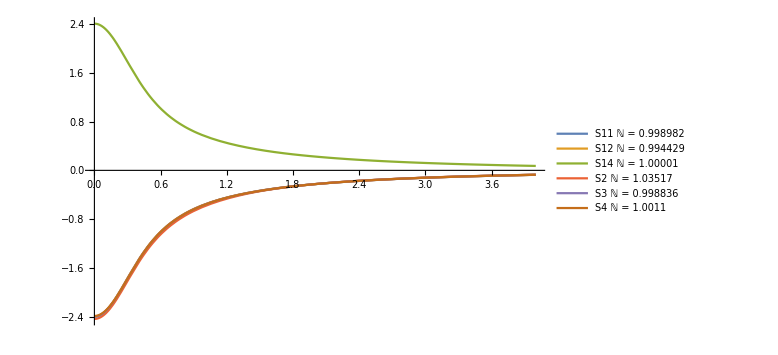

```mathematica
fls=FileNames["civ_*.dat","/home/kirscher/kette_repo/limit_cycles/systems/2/"];
data=Import[#,"Data"][[2;;]]&/@fls;
idx=(StringSplit[#,"."]&/@(StringSplit[#,"_"]&/@(StringSplit[#,"/"]&/@fls)[[All,-1]])[[All,-1]])[[All,1]];
rmax=4;
norms2=Norm2[#[[All,1]],#[[All,2]]]&/@data;
legs="S"<>ToString[#[[1]]]<>" ℕ = "<>ToString[#[[2]]]&/@Transpose[{idx,norms2}];
wfkts2=Gauss2[x,#[[All,1]],#[[All,2]]]&/@data;
Plot[wfkts2,{x,0,4},PlotLegends->legs,ImageSize->Large,PlotRange->Full]
```

```mathematica
Gauss3[ra_,rb_,co_,wi_]:=Abs[Total[Table[ co[[n]] Exp[-wi[[n]][[1]] ra^2-wi[[n]][[2]] rb^2],{n,Length[co]}]]];
Norm3[wi_]:=Table[π/16 ((wi[[m]][[1]]+wi[[n]][[1]]) (wi[[m]][[2]]+wi[[n]][[2]]))^(-1.5),{n,Length[wi]},{m,Length[wi]}];
```

```mathematica
fls=FileNames["civ_*.dat","/home/kirscher/kette_repo/limit_cycles/systems/3/"];
data=Import[#,"Data"][[2;;]]&/@fls;
databdg=Import[#,"Data"][[1]]&/@fls;
idx=(StringSplit[#,"."]&/@(StringSplit[#,"_"]&/@(StringSplit[#,"/"]&/@fls)[[All,-1]])[[All,-1]])[[All,1]];
tmpM=BinaryReadList[OpenRead["n_civ_"<>ToString[#]<>".dat",BinaryFormat->True],"Real64",ByteOrdering->$ByteOrdering]&/@idx;
dim=Sqrt[Length[tmpM[[1]]]];
norms=ArrayReshape[#,{dim,dim}]&/@tmpM;
rmax=2;
norms3=Norm3[data[[#]][[All,2;;]]]&/@Range[Length[data]];
legs="E_0("<>ToString[#[[1]]]<>")="<>ToString[#[[2]]]&/@Transpose[{idx,Flatten[databdg]}]
pltR=Range[Length[data]];
Grid[{{
Plot3D[Evaluate@Table[Gauss3[xx,yy,data[[n]][[All,1]],data[[n]][[All,2;;]]],{n,pltR}],{xx,0,rmax},{yy,0,rmax},PlotRange->Full,ImageSize->Large],
Plot[Evaluate@Table[Callout[Gauss3[x,x,data[[n]][[All,1]],data[[n]][[All,2;;]]],legs[[n]],{Scaled[n/Length[pltR]],Right},LeaderSize->{25,45°,0}],{n,pltR}],{x,0,rmax},PlotRange->Full,ImageSize->Large,PlotTheme->{"Web","LargeLabels"}]}}]
```

{E_0(12)=-8.38193,E_0(15)=-8.41677,E_0(16)=-8.47363,E_0(17)=-8.48105,E_0(19)=-8.53629,E_0(1)=-7.16027,E_0(22)=-8.53869,E_0(24)=-8.55108,E_0(30)=-8.56065,E_0(31)=-8.57196,E_0(34)=-8.57436,E_0(39)=-8.58461,E_0(46)=-8.58543,E_0(48)=-8.58702,E_0(4)=-7.92198,E_0(50)=-8.58877,E_0(5)=-8.32854}

-Graphics3D- | -Graphics-

```mathematica
did=3;
data[[did]][[All,1]].norms[[did]].data[[did]][[All,1]]//MatrixForm
data[[did]][[All,1]]//MatrixForm
```

1.00004

(-2.3917
0.26648
0.58441
0.14576
-0.24364
0.66255
0.231
-0.27262
0.27589
0.15847
0.70578
0.14568
0.016628
0.33304
-1.889
0.48344
-0.0038779
0.0030711
0.00060987
0.015295
0.0007349
0.00066138
-0.0045538
0.0042447
2.6593
-0.1022
-1.6162
-0.19111
-0.21554
-5.0974
2.6694
0.52404
3.1748
-1.436
-0.43355
-0.2808
0.0078704
-0.26459
-1.1892
-0.2101
0.0025565
0.026431
0.20904
0.0072458
-0.0062514
0.066631
-0.092481
-0.059971)

```mathematica
noRGM=norms[[did]];
noA=Norm3[data[[did]][[All,2;;]]];
noA/noRGM//MatrixForm
```

(0.335735 | 0.347741 | 0.349796 | 0.351199 | 0.317925 | 0.333097 | 0.338782 | 0.339819 | 0.32493 | 0.337088 | 0.339177 | 0.340605 | 0.314206 | 0.329405 | 0.335112 | 0.336154 | 0.317491 | 0.32971 | 0.331816 | 0.333256 | 0.310191 | 0.325407 | 0.331133 | 0.332179 | -0.37201 | -0.377388 | -0.387542 | -0.392314 | -0.322328 | -0.370467 | -0.377081 | -0.384965 | -0.348901 | -0.353877 | -0.363274 | -0.367689 | -0.284102 | -0.325224 | -0.33087 | -0.337599 | -0.318588 | -0.323041 | -0.331448 | -0.335398 | -0.279983 | -0.320353 | -0.325895 | -0.3325
0.347741 | 0.436975 | 0.454216 | 0.465796 | 0.232674 | 0.330977 | 0.398491 | 0.413264 | 0.267494 | 0.375995 | 0.404112 | 0.424993 | 0.199515 | 0.287547 | 0.359999 | 0.377629 | 0.182922 | 0.270214 | 0.302843 | 0.33167 | 0.159588 | 0.223095 | 0.289467 | 0.308491 | -0.842547 | -1.02566 | -1.63708 | -2.18032 | -0.275776 | -0.880062 | -1.16258 | -1.77888 | -0.521802 | -0.628357 | -0.982154 | -1.29497 | -0.103301 | -0.237124 | -0.296652 | -0.423793 | -0.180863 | -0.208961 | -0.300206 | -0.379276 | -0.0879065 | -0.184465 | -0.226785 | -0.316545
0.349796 | 0.454216 | 0.473464 | 0.485426 | 0.217088 | 0.330293 | 0.422106 | 0.44268 | 0.25416 | 0.390702 | 0.430011 | 0.458664 | 0.177419 | 0.271108 | 0.37422 | 0.402788 | 0.146255 | 0.227682 | 0.275211 | 0.329763 | 0.129603 | 0.174355 | 0.250778 | 0.282406 | -1.05168 | -1.38925 | -2.94033 | -5.14116 | -0.268979 | -1.14503 | -1.74346 | -3.71054 | -0.593173 | -0.771434 | -1.58355 | -2.72791 | -0.0816702 | -0.201587 | -0.277136 | -0.515234 | -0.135813 | -0.162227 | -0.276753 | -0.431094 | -0.0658282 | -0.133321 | -0.174394 | -0.301023
0.351199 | 0.465796 | 0.485426 | 0.495979 | 0.206353 | 0.329713 | 0.443417 | 0.468272 | 0.244275 | 0.404009 | 0.45319 | 0.485827 | 0.162129 | 0.255876 | 0.391086 | 0.433316 | 0.118613 | 0.168431 | 0.218946 | 0.323615 | 0.109094 | 0.126422 | 0.176874 | 0.214874 | -1.2563 | -1.79854 | -5.48732 | -17.1701 | -0.264502 | -1.43024 | -2.5534 | -9.41327 | -0.661155 | -0.928012 | -2.72278 | -8.35739 | -0.0682848 | -0.168247 | -0.253865 | -0.738361 | -0.0985104 | -0.118575 | -0.240662 | -0.589423 | -0.0524019 | -0.0883252 | -0.116874 | -0.2675
0.317925 | 0.232674 | 0.217088 | 0.206353 | 0.422141 | 0.335152 | 0.286823 | 0.27693 | 0.388586 | 0.302254 | 0.283083 | 0.269185 | 0.44095 | 0.364532 | 0.317092 | 0.306925 | 0.436207 | 0.366724 | 0.348271 | 0.334105 | 0.459345 | 0.398084 | 0.354811 | 0.34498 | -0.167544 | -0.152885 | -0.128721 | -0.118742 | -0.413807 | -0.168338 | -0.149564 | -0.129893 | -0.240225 | -0.216322 | -0.17718 | -0.161132 | -1.23642 | -0.41697 | -0.357089 | -0.295233 | -0.507863 | -0.448552 | -0.35238 | -0.313382 | -1.47772 | -0.488001 | -0.416056 | -0.341867
0.333097 | 0.330977 | 0.330293 | 0.329713 | 0.335152 | 0.333386 | 0.331895 | 0.331506 | 0.334553 | 0.332437 | 0.331754 | 0.331175 | 0.336031 | 0.334266 | 0.332776 | 0.332387 | 0.336743 | 0.334631 | 0.33395 | 0.333372 | 0.337468 | 0.335707 | 0.334219 | 0.33383 | -0.328145 | -0.327021 | -0.324405 | -0.322888 | -0.334358 | -0.327767 | -0.326175 | -0.323841 | -0.330563 | -0.329428 | -0.326789 | -0.325258 | -0.342584 | -0.335795 | -0.334155 | -0.331751 | -0.337936 | -0.336771 | -0.334059 | -0.332487 | -0.344597 | -0.33776 | -0.336108 | -0.333686
0.338782 | 0.398491 | 0.422106 | 0.443417 | 0.286823 | 0.331895 | 0.386312 | 0.403582 | 0.300138 | 0.364547 | 0.392628 | 0.419507 | 0.257022 | 0.300661 | 0.35787 | 0.377247 | 0.210038 | 0.265426 | 0.296101 | 0.331032 | 0.194342 | 0.227657 | 0.27985 | 0.30049 | -0.524038 | -0.600084 | -0.900629 | -1.25232 | -0.311173 | -0.557944 | -0.694334 | -1.06959 | -0.431488 | -0.492096 | -0.731018 | -1.00984 | -0.153533 | -0.247388 | -0.298194 | -0.435935 | -0.190996 | -0.212572 | -0.296305 | -0.392358 | -0.121045 | -0.185245 | -0.219639 | -0.312162
0.339819 | 0.413264 | 0.44268 | 0.468272 | 0.27693 | 0.331506 | 0.403582 | 0.427224 | 0.292506 | 0.374114 | 0.412243 | 0.448816 | 0.23907 | 0.290349 | 0.368139 | 0.396895 | 0.172821 | 0.229236 | 0.270357 | 0.328964 | 0.156747 | 0.184765 | 0.243526 | 0.273835 | -0.586793 | -0.704415 | -1.28321 | -2.27475 | -0.307245 | -0.641191 | -0.87249 | -1.74292 | -0.462625 | -0.551967 | -0.989834 | -1.73683 | -0.126399 | -0.220617 | -0.283653 | -0.514386 | -0.153593 | -0.174986 | -0.276585 | -0.443955 | -0.0909779 | -0.142554 | -0.176298 | -0.297366
0.32493 | 0.267494 | 0.25416 | 0.244275 | 0.388586 | 0.334553 | 0.300138 | 0.292506 | 0.368504 | 0.311607 | 0.29727 | 0.286358 | 0.405877 | 0.355283 | 0.32138 | 0.313685 | 0.408903 | 0.358659 | 0.344812 | 0.333933 | 0.426475 | 0.381827 | 0.349847 | 0.342352 | -0.214555 | -0.199767 | -0.172986 | -0.16093 | -0.373397 | -0.212571 | -0.193415 | -0.171511 | -0.267793 | -0.248072 | -0.212453 | -0.196465 | -0.744515 | -0.392014 | -0.350771 | -0.303924 | -0.451732 | -0.414538 | -0.347689 | -0.317847 | -0.847267 | -0.441072 | -0.393672 | -0.339886
0.337088 | 0.375995 | 0.390702 | 0.404009 | 0.302254 | 0.332437 | 0.364547 | 0.374114 | 0.311607 | 0.35213 | 0.36806 | 0.38279 | 0.283839 | 0.313838 | 0.346751 | 0.356772 | 0.259615 | 0.299184 | 0.316026 | 0.332348 | 0.247629 | 0.275696 | 0.308401 | 0.318804 | -0.44543 | -0.481578 | -0.594577 | -0.688806 | -0.317787 | -0.460448 | -0.518901 | -0.638433 | -0.391801 | -0.422851 | -0.51981 | -0.600571 | -0.202557 | -0.281821 | -0.314039 | -0.379596 | -0.24384 | -0.261061 | -0.314577 | -0.358917 | -0.177147 | -0.242825 | -0.26944 | -0.323497
0.339177 | 0.404112 | 0.430011 | 0.45319 | 0.283083 | 0.331754 | 0.392628 | 0.412243 | 0.29727 | 0.36806 | 0.3998 | 0.430336 | 0.250247 | 0.296902 | 0.36147 | 0.38407 | 0.196171 | 0.253291 | 0.288041 | 0.330442 | 0.180098 | 0.212386 | 0.268388 | 0.292526 | -0.546569 | -0.636621 | -1.02096 | -1.5307 | -0.309676 | -0.587356 | -0.75429 | -1.26464 | -0.442771 | -0.513252 | -0.813143 | -1.20961 | -0.142762 | -0.237547 | -0.293097 | -0.459759 | -0.176856 | -0.198694 | -0.289729 | -0.407394 | -0.108939 | -0.169258 | -0.20412 | -0.307555
0.340605 | 0.424993 | 0.458664 | 0.485827 | 0.269185 | 0.331175 | 0.419507 | 0.448816 | 0.286358 | 0.38279 | 0.430336 | 0.474311 | 0.224573 | 0.280876 | 0.379144 | 0.418524 | 0.140502 | 0.184746 | 0.229504 | 0.324296 | 0.125712 | 0.141737 | 0.188043 | 0.222886 | -0.645056 | -0.809964 | -1.84371 | -4.8924 | -0.304334 | -0.723197 | -1.0796 | -3.08576 | -0.491236 | -0.611849 | -1.36374 | -3.56866 | -0.107124 | -0.196142 | -0.268136 | -0.655039 | -0.122144 | -0.140911 | -0.251509 | -0.555408 | -0.0701994 | -0.105529 | -0.132901 | -0.273131
0.314206 | 0.199515 | 0.177419 | 0.162129 | 0.44095 | 0.336031 | 0.257022 | 0.23907 | 0.405877 | 0.283839 | 0.250247 | 0.224573 | 0.463358 | 0.381763 | 0.303909 | 0.283957 | 0.468948 | 0.395657 | 0.364174 | 0.335054 | 0.483616 | 0.437276 | 0.377089 | 0.35845 | -0.135736 | -0.119101 | -0.0922178 | -0.0813588 | -0.434749 | -0.133371 | -0.111868 | -0.0898374 | -0.209034 | -0.178207 | -0.129139 | -0.109672 | -2.32422 | -0.497199 | -0.378874 | -0.26236 | -0.719368 | -0.583506 | -0.373094 | -0.29254 | -3.38631 | -0.692795 | -0.520546 | -0.351963
0.329405 | 0.287547 | 0.271108 | 0.255876 | 0.364532 | 0.334266 | 0.300661 | 0.290349 | 0.355283 | 0.313838 | 0.296902 | 0.280876 | 0.381763 | 0.352827 | 0.319635 | 0.309227 | 0.402676 | 0.366393 | 0.350289 | 0.334322 | 0.413033 | 0.388094 | 0.35757 | 0.347561 | -0.251777 | -0.235059 | -0.19772 | -0.177015 | -0.35056 | -0.244567 | -0.220779 | -0.187397 | -0.284023 | -0.264543 | -0.221097 | -0.197049 | -0.59242 | -0.397575 | -0.354249 | -0.293806 | -0.467912 | -0.432364 | -0.353468 | -0.310077 | -0.706982 | -0.469517 | -0.416846 | -0.343487
0.335112 | 0.359999 | 0.37422 | 0.391086 | 0.317092 | 0.332776 | 0.35787 | 0.368139 | 0.32138 | 0.346751 | 0.36147 | 0.379144 | 0.303909 | 0.319635 | 0.34516 | 0.355741 | 0.272354 | 0.29741 | 0.312731 | 0.331984 | 0.263171 | 0.278135 | 0.303508 | 0.314455 | -0.391571 | -0.413481 | -0.495527 | -0.58564 | -0.326004 | -0.40279 | -0.442088 | -0.543817 | -0.367508 | -0.387813 | -0.463809 | -0.547227 | -0.237955 | -0.28941 | -0.31565 | -0.383355 | -0.252752 | -0.265496 | -0.313039 | -0.365 | -0.203515 | -0.245253 | -0.266493 | -0.321191
0.336154 | 0.377629 | 0.402788 | 0.433316 | 0.306925 | 0.332387 | 0.377247 | 0.396895 | 0.313685 | 0.356772 | 0.38407 | 0.418524 | 0.283957 | 0.309227 | 0.355741 | 0.377007 | 0.22057 | 0.258022 | 0.28648 | 0.329917 | 0.204854 | 0.224126 | 0.265338 | 0.28741 | -0.43614 | -0.481147 | -0.689968 | -1.02414 | -0.321844 | -0.459676 | -0.548057 | -0.858976 | -0.393222 | -0.433021 | -0.617433 | -0.912032 | -0.188512 | -0.256754 | -0.300048 | -0.450669 | -0.198656 | -0.215375 | -0.291931 | -0.412301 | -0.13957 | -0.183349 | -0.210895 | -0.305867
0.317491 | 0.182922 | 0.146255 | 0.118613 | 0.436207 | 0.336743 | 0.210038 | 0.172821 | 0.408903 | 0.259615 | 0.196171 | 0.140502 | 0.468948 | 0.402676 | 0.272354 | 0.22057 | 0.495275 | 0.47192 | 0.438151 | 0.343727 | 0.498329 | 0.493124 | 0.468473 | 0.443194 | -0.129758 | -0.107252 | -0.0690947 | -0.0532871 | -0.411035 | -0.119903 | -0.0905873 | -0.0596038 | -0.190493 | -0.151118 | -0.0860128 | -0.0600633 | -4.13552 | -0.740285 | -0.44513 | -0.167724 | -1.84809 | -1.30594 | -0.47742 | -0.196717 | -14.9302 | -2.43395 | -1.38076 | -0.424983
0.32971 | 0.270214 | 0.227682 | 0.168431 | 0.366724 | 0.334631 | 0.265426 | 0.229236 | 0.358659 | 0.299184 | 0.253291 | 0.184746 | 0.395657 | 0.366393 | 0.29741 | 0.258022 | 0.47192 | 0.448287 | 0.419713 | 0.342161 | 0.483777 | 0.476678 | 0.451873 | 0.42927 | -0.238693 | -0.212089 | -0.139396 | -0.0898628 | -0.348706 | -0.223485 | -0.181134 | -0.108128 | -0.269044 | -0.238034 | -0.153593 | -0.0964691 | -0.864194 | -0.512682 | -0.396377 | -0.201908 | -0.881113 | -0.757626 | -0.429221 | -0.218745 | -2.05609 | -1.16907 | -0.879203 | -0.40357
0.331816 | 0.302843 | 0.275211 | 0.218946 | 0.348271 | 0.33395 | 0.296101 | 0.270357 | 0.344812 | 0.316026 | 0.288041 | 0.229504 | 0.364174 | 0.350289 | 0.312731 | 0.28648 | 0.438151 | 0.419713 | 0.398524 | 0.340277 | 0.45713 | 0.450494 | 0.429318 | 0.411058 | -0.285423 | -0.267832 | -0.204021 | -0.138327 | -0.33962 | -0.275128 | -0.243289 | -0.164751 | -0.301105 | -0.282301 | -0.214143 | -0.144105 | -0.531279 | -0.422189 | -0.368625 | -0.237733 | -0.581378 | -0.540418 | -0.393122 | -0.244615 | -0.922271 | -0.720369 | -0.621719 | -0.382756
0.333256 | 0.33167 | 0.329763 | 0.323615 | 0.334105 | 0.333372 | 0.331032 | 0.328964 | 0.333933 | 0.332348 | 0.330442 | 0.324296 | 0.335054 | 0.334322 | 0.331984 | 0.329917 | 0.343727 | 0.342161 | 0.340277 | 0.334188 | 0.348647 | 0.347929 | 0.345634 | 0.343602 | -0.330595 | -0.329342 | -0.322824 | -0.308835 | -0.333638 | -0.329842 | -0.327214 | -0.315887 | -0.331504 | -0.330247 | -0.323707 | -0.30967 | -0.342217 | -0.338303 | -0.335591 | -0.323909 | -0.345955 | -0.344631 | -0.337742 | -0.322958 | -0.357155 | -0.353033 | -0.350177 | -0.337875
0.310191 | 0.159588 | 0.129603 | 0.109094 | 0.459345 | 0.337468 | 0.194342 | 0.156747 | 0.426475 | 0.247629 | 0.180098 | 0.125712 | 0.483616 | 0.413033 | 0.263171 | 0.204854 | 0.498329 | 0.483777 | 0.45713 | 0.348647 | 0.499699 | 0.497799 | 0.485922 | 0.469849 | -0.104796 | -0.0867555 | -0.058495 | -0.0475082 | -0.458068 | -0.0983403 | -0.0750195 | -0.0520449 | -0.169963 | -0.131613 | -0.0738036 | -0.052535 | -8.2321 | -0.847178 | -0.466737 | -0.148573 | -2.55237 | -1.68747 | -0.514691 | -0.171104 | -40.622 | -3.74505 | -1.91779 | -0.457962
0.325407 | 0.223095 | 0.174355 | 0.126422 | 0.398084 | 0.335707 | 0.227657 | 0.184765 | 0.381827 | 0.275696 | 0.212386 | 0.141737 | 0.437276 | 0.388094 | 0.278135 | 0.224126 | 0.493124 | 0.476678 | 0.450494 | 0.347929 | 0.497799 | 0.495126 | 0.482226 | 0.466082 | -0.179121 | -0.149977 | -0.0893406 | -0.0592025 | -0.368587 | -0.163322 | -0.12235 | -0.0699139 | -0.226047 | -0.186157 | -0.104137 | -0.064275 | -1.90526 | -0.665893 | -0.435242 | -0.162923 | -1.57788 | -1.20686 | -0.486053 | -0.179695 | -7.43645 | -2.40128 | -1.48728 | -0.446373
0.331133 | 0.289467 | 0.250778 | 0.176874 | 0.354811 | 0.334219 | 0.27985 | 0.243526 | 0.349847 | 0.308401 | 0.268388 | 0.188043 | 0.377089 | 0.35757 | 0.303508 | 0.265338 | 0.468473 | 0.451873 | 0.429318 | 0.345634 | 0.485922 | 0.482226 | 0.46805 | 0.452499 | -0.266938 | -0.244077 | -0.167674 | -0.0993022 | -0.342502 | -0.253491 | -0.213511 | -0.125485 | -0.288114 | -0.262947 | -0.17898 | -0.104154 | -0.661049 | -0.470543 | -0.385936 | -0.203326 | -0.764141 | -0.685474 | -0.427166 | -0.206445 | -1.58142 | -1.09023 | -0.874119 | -0.415908
0.332179 | 0.308491 | 0.282406 | 0.214874 | 0.34498 | 0.33383 | 0.30049 | 0.273835 | 0.342352 | 0.318804 | 0.292526 | 0.222886 | 0.35845 | 0.347561 | 0.314455 | 0.28741 | 0.443194 | 0.42927 | 0.411058 | 0.343602 | 0.469849 | 0.466082 | 0.452499 | 0.438373 | -0.294719 | -0.279268 | -0.216237 | -0.137048 | -0.338083 | -0.285559 | -0.256093 | -0.170398 | -0.307174 | -0.290909 | -0.22459 | -0.141395 | -0.494281 | -0.412009 | -0.36603 | -0.233363 | -0.565748 | -0.532231 | -0.396485 | -0.229327 | -0.90542 | -0.743199 | -0.652943 | -0.394993
-0.37201 | -0.842547 | -1.05168 | -1.2563 | -0.167544 | -0.328145 | -0.524038 | -0.586793 | -0.214555 | -0.44543 | -0.546569 | -0.645056 | -0.135736 | -0.251777 | -0.391571 | -0.43614 | -0.129758 | -0.238693 | -0.285423 | -0.330595 | -0.104796 | -0.179121 | -0.266938 | -0.294719 | 0.401577 | 0.411768 | 0.431123 | 0.440166 | 0.315221 | 0.402953 | 0.416374 | 0.432471 | 0.36809 | 0.380095 | 0.403782 | 0.415277 | 0.220239 | 0.307106 | 0.324949 | 0.348807 | 0.284894 | 0.297981 | 0.326284 | 0.341402 | 0.205931 | 0.288166 | 0.305871 | 0.33004
-0.377388 | -1.02566 | -1.38925 | -1.79854 | -0.152885 | -0.327021 | -0.600084 | -0.704415 | -0.199767 | -0.481578 | -0.636621 | -0.809964 | -0.119101 | -0.235059 | -0.413481 | -0.481147 | -0.107252 | -0.212089 | -0.267832 | -0.329342 | -0.0867555 | -0.149977 | -0.244077 | -0.279268 | 0.411768 | 0.423634 | 0.446011 | 0.456293 | 0.313002 | 0.414173 | 0.429955 | 0.448703 | 0.374983 | 0.38968 | 0.418919 | 0.433095 | 0.201577 | 0.298885 | 0.322061 | 0.354773 | 0.269796 | 0.286001 | 0.323482 | 0.344867 | 0.184334 | 0.272757 | 0.295396 | 0.328607
-0.387542 | -1.63708 | -2.94033 | -5.48732 | -0.128721 | -0.324405 | -0.900629 | -1.28321 | -0.172986 | -0.594577 | -1.02096 | -1.84371 | -0.0922178 | -0.19772 | -0.495527 | -0.689968 | -0.0690947 | -0.139396 | -0.204021 | -0.322824 | -0.058495 | -0.0893406 | -0.167674 | -0.216237 | 0.431123 | 0.446011 | 0.47291 | 0.484139 | 0.308978 | 0.436039 | 0.456024 | 0.478315 | 0.390074 | 0.41089 | 0.452161 | 0.471067 | 0.164961 | 0.273815 | 0.312259 | 0.377785 | 0.224656 | 0.246728 | 0.312074 | 0.360605 | 0.141924 | 0.222308 | 0.255699 | 0.321817
-0.392314 | -2.18032 | -5.14116 | -17.1701 | -0.118742 | -0.322888 | -1.25232 | -2.27475 | -0.16093 | -0.688806 | -1.5307 | -4.8924 | -0.0813588 | -0.177015 | -0.58564 | -1.02414 | -0.0532871 | -0.0898628 | -0.138327 | -0.308835 | -0.0475082 | -0.0592025 | -0.0993022 | -0.137048 | 0.440166 | 0.456293 | 0.484139 | 0.494365 | 0.307161 | 0.446465 | 0.468011 | 0.490249 | 0.398279 | 0.422481 | 0.469395 | 0.488699 | 0.147353 | 0.253632 | 0.303034 | 0.404231 | 0.189797 | 0.212111 | 0.297592 | 0.38551 | 0.121651 | 0.178459 | 0.212035 | 0.310194
-0.322328 | -0.275776 | -0.268979 | -0.264502 | -0.413807 | -0.334358 | -0.311173 | -0.307245 | -0.373397 | -0.317787 | -0.309676 | -0.304334 | -0.434749 | -0.35056 | -0.326004 | -0.321844 | -0.411035 | -0.348706 | -0.33962 | -0.333638 | -0.458068 | -0.368587 | -0.342502 | -0.338083 | 0.315221 | 0.313002 | 0.308978 | 0.307161 | 0.339203 | 0.316096 | 0.313387 | 0.310278 | 0.325986 | 0.323773 | 0.319753 | 0.317935 | 0.359657 | 0.337153 | 0.334475 | 0.331393 | 0.340357 | 0.338173 | 0.334197 | 0.332395 | 0.361862 | 0.339456 | 0.336786 | 0.333712
-0.370467 | -0.880062 | -1.14503 | -1.43024 | -0.168338 | -0.327767 | -0.557944 | -0.641191 | -0.212571 | -0.460448 | -0.587356 | -0.723197 | -0.133371 | -0.244567 | -0.40279 | -0.459676 | -0.119903 | -0.223485 | -0.275128 | -0.329842 | -0.0983403 | -0.163322 | -0.253491 | -0.285559 | 0.402953 | 0.414173 | 0.436039 | 0.446465 | 0.316096 | 0.405423 | 0.420437 | 0.438861 | 0.370112 | 0.383372 | 0.410339 | 0.423766 | 0.215256 | 0.302952 | 0.323404 | 0.352156 | 0.277157 | 0.291615 | 0.324691 | 0.343397 | 0.198432 | 0.279886 | 0.300023 | 0.329195
-0.377081 | -1.16258 | -1.74346 | -2.5534 | -0.149564 | -0.326175 | -0.694334 | -0.87249 | -0.193415 | -0.518901 | -0.75429 | -1.0796 | -0.111868 | -0.220779 | -0.442088 | -0.548057 | -0.0905873 | -0.181134 | -0.243289 | -0.327214 | -0.0750195 | -0.12235 | -0.213511 | -0.256093 | 0.416374 | 0.429955 | 0.456024 | 0.468011 | 0.313387 | 0.420437 | 0.4388 | 0.460835 | 0.379653 | 0.396834 | 0.432043 | 0.449355 | 0.189684 | 0.289434 | 0.318406 | 0.36318 | 0.252375 | 0.27111 | 0.319403 | 0.350275 | 0.168341 | 0.253413 | 0.28082 | 0.326303
-0.384965 | -1.77888 | -3.71054 | -9.41327 | -0.129893 | -0.323841 | -1.06959 | -1.74292 | -0.171511 | -0.638433 | -1.26464 | -3.08576 | -0.0898374 | -0.187397 | -0.543817 | -0.858976 | -0.0596038 | -0.108128 | -0.164751 | -0.315887 | -0.0520449 | -0.0699139 | -0.125485 | -0.170398 | 0.432471 | 0.448703 | 0.478315 | 0.490249 | 0.310278 | 0.438861 | 0.460835 | 0.485106 | 0.392813 | 0.415578 | 0.461544 | 0.48207 | 0.157937 | 0.262568 | 0.307049 | 0.39291 | 0.204471 | 0.226699 | 0.303991 | 0.374045 | 0.131048 | 0.196395 | 0.230548 | 0.31569
-0.348901 | -0.521802 | -0.593173 | -0.661155 | -0.240225 | -0.330563 | -0.431488 | -0.462625 | -0.267793 | -0.391801 | -0.442771 | -0.491236 | -0.209034 | -0.284023 | -0.367508 | -0.393222 | -0.190493 | -0.269044 | -0.301105 | -0.331504 | -0.169963 | -0.226047 | -0.288114 | -0.307174 | 0.36809 | 0.374983 | 0.390074 | 0.398279 | 0.325986 | 0.370112 | 0.379653 | 0.392813 | 0.351719 | 0.358935 | 0.374911 | 0.383703 | 0.272541 | 0.317609 | 0.328164 | 0.343268 | 0.304044 | 0.311583 | 0.328812 | 0.338628 | 0.260981 | 0.305347 | 0.315917 | 0.331169
-0.353877 | -0.628357 | -0.771434 | -0.928012 | -0.216322 | -0.329428 | -0.492096 | -0.551967 | -0.248072 | -0.422851 | -0.513252 | -0.611849 | -0.178207 | -0.264543 | -0.387813 | -0.433021 | -0.151118 | -0.238034 | -0.282301 | -0.330247 | -0.131613 | -0.186157 | -0.262947 | -0.290909 | 0.380095 | 0.38968 | 0.41089 | 0.422481 | 0.323773 | 0.383372 | 0.396834 | 0.415578 | 0.358935 | 0.369272 | 0.392647 | 0.40573 | 0.249127 | 0.30936 | 0.325281 | 0.349296 | 0.288531 | 0.299472 | 0.326015 | 0.342107 | 0.231937 | 0.289589 | 0.305394 | 0.329737
-0.363274 | -0.982154 | -1.58355 | -2.72278 | -0.17718 | -0.326789 | -0.731018 | -0.989834 | -0.212453 | -0.51981 | -0.813143 | -1.36374 | -0.129139 | -0.221097 | -0.463809 | -0.617433 | -0.0860128 | -0.153593 | -0.214143 | -0.323707 | -0.0738036 | -0.104137 | -0.17898 | -0.22459 | 0.403782 | 0.418919 | 0.452161 | 0.469395 | 0.319753 | 0.410339 | 0.432043 | 0.461544 | 0.374911 | 0.392647 | 0.433857 | 0.456617 | 0.199393 | 0.283982 | 0.315486 | 0.372658 | 0.240815 | 0.259072 | 0.314614 | 0.357932 | 0.168943 | 0.236546 | 0.265009 | 0.322952
-0.367689 | -1.29497 | -2.72791 | -8.35739 | -0.161132 | -0.325258 | -1.00984 | -1.73683 | -0.196465 | -0.600571 | -1.20961 | -3.56866 | -0.109672 | -0.197049 | -0.547227 | -0.912032 | -0.0600633 | -0.0964691 | -0.144105 | -0.30967 | -0.052535 | -0.064275 | -0.104154 | -0.141395 | 0.415277 | 0.433095 | 0.471067 | 0.488699 | 0.317935 | 0.423766 | 0.449355 | 0.48207 | 0.383703 | 0.40573 | 0.456617 | 0.482459 | 0.173715 | 0.26331 | 0.306253 | 0.399726 | 0.20265 | 0.222611 | 0.300117 | 0.383057 | 0.136248 | 0.188731 | 0.219705 | 0.31133
-0.284102 | -0.103301 | -0.0816702 | -0.0682848 | -1.23642 | -0.342584 | -0.153533 | -0.126399 | -0.744515 | -0.202557 | -0.142762 | -0.107124 | -2.32422 | -0.59242 | -0.237955 | -0.188512 | -4.13552 | -0.864194 | -0.531279 | -0.342217 | -8.2321 | -1.90526 | -0.661049 | -0.494281 | 0.220239 | 0.201577 | 0.164961 | 0.147353 | 0.359657 | 0.215256 | 0.189684 | 0.157937 | 0.272541 | 0.249127 | 0.199393 | 0.173715 | 0.472908 | 0.385981 | 0.352224 | 0.292497 | 0.424784 | 0.406664 | 0.351566 | 0.309687 | 0.484357 | 0.424855 | 0.397622 | 0.342921
-0.325224 | -0.237124 | -0.201587 | -0.168247 | -0.41697 | -0.335795 | -0.247388 | -0.220617 | -0.392014 | -0.281821 | -0.237547 | -0.196142 | -0.497199 | -0.397575 | -0.28941 | -0.256754 | -0.740285 | -0.512682 | -0.422189 | -0.338303 | -0.847178 | -0.665893 | -0.470543 | -0.412009 | 0.307106 | 0.298885 | 0.273815 | 0.253632 | 0.337153 | 0.302952 | 0.289434 | 0.262568 | 0.317609 | 0.30936 | 0.283982 | 0.26331 | 0.385981 | 0.354628 | 0.341398 | 0.313606 | 0.37432 | 0.366764 | 0.342268 | 0.320849 | 0.406381 | 0.377773 | 0.365328 | 0.338451
-0.33087 | -0.296652 | -0.277136 | -0.253865 | -0.357089 | -0.334155 | -0.298194 | -0.283653 | -0.350771 | -0.314039 | -0.293097 | -0.268136 | -0.378874 | -0.354249 | -0.31565 | -0.300048 | -0.44513 | -0.396377 | -0.368625 | -0.335591 | -0.466737 | -0.435242 | -0.385936 | -0.36603 | 0.324949 | 0.322061 | 0.312259 | 0.303034 | 0.334475 | 0.323404 | 0.318406 | 0.307049 | 0.328164 | 0.325281 | 0.315486 | 0.306253 | 0.352224 | 0.341398 | 0.336474 | 0.325195 | 0.34948 | 0.346672 | 0.337062 | 0.327904 | 0.362177 | 0.351575 | 0.346731 | 0.335586
-0.337599 | -0.423793 | -0.515234 | -0.738361 | -0.295233 | -0.331751 | -0.435935 | -0.514386 | -0.303924 | -0.379596 | -0.459759 | -0.655039 | -0.26236 | -0.293806 | -0.383355 | -0.450669 | -0.167724 | -0.201908 | -0.237733 | -0.323909 | -0.148573 | -0.162923 | -0.203326 | -0.233363 | 0.348807 | 0.354773 | 0.377785 | 0.404231 | 0.331393 | 0.352156 | 0.36318 | 0.39291 | 0.343268 | 0.349296 | 0.372658 | 0.399726 | 0.292497 | 0.313606 | 0.325195 | 0.357925 | 0.290834 | 0.296958 | 0.321736 | 0.352764 | 0.260196 | 0.280328 | 0.291683 | 0.32503
-0.318588 | -0.180863 | -0.135813 | -0.0985104 | -0.507863 | -0.337936 | -0.190996 | -0.153593 | -0.451732 | -0.24384 | -0.176856 | -0.122144 | -0.719368 | -0.467912 | -0.252752 | -0.198656 | -1.84809 | -0.881113 | -0.581378 | -0.345955 | -2.55237 | -1.57788 | -0.764141 | -0.565748 | 0.284894 | 0.269796 | 0.224656 | 0.189797 | 0.340357 | 0.277157 | 0.252375 | 0.204471 | 0.304044 | 0.288531 | 0.240815 | 0.20265 | 0.424784 | 0.37432 | 0.34948 | 0.290834 | 0.410448 | 0.398251 | 0.352498 | 0.30433 | 0.455036 | 0.418599 | 0.398595 | 0.345226
-0.323041 | -0.208961 | -0.162227 | -0.118575 | -0.448552 | -0.336771 | -0.212572 | -0.174986 | -0.414538 | -0.261061 | -0.198694 | -0.140911 | -0.583506 | -0.432364 | -0.265496 | -0.215375 | -1.30594 | -0.757626 | -0.540418 | -0.344631 | -1.68747 | -1.20686 | -0.685474 | -0.532231 | 0.297981 | 0.286001 | 0.246728 | 0.212111 | 0.338173 | 0.291615 | 0.27111 | 0.226699 | 0.311583 | 0.299472 | 0.259072 | 0.222611 | 0.406664 | 0.366764 | 0.346672 | 0.296958 | 0.398251 | 0.388154 | 0.349789 | 0.307864 | 0.438308 | 0.40693 | 0.389885 | 0.343819
-0.331448 | -0.300206 | -0.276753 | -0.240662 | -0.35238 | -0.334059 | -0.296305 | -0.276585 | -0.347689 | -0.314577 | -0.289729 | -0.251509 | -0.373094 | -0.353468 | -0.313039 | -0.291931 | -0.47742 | -0.429221 | -0.393122 | -0.337742 | -0.514691 | -0.486053 | -0.427166 | -0.396485 | 0.326284 | 0.323482 | 0.312074 | 0.297592 | 0.334197 | 0.324691 | 0.319403 | 0.303991 | 0.328812 | 0.326015 | 0.314614 | 0.300117 | 0.351566 | 0.342268 | 0.337062 | 0.321736 | 0.352498 | 0.349789 | 0.338643 | 0.324236 | 0.366236 | 0.357242 | 0.352174 | 0.33713
-0.335398 | -0.379276 | -0.431094 | -0.589423 | -0.313382 | -0.332487 | -0.392358 | -0.443955 | -0.317847 | -0.358917 | -0.407394 | -0.555408 | -0.29254 | -0.310077 | -0.365 | -0.412301 | -0.196717 | -0.218745 | -0.244615 | -0.322958 | -0.171104 | -0.179695 | -0.206445 | -0.229327 | 0.341402 | 0.344867 | 0.360605 | 0.38551 | 0.332395 | 0.343397 | 0.350275 | 0.374045 | 0.338628 | 0.342107 | 0.357932 | 0.383057 | 0.309687 | 0.320849 | 0.327904 | 0.352764 | 0.30433 | 0.307864 | 0.324236 | 0.351282 | 0.282315 | 0.293274 | 0.300289 | 0.325593
-0.279983 | -0.0879065 | -0.0658282 | -0.0524019 | -1.47772 | -0.344597 | -0.121045 | -0.0909779 | -0.847267 | -0.177147 | -0.108939 | -0.0701994 | -3.38631 | -0.706982 | -0.203515 | -0.13957 | -14.9302 | -2.05609 | -0.922271 | -0.357155 | -40.622 | -7.43645 | -1.58142 | -0.90542 | 0.205931 | 0.184334 | 0.141924 | 0.121651 | 0.361862 | 0.198432 | 0.168341 | 0.131048 | 0.260981 | 0.231937 | 0.168943 | 0.136248 | 0.484357 | 0.406381 | 0.362177 | 0.260196 | 0.455036 | 0.438308 | 0.366236 | 0.282315 | 0.494708 | 0.461531 | 0.436662 | 0.354207
-0.320353 | -0.184465 | -0.133321 | -0.0883252 | -0.488001 | -0.33776 | -0.185245 | -0.142554 | -0.441072 | -0.242825 | -0.169258 | -0.105529 | -0.692795 | -0.469517 | -0.245253 | -0.183349 | -2.43395 | -1.16907 | -0.720369 | -0.353033 | -3.74505 | -2.40128 | -1.09023 | -0.743199 | 0.288166 | 0.272757 | 0.222308 | 0.178459 | 0.339456 | 0.279886 | 0.253413 | 0.196395 | 0.305347 | 0.289589 | 0.236546 | 0.188731 | 0.424855 | 0.377773 | 0.351575 | 0.280328 | 0.418599 | 0.40693 | 0.357242 | 0.293274 | 0.461531 | 0.431382 | 0.41224 | 0.349826
-0.325895 | -0.226785 | -0.174394 | -0.116874 | -0.416056 | -0.336108 | -0.219639 | -0.176298 | -0.393672 | -0.26944 | -0.20412 | -0.132901 | -0.520546 | -0.416846 | -0.266493 | -0.210895 | -1.38076 | -0.879203 | -0.621719 | -0.350177 | -1.91779 | -1.48728 | -0.874119 | -0.652943 | 0.305871 | 0.295396 | 0.255699 | 0.212035 | 0.336786 | 0.300023 | 0.28082 | 0.230548 | 0.315917 | 0.305394 | 0.265009 | 0.219705 | 0.397622 | 0.365328 | 0.346731 | 0.291683 | 0.398595 | 0.389885 | 0.352174 | 0.300289 | 0.436662 | 0.41224 | 0.397082 | 0.34701
-0.3325 | -0.316545 | -0.301023 | -0.2675 | -0.341867 | -0.333686 | -0.312162 | -0.297366 | -0.339886 | -0.323497 | -0.307555 | -0.273131 | -0.351963 | -0.343487 | -0.321191 | -0.305867 | -0.424983 | -0.40357 | -0.382756 | -0.337875 | -0.457962 | -0.446373 | -0.415908 | -0.394993 | 0.33004 | 0.328607 | 0.321817 | 0.310194 | 0.333712 | 0.329195 | 0.326303 | 0.31569 | 0.331169 | 0.329737 | 0.322952 | 0.31133 | 0.342921 | 0.338451 | 0.335586 | 0.32503 | 0.345226 | 0.343819 | 0.33713 | 0.325593 | 0.354207 | 0.349826 | 0.34701 | 0.336595)

```mathematica
cc=3;
wis=data[[cc]][[All,2;;]];
cofs=data[[cc]][[All,1]];
nom=norms[[cc]];
cofs.nom.cofs
Norm3[cofs,wis,nom]
```

1.00004

Norm3[{-2.3917,0.26648,0.58441,0.14576,-0.24364,0.66255,0.231,-0.27262,0.27589,0.15847,0.70578,0.14568,0.016628,0.33304,-1.889,0.48344,-0.0038779,0.0030711,0.00060987,0.015295,0.0007349,0.00066138,-0.0045538,0.0042447,2.6593,-0.1022,-1.6162,-0.19111,-0.21554,-5.0974,2.6694,0.52404,3.1748,-1.436,-0.43355,-0.2808,0.0078704,-0.26459,-1.1892,-0.2101,0.0025565,0.026431,0.20904,0.0072458,-0.0062514,0.066631,-0.092481,-0.059971},{{7.6335,5.781},{7.6335,0.87055},{7.6335,0.39044},{7.6335,0.095546},{1.9236,13.254},{1.9236,1.9994},{1.9236,0.47959},{1.9236,0.25765},{1.9187,5.781},{1.9187,0.87055},{1.9187,0.39044},{1.9187,0.095546},{0.8935,13.254},{0.8935,1.9994},{0.8935,0.47959},{0.8935,0.25765},{0.080972,5.781},{0.080972,0.87055},{0.080972,0.39044},{0.080972,0.095546},{0.028686,13.254},{0.028686,1.9994},{0.028686,0.47959},{0.028686,0.25765},{7.4841,1.4829},{7.4841,1.0613},{7.4841,0.38939},{7.4841,0.1189},{6.2047,9.5938},{6.2047,1.1606},{6.2047,0.68574},{6.2047,0.20092},{3.2395,1.4829},{3.2395,1.0613},{3.2395,0.38939},{3.2395,0.1189},{0.49913,9.5938},{0.49913,1.1606},{0.49913,0.68574},{0.49913,0.20092},{0.25727,1.4829},{0.25727,1.0613},{0.25727,0.38939},{0.25727,0.1189},{0.14527,9.5938},{0.14527,1.1606},{0.14527,0.68574},{0.14527,0.20092}},{{0.000249375,0.000551771,0.000613769,0.000657905,0.000251702,0.000919321,0.00125227,0.0013179,0.000520638,0.00115013,0.00127899,0.00137069,0.000302198,0.00110307,0.00150218,0.00158084,0.000734157,0.00162014,0.00180133,0.00193023,0.00035937,0.0013109,0.00178474,0.0018781,-0.000458665,-0.000494555,-0.000562364,-0.000594162,-0.00019629,-0.000562952,-0.000615103,-0.000677217,-0.000801768,-0.000864669,-0.000983564,-0.00103934,-0.000494305,-0.00142335,-0.00155596,-0.00171404,-0.00142026,-0.00153211,-0.00174368,-0.00184299,-0.000536188,-0.0015447,-0.00168872,-0.00186042},{0.000551771,0.00327874,0.00511764,0.00744172,0.000538061,0.00412982,0.0106305,0.0134194,0.00144936,0.00769939,0.0116227,0.0164802,0.000744556,0.00564048,0.0139626,0.0174257,0.00292026,0.0147614,0.0213691,0.029096,0.00109279,0.00853492,0.0203861,0.0250426,-0.00109813,-0.00121295,-0.00144281,-0.00155666,-0.000408587,-0.00149722,-0.00168986,-0.00193328,-0.00290698,-0.00324593,-0.00394277,-0.0042969,-0.00242109,-0.0123337,-0.0146994,-0.0180119,-0.0135658,-0.0157879,-0.0208644,-0.0237304,-0.0030414,-0.0169487,-0.0205548,-0.0257785},{0.000613769,0.00511764,0.0100748,0.0200143,0.000607396,0.00544612,0.0194007,0.0287739,0.00170682,0.0120216,0.022414,0.0428001,0.000881863,0.007873,0.0259661,0.0375237,0.00408676,0.0284234,0.0482534,0.0820225,0.00141727,0.0143719,0.0454893,0.062831,-0.00123879,-0.00137465,-0.00164972,-0.00178744,-0.000449489,-0.00172448,-0.00195961,-0.00226045,-0.0036008,-0.00405858,-0.00502196,-0.00552286,-0.00328585,-0.0217413,-0.027363,-0.0361327,-0.0254381,-0.0312172,-0.0464792,-0.0565285,-0.00435792,-0.0351422,-0.0464841,-0.0661129},{0.000657905,0.00744172,0.0200143,0.0794461,0.000660282,0.00664729,0.0343616,0.0676112,0.00191123,0.0173362,0.0433171,0.163881,0.000997183,0.0101636,0.0462282,0.0866976,0.00542321,0.0572952,0.123537,0.338984,0.0017398,0.0241501,0.12,0.205255,-0.00134081,-0.0014927,-0.00180268,-0.00195909,-0.000478124,-0.00189426,-0.0021631,-0.0025102,-0.00417693,-0.00474285,-0.00595615,-0.00659869,-0.00411072,-0.0357417,-0.048291,-0.0710317,-0.0453444,-0.0600404,-0.108997,-0.151337,-0.00572631,-0.0727812,-0.112132,-0.209593},{0.000251702,0.000538061,0.000607396,0.000660282,0.000451637,0.00130323,0.00178247,0.00189182,0.000807843,0.00162483,0.00182724,0.0019856,0.000690036,0.00191223,0.00257315,0.00272415,0.00190975,0.00355382,0.00394136,0.00424536,0.00114818,0.00303522,0.00398603,0.00420106,-0.000717904,-0.000821749,-0.001049,-0.00117182,-0.000187485,-0.000919697,-0.00108848,-0.00132167,-0.00123151,-0.00142844,-0.00187442,-0.00212395,-0.000385604,-0.00228173,-0.00280165,-0.00357344,-0.00212192,-0.00250941,-0.00343313,-0.00397807,-0.000408857,-0.00247062,-0.00304717,-0.00391067},{0.000919321,0.00412982,0.00544612,0.00664729,0.00130323,0.00976046,0.0200863,0.0231478,0.00359066,0.0161296,0.0212703,0.0259613,0.00207442,0.015536,0.0319714,0.0368443,0.00946664,0.0425225,0.0560741,0.0684398,0.0035804,0.0268139,0.0551787,0.0635883,-0.0031911,-0.00388596,-0.00568134,-0.00683552,-0.000641969,-0.00460187,-0.00590377,-0.00801623,-0.00779132,-0.00948794,-0.0138717,-0.0166899,-0.00385035,-0.0276037,-0.0354139,-0.0480874,-0.027762,-0.033808,-0.0494304,-0.0594743,-0.0048508,-0.034777,-0.044617,-0.0605847},{0.00125227,0.0106305,0.0194007,0.0343616,0.00178247,0.0200863,0.0717008,0.101852,0.00554496,0.0455849,0.0818202,0.142478,0.00317454,0.0353865,0.123524,0.173895,0.0210269,0.166144,0.28791,0.47915,0.00727735,0.0810067,0.273804,0.378418,-0.00472314,-0.00592837,-0.00932704,-0.0117356,-0.000851657,-0.00722934,-0.00970038,-0.014111,-0.0141086,-0.017781,-0.0282632,-0.0357953,-0.0106074,-0.100197,-0.138803,-0.212764,-0.116105,-0.149941,-0.253999,-0.335596,-0.0170498,-0.169567,-0.238807,-0.376529},{0.0013179,0.0134194,0.0287739,0.0676112,0.00189182,0.0231478,0.101852,0.164652,0.00600617,0.0581513,0.121209,0.276726,0.00349734,0.0421788,0.178198,0.282853,0.0269769,0.251846,0.490463,1.0019,0.00924601,0.114891,0.466934,0.710616,-0.00504999,-0.00637725,-0.0101885,-0.012946,-0.000891857,-0.00782373,-0.0105982,-0.0156547,-0.0157545,-0.0200174,-0.0324867,-0.0417035,-0.0133223,-0.139735,-0.200331,-0.325968,-0.172856,-0.230006,-0.423506,-0.594309,-0.0234555,-0.274044,-0.408456,-0.714546},{0.000520638,0.00144936,0.00170682,0.00191123,0.000807843,0.00359066,0.00554496,0.00600617,0.00180294,0.00488633,0.00573117,0.00640298,0.0012352,0.00539986,0.00827024,0.00894452,0.00431938,0.0112856,0.013135,0.0145965,0.00204,0.00871931,0.0131841,0.0142223,-0.00162125,-0.00190466,-0.00256841,-0.00295283,-0.000376736,-0.00218137,-0.00266628,-0.00337963,-0.0031969,-0.00377487,-0.00514696,-0.00595293,-0.0011636,-0.0072845,-0.00905398,-0.0117453,-0.00691695,-0.00824486,-0.0114787,-0.0134297,-0.0012964,-0.00820872,-0.0102285,-0.0133162},{0.00115013,0.00769939,0.0120216,0.0173362,0.00162483,0.0161296,0.0455849,0.0581513,0.00488633,0.0322876,0.0501174,0.0718593,0.00276329,0.0272862,0.0765375,0.0973846,0.0155911,0.101022,0.155168,0.220023,0.00549652,0.0539026,0.149337,0.189125,-0.00423455,-0.00526644,-0.00809863,-0.0100452,-0.000788348,-0.00636252,-0.00841789,-0.0119767,-0.0118484,-0.0147617,-0.0227989,-0.0283548,-0.00761684,-0.0640183,-0.0856588,-0.124051,-0.0694846,-0.0872666,-0.137499,-0.173167,-0.0110426,-0.0942039,-0.126583,-0.184558},{0.00127899,0.0116227,0.022414,0.0433171,0.00182724,0.0212703,0.0818202,0.121209,0.00573117,0.0501174,0.0946792,0.179156,0.00330109,0.0379572,0.141934,0.207777,0.0230875,0.1936,0.349351,0.620242,0.00795992,0.0920814,0.331732,0.473407,-0.0048593,-0.00611547,-0.00968581,-0.0122389,-0.000868046,-0.00747458,-0.0100707,-0.0147461,-0.0147631,-0.0186689,-0.0299306,-0.0381177,-0.011596,-0.113817,-0.159607,-0.249795,-0.134898,-0.176008,-0.306591,-0.41307,-0.0192672,-0.202531,-0.290578,-0.473449},{0.00137069,0.0164802,0.0428001,0.163881,0.0019856,0.0259613,0.142478,0.276726,0.00640298,0.0718593,0.179156,0.659246,0.00380105,0.0488862,0.251768,0.473932,0.0346918,0.39581,0.893029,2.56322,0.0117835,0.168117,0.880923,1.54435,-0.00532356,-0.00675717,-0.0109376,-0.0140167,-0.000923912,-0.00832925,-0.0113748,-0.0170254,-0.0172047,-0.0220153,-0.0363936,-0.0472934,-0.0161645,-0.18913,-0.282047,-0.493926,-0.252543,-0.348892,-0.72023,-1.10908,-0.0312752,-0.445701,-0.721492,-1.5019},{0.000302198,0.000744556,0.000881863,0.000997183,0.000690036,0.00207442,0.00317454,0.00349734,0.0012352,0.00276329,0.00330109,0.00380105,0.00129975,0.0036141,0.00531402,0.00582811,0.00524109,0.00971841,0.0111207,0.01249,0.0033592,0.00851131,0.0115527,0.0124541,-0.0010545,-0.00125527,-0.00174242,-0.0020352,-0.000218676,-0.00142246,-0.00178328,-0.00234169,-0.00197608,-0.00242107,-0.00359081,-0.0043571,-0.000470688,-0.00439079,-0.00605898,-0.00922692,-0.00390829,-0.0050327,-0.00845952,-0.0111179,-0.000501485,-0.0048915,-0.00684557,-0.0106766},{0.00110307,0.00564048,0.007873,0.0101636,0.00191223,0.015536,0.0353865,0.0421788,0.00539986,0.0272862,0.0379572,0.0488862,0.0036141,0.0291331,0.0658834,0.0783888,0.023357,0.114582,0.157724,0.20135,0.00901088,0.0714447,0.158865,0.18813,-0.0049492,-0.00643343,-0.0110926,-0.0148375,-0.00075031,-0.00755751,-0.010688,-0.0169753,-0.0126613,-0.016497,-0.0286274,-0.0384659,-0.00510907,-0.0534966,-0.0766509,-0.124591,-0.0523098,-0.0687016,-0.121879,-0.166378,-0.00664565,-0.0703184,-0.101117,-0.165429},{0.00150218,0.0139626,0.0259661,0.0462282,0.00257315,0.0319714,0.123524,0.178198,0.00827024,0.0765375,0.141934,0.251768,0.00531402,0.0658834,0.253497,0.365002,0.047843,0.437474,0.804273,1.40962,0.0165535,0.204237,0.777646,1.11386,-0.00752193,-0.0102385,-0.0201729,-0.0298631,-0.000996142,-0.0122712,-0.0186692,-0.0340097,-0.0231288,-0.031503,-0.0621982,-0.0922314,-0.0157042,-0.196527,-0.300882,-0.555167,-0.228897,-0.313207,-0.62724,-0.941171,-0.028503,-0.359995,-0.553211,-1.02857},{0.00158084,0.0174257,0.0375237,0.0866976,0.00272415,0.0368443,0.173895,0.282853,0.00894452,0.0973846,0.207777,0.473932,0.00582811,0.0783888,0.365002,0.589391,0.062362,0.660145,1.36562,2.94746,0.0217919,0.291741,1.32005,2.0855,-0.00808527,-0.0111104,-0.0225489,-0.0342181,-0.00104331,-0.0133729,-0.020675,-0.0389241,-0.02588,-0.0356271,-0.0727185,-0.110889,-0.0204968,-0.275505,-0.434558,-0.85371,-0.348671,-0.48754,-1.04682,-1.66955,-0.0429742,-0.598883,-0.959726,-1.95258},{0.000734157,0.00292026,0.00408676,0.00542321,0.00190975,0.00946664,0.0210269,0.0269769,0.00431938,0.0155911,0.0230875,0.0346918,0.00524109,0.023357,0.047843,0.062362,0.154734,0.37216,0.448517,0.615299,0.130654,0.505255,0.736821,0.822178,-0.00371468,-0.00491591,-0.00891039,-0.0123572,-0.000502817,-0.00568178,-0.00836387,-0.0142879,-0.00870154,-0.011998,-0.0246149,-0.0377011,-0.0017825,-0.0328235,-0.0607097,-0.181099,-0.0275873,-0.0427034,-0.136402,-0.354062,-0.00202716,-0.0409891,-0.0803572,-0.293453},{0.00162014,0.0147614,0.0284234,0.0572952,0.00355382,0.0425225,0.166144,0.251846,0.0112856,0.101022,0.1936,0.39581,0.00971841,0.114582,0.437474,0.660145,0.37216,2.92544,5.06948,9.27303,0.210553,2.3331,7.62754,10.5114,-0.01095,-0.0165703,-0.0478668,-0.106694,-0.00105554,-0.0192593,-0.0354296,-0.103894,-0.033408,-0.0507728,-0.149394,-0.341784,-0.0151913,-0.299442,-0.577469,-1.9845,-0.313761,-0.490652,-1.64431,-4.63617,-0.0262156,-0.539157,-1.06892,-4.07644},{0.00180133,0.0213691,0.0482534,0.123537,0.00394136,0.0560741,0.28791,0.490463,0.013135,0.155168,0.349351,0.893029,0.0111207,0.157724,0.804273,1.36562,0.448517,5.06948,10.956,26.1345,0.234691,3.24883,15.5199,25.2124,-0.0128942,-0.0201425,-0.0671637,-0.187668,-0.00116288,-0.0234441,-0.0458725,-0.166302,-0.0420326,-0.065718,-0.220052,-0.619498,-0.0265142,-0.544919,-1.07984,-4.11062,-0.669584,-1.05591,-3.6869,-11.2252,-0.0627103,-1.31123,-2.62875,-10.4826},{0.00193023,0.029096,0.0820225,0.338984,0.00424536,0.0684398,0.47915,1.0019,0.0145965,0.220023,0.620242,2.56322,0.01249,0.20135,1.40962,2.94746,0.615299,9.27303,26.1345,107.926,0.317968,5.1253,35.8672,74.9703,-0.0143936,-0.0230276,-0.0865601,-0.307686,-0.00123819,-0.0268309,-0.0551386,-0.244348,-0.0493625,-0.0789729,-0.29686,-1.05525,-0.0430556,-0.933056,-1.91755,-8.49939,-1.45487,-2.32767,-8.75139,-31.1219,-0.169384,-3.67109,-7.54514,-33.4543},{0.00035937,0.00109279,0.00141727,0.0017398,0.00114818,0.0035804,0.00727735,0.00924601,0.00204,0.00549652,0.00795992,0.0117835,0.0033592,0.00901088,0.0165535,0.0217919,0.130654,0.210553,0.234691,0.317968,0.20951,0.48181,0.577746,0.612292,-0.00160832,-0.00202923,-0.00323464,-0.00410413,-0.000252201,-0.00234427,-0.00323138,-0.00491184,-0.00345626,-0.00466197,-0.0089353,-0.0129355,-0.000569546,-0.011044,-0.0210791,-0.0698304,-0.00889258,-0.014049,-0.0495053,-0.153455,-0.000610019,-0.0132041,-0.0271136,-0.119735},{0.0013109,0.00853492,0.0143719,0.0241501,0.00303522,0.0268139,0.0810067,0.114891,0.00871931,0.0539026,0.0920814,0.168117,0.00851131,0.0714447,0.204237,0.291741,0.505255,2.3331,3.24883,5.1253,0.48181,3.60886,7.59131,9.04078,-0.00819187,-0.0118734,-0.0289076,-0.0522405,-0.000867158,-0.013752,-0.0234364,-0.0552906,-0.0226241,-0.0333396,-0.0864366,-0.167705,-0.00680843,-0.13689,-0.267378,-0.962932,-0.12523,-0.198697,-0.715534,-2.31774,-0.00921935,-0.200631,-0.41355,-1.85757},{0.00178474,0.0203861,0.0454893,0.12,0.00398603,0.0551787,0.273804,0.466934,0.0131841,0.149337,0.331732,0.880923,0.0115527,0.158865,0.777646,1.32005,0.736821,7.62754,15.5199,35.8672,0.577746,7.59131,32.4966,49.8826,-0.0129929,-0.0204241,-0.0702017,-0.207388,-0.00115217,-0.0236941,-0.0469731,-0.179102,-0.041956,-0.066076,-0.229219,-0.689142,-0.0242275,-0.518042,-1.05467,-4.48602,-0.611218,-0.979338,-3.71082,-13.4336,-0.0535253,-1.18171,-2.46109,-11.591},{0.0018781,0.0250426,0.062831,0.205255,0.00420106,0.0635883,0.378418,0.710616,0.0142223,0.189125,0.473407,1.54435,0.0124541,0.18813,1.11386,2.0855,0.822178,10.5114,25.2124,74.9703,0.612292,9.04078,49.8826,88.1142,-0.0140893,-0.0225405,-0.084723,-0.301108,-0.0012069,-0.0261588,-0.0537661,-0.238436,-0.0471145,-0.0754173,-0.284304,-1.01719,-0.0335029,-0.735818,-1.5267,-7.06588,-0.98839,-1.59272,-6.22239,-24.2321,-0.0966653,-2.15594,-4.52333,-22.0634},{-0.000458665,-0.00109813,-0.00123879,-0.00134081,-0.000717904,-0.0031911,-0.00472314,-0.00504999,-0.00162125,-0.00423455,-0.0048593,-0.00532356,-0.0010545,-0.0049492,-0.00752193,-0.00808527,-0.00371468,-0.01095,-0.0128942,-0.0143936,-0.00160832,-0.00819187,-0.0129929,-0.0140893,0.00165308,0.00202907,0.00306983,0.00379968,0.000333619,0.00223851,0.00291553,0.00410281,0.00297407,0.00362493,0.00540521,0.00664154,0.00107214,0.00659485,0.00838812,0.0114218,0.00626479,0.00753856,0.0109056,0.0131712,0.00122733,0.00752289,0.00953844,0.0129207},{-0.000494555,-0.00121295,-0.00137465,-0.0014927,-0.000821749,-0.00388596,-0.00592837,-0.00637725,-0.00190466,-0.00526644,-0.00611547,-0.00675717,-0.00125527,-0.00643343,-0.0102385,-0.0111104,-0.00491591,-0.0165703,-0.0201425,-0.0230276,-0.00202923,-0.0118734,-0.0204241,-0.0225405,0.00202907,0.00258811,0.00435079,0.00579559,0.000356122,0.00282627,0.00390485,0.00609285,0.00367435,0.0046399,0.00763882,0.0100694,0.00124161,0.0087937,0.011705,0.0173025,0.00832609,0.010307,0.0161284,0.0206166,0.0014533,0.0103142,0.0136596,0.0199948},{-0.000562364,-0.00144281,-0.00164972,-0.00180268,-0.001049,-0.00568134,-0.00932704,-0.0101885,-0.00256841,-0.00809863,-0.00968581,-0.0109376,-0.00174242,-0.0110926,-0.0201729,-0.0225489,-0.00891039,-0.0478668,-0.0671637,-0.0865601,-0.00323464,-0.0289076,-0.0702017,-0.084723,0.00306983,0.00435079,0.0104322,0.0193258,0.000397787,0.00460748,0.0076261,0.0178709,0.00559516,0.0077881,0.017993,0.0327543,0.00167293,0.0164744,0.0250066,0.0508039,0.0158389,0.0211457,0.0425033,0.0697596,0.00208131,0.0217195,0.0326871,0.0638363},{-0.000594162,-0.00155666,-0.00178744,-0.00195909,-0.00117182,-0.00683552,-0.0117356,-0.012946,-0.00295283,-0.0100452,-0.0122389,-0.0140167,-0.0020352,-0.0148375,-0.0298631,-0.0342181,-0.0123572,-0.106694,-0.187668,-0.307686,-0.00410413,-0.0522405,-0.207388,-0.301108,0.00379968,0.00579559,0.0193258,0.059144,0.000416971,0.00599977,0.0114769,0.0437227,0.00692498,0.0103223,0.032871,0.0986643,0.00195161,0.0237136,0.0397986,0.119062,0.023692,0.0335201,0.0845306,0.203915,0.00253029,0.0360743,0.0608817,0.166075},{-0.00019629,-0.000408587,-0.000449489,-0.000478124,-0.000187485,-0.000641969,-0.000851657,-0.000891857,-0.000376736,-0.000788348,-0.000868046,-0.000923912,-0.000218676,-0.00075031,-0.000996142,-0.00104331,-0.000502817,-0.00105554,-0.00116288,-0.00123819,-0.000252201,-0.000867158,-0.00115217,-0.0012069,0.000333619,0.000356122,0.000397787,0.000416971,0.000157548,0.000402907,0.000434873,0.000472243,0.000562947,0.000600767,0.000670755,0.000702966,0.000374219,0.000951349,0.00102617,0.00111356,0.000952648,0.00101627,0.0011339,0.001188,0.000403458,0.00102497,0.0011055,0.00119954},{-0.000562952,-0.00149722,-0.00172448,-0.00189426,-0.000919697,-0.00460187,-0.00722934,-0.00782373,-0.00218137,-0.00636252,-0.00747458,-0.00832925,-0.00142246,-0.00755751,-0.0122712,-0.0133729,-0.00568178,-0.0192593,-0.0234441,-0.0268309,-0.00234427,-0.013752,-0.0236941,-0.0261588,0.00223851,0.00282627,0.00460748,0.00599977,0.000402907,0.00313275,0.00425829,0.00644229,0.00425285,0.00532813,0.00854371,0.0110305,0.00149009,0.0105585,0.0139422,0.0202197,0.0100343,0.0123762,0.0190774,0.0240506,0.0017534,0.0123972,0.0163023,0.023463},{-0.000615103,-0.00168986,-0.00195961,-0.0021631,-0.00108848,-0.00590377,-0.00970038,-0.0105982,-0.00266628,-0.00841789,-0.0100707,-0.0113748,-0.00178328,-0.010688,-0.0186692,-0.020675,-0.00836387,-0.0354296,-0.0458725,-0.0551386,-0.00323138,-0.0234364,-0.0469731,-0.0537661,0.00291553,0.00390485,0.0076261,0.0114769,0.000434873,0.00425829,0.00637313,0.0116741,0.00557974,0.00738277,0.0140464,0.0208588,0.00180948,0.0155786,0.0221198,0.0373068,0.0148305,0.0190934,0.03357,0.0472793,0.00221168,0.0193008,0.0272057,0.0450417},{-0.000677217,-0.00193328,-0.00226045,-0.0025102,-0.00132167,-0.00801623,-0.014111,-0.0156547,-0.00337963,-0.0119767,-0.0147461,-0.0170254,-0.00234169,-0.0169753,-0.0340097,-0.0389241,-0.0142879,-0.103894,-0.166302,-0.244348,-0.00491184,-0.0552906,-0.179102,-0.238436,0.00410281,0.00609285,0.0178709,0.0437227,0.000472243,0.00644229,0.0116741,0.0363486,0.00788229,0.0114796,0.0323183,0.0775915,0.00233654,0.0271186,0.0441268,0.113024,0.0267551,0.0371818,0.0866964,0.176685,0.00305459,0.0393285,0.0637493,0.152592},{-0.000801768,-0.00290698,-0.0036008,-0.00417693,-0.00123151,-0.00779132,-0.0141086,-0.0157545,-0.0031969,-0.0118484,-0.0147631,-0.0172047,-0.00197608,-0.0126613,-0.0231288,-0.02588,-0.00870154,-0.033408,-0.0420326,-0.0493625,-0.00345626,-0.0226241,-0.041956,-0.0471145,0.00297407,0.00367435,0.00559516,0.00692498,0.000562947,0.00425285,0.00557974,0.00788229,0.00662764,0.00817382,0.012396,0.0153059,0.00270342,0.0198976,0.0259173,0.0362147,0.0193366,0.0237481,0.0356469,0.0437416,0.00327727,0.0240256,0.0312523,0.0435756},{-0.000864669,-0.00324593,-0.00405858,-0.00474285,-0.00142844,-0.00948794,-0.017781,-0.0200174,-0.00377487,-0.0147617,-0.0186689,-0.0220153,-0.00242107,-0.016497,-0.031503,-0.0356271,-0.011998,-0.0507728,-0.065718,-0.0789729,-0.00466197,-0.0333396,-0.066076,-0.0754173,0.00362493,0.0046399,0.0077881,0.0103223,0.000600767,0.00532813,0.00738277,0.0114796,0.00817382,0.010426,0.0173542,0.0228875,0.00313476,0.02651,0.0361617,0.0548359,0.0256455,0.0324243,0.0527144,0.0684596,0.00390867,0.0328752,0.0447118,0.0674321},{-0.000983564,-0.00394277,-0.00502196,-0.00595615,-0.00187442,-0.0138717,-0.0282632,-0.0324867,-0.00514696,-0.0227989,-0.0299306,-0.0363936,-0.00359081,-0.0286274,-0.0621982,-0.0727185,-0.0246149,-0.149394,-0.220052,-0.29686,-0.0089353,-0.0864366,-0.229219,-0.284304,0.00540521,0.00763882,0.017993,0.032871,0.000670755,0.00854371,0.0140464,0.0323183,0.012396,0.0173542,0.03993,0.0719529,0.00431864,0.0495652,0.0772306,0.160705,0.0486728,0.0663357,0.138876,0.231505,0.00591686,0.0690761,0.106729,0.215268},{-0.00103934,-0.0042969,-0.00552286,-0.00659869,-0.00212395,-0.0166899,-0.0357953,-0.0417035,-0.00595293,-0.0283548,-0.0381177,-0.0472934,-0.0043571,-0.0384659,-0.0922314,-0.110889,-0.0377011,-0.341784,-0.619498,-1.05525,-0.0129355,-0.167705,-0.689142,-1.01719,0.00664154,0.0100694,0.0327543,0.0986643,0.000702966,0.0110305,0.0208588,0.0775915,0.0153059,0.0228875,0.0719529,0.212809,0.00516552,0.0712743,0.122879,0.3757,0.0730921,0.105208,0.276103,0.676003,0.00764531,0.115434,0.198835,0.559959},{-0.000494305,-0.00242109,-0.00328585,-0.00411072,-0.000385604,-0.00385035,-0.0106074,-0.0133223,-0.0011636,-0.00761684,-0.011596,-0.0161645,-0.000470688,-0.00510907,-0.0157042,-0.0204968,-0.0017825,-0.0151913,-0.0265142,-0.0430556,-0.000569546,-0.00680843,-0.0242275,-0.0335029,0.00107214,0.00124161,0.00167293,0.00195161,0.000374219,0.00149009,0.00180948,0.00233654,0.00270342,0.00313476,0.00431864,0.00516552,0.00495287,0.0144617,0.0169584,0.0219561,0.0190598,0.0211023,0.0269148,0.0318398,0.00932394,0.0253324,0.0289645,0.036109},{-0.00142335,-0.0123337,-0.0217413,-0.0357417,-0.00228173,-0.0276037,-0.100197,-0.139735,-0.0072845,-0.0640183,-0.113817,-0.18913,-0.00439079,-0.0534966,-0.196527,-0.275505,-0.0328235,-0.299442,-0.544919,-0.933056,-0.011044,-0.13689,-0.518042,-0.735818,0.00659485,0.0087937,0.0164744,0.0237136,0.000951349,0.0105585,0.0155786,0.0271186,0.0198976,0.02651,0.0495652,0.0712743,0.0144617,0.156972,0.229845,0.395134,0.18552,0.245713,0.4519,0.642748,0.026484,0.284117,0.414139,0.705934},{-0.00155596,-0.0146994,-0.027363,-0.048291,-0.00280165,-0.0354139,-0.138803,-0.200331,-0.00905398,-0.0856588,-0.159607,-0.282047,-0.00605898,-0.0766509,-0.300882,-0.434558,-0.0607097,-0.577469,-1.07984,-1.91755,-0.0210791,-0.267378,-1.05467,-1.5267,0.00838812,0.011705,0.0250066,0.0397986,0.00102617,0.0139422,0.0221198,0.0441268,0.0259173,0.0361617,0.0772306,0.122879,0.0169584,0.229845,0.364275,0.725078,0.267423,0.372846,0.794331,1.26111,0.0317992,0.430339,0.681584,1.35474},{-0.00171404,-0.0180119,-0.0361327,-0.0710317,-0.00357344,-0.0480874,-0.212764,-0.325968,-0.0117453,-0.124051,-0.249795,-0.493926,-0.00922692,-0.124591,-0.555167,-0.85371,-0.181099,-1.9845,-4.11062,-8.49939,-0.0698304,-0.962932,-4.48602,-7.06588,0.0114218,0.0173025,0.0508039,0.119062,0.00111356,0.0202197,0.0373068,0.113024,0.0362147,0.0548359,0.160705,0.3757,0.0219561,0.395134,0.725078,2.1592,0.469693,0.708769,2.04542,4.67799,0.0475892,0.852303,1.55865,4.58451},{-0.00142026,-0.0135658,-0.0254381,-0.0453444,-0.00212192,-0.027762,-0.116105,-0.172856,-0.00691695,-0.0694846,-0.134898,-0.252543,-0.00390829,-0.0523098,-0.228897,-0.348671,-0.0275873,-0.313761,-0.669584,-1.45487,-0.00889258,-0.12523,-0.611218,-0.98839,0.00626479,0.00832609,0.0158389,0.023692,0.000952648,0.0100343,0.0148305,0.0267551,0.0193366,0.0256455,0.0486728,0.0730921,0.0190598,0.18552,0.267423,0.469693,0.253764,0.329168,0.589094,0.862271,0.0458306,0.427316,0.603953,1.01922},{-0.00153211,-0.0157879,-0.0312172,-0.0600404,-0.00250941,-0.033808,-0.149941,-0.230006,-0.00824486,-0.0872666,-0.176008,-0.348892,-0.0050327,-0.0687016,-0.313207,-0.48754,-0.0427034,-0.490652,-1.05591,-2.32767,-0.014049,-0.198697,-0.979338,-1.59272,0.00753856,0.010307,0.0211457,0.0335201,0.00101627,0.0123762,0.0190934,0.0371818,0.0237481,0.0324243,0.0663357,0.105208,0.0211023,0.245713,0.372846,0.708769,0.329168,0.443195,0.870428,1.34775,0.0504314,0.57044,0.853936,1.57683},{-0.00174368,-0.0208644,-0.0464792,-0.108997,-0.00343313,-0.0494304,-0.253999,-0.423506,-0.0114787,-0.137499,-0.306591,-0.72023,-0.00845952,-0.121879,-0.62724,-1.04682,-0.136402,-1.64431,-3.6869,-8.75139,-0.0495053,-0.715534,-3.71082,-6.22239,0.0109056,0.0161284,0.0425033,0.0845306,0.0011339,0.0190774,0.03357,0.0866964,0.0356469,0.0527144,0.138876,0.276103,0.0269148,0.4519,0.794331,2.04542,0.589094,0.870428,2.28579,4.52765,0.0665504,1.11522,1.95824,5.02804},{-0.00184299,-0.0237304,-0.0565285,-0.151337,-0.00397807,-0.0594743,-0.335596,-0.594309,-0.0134297,-0.173167,-0.41307,-1.10908,-0.0111179,-0.166378,-0.941171,-1.66955,-0.354062,-4.63617,-11.2252,-31.1219,-0.153455,-2.31774,-13.4336,-24.2321,0.0131712,0.0206166,0.0697596,0.203915,0.001188,0.0240506,0.0472793,0.176685,0.0437416,0.0684596,0.231505,0.676003,0.0318398,0.642748,1.26111,4.67799,0.862271,1.34775,4.52765,13.0595,0.0899649,1.81127,3.54711,13.0552},{-0.000536188,-0.0030414,-0.00435792,-0.00572631,-0.000408857,-0.0048508,-0.0170498,-0.0234555,-0.0012964,-0.0110426,-0.0192672,-0.0312752,-0.000501485,-0.00664565,-0.028503,-0.0429742,-0.00202716,-0.0262156,-0.0627103,-0.169384,-0.000610019,-0.00921935,-0.0535253,-0.0966653,0.00122733,0.0014533,0.00208131,0.00253029,0.000403458,0.0017534,0.00221168,0.00305459,0.00327727,0.00390867,0.00591686,0.00764531,0.00932394,0.026484,0.0317992,0.0475892,0.0458306,0.0504314,0.0665504,0.0899649,0.0301537,0.0770266,0.0871194,0.115472},{-0.0015447,-0.0169487,-0.0351422,-0.0727812,-0.00247062,-0.034777,-0.169567,-0.274044,-0.00820872,-0.0942039,-0.202531,-0.445701,-0.0048915,-0.0703184,-0.359995,-0.598883,-0.0409891,-0.539157,-1.31123,-3.67109,-0.0132041,-0.200631,-1.18171,-2.15594,0.00752289,0.0103142,0.0217195,0.0360743,0.00102497,0.0123972,0.0193008,0.0393285,0.0240256,0.0328752,0.0690761,0.115434,0.0253324,0.284117,0.430339,0.852303,0.427316,0.57044,1.11522,1.81127,0.0770266,0.821846,1.21228,2.25597},{-0.00168872,-0.0205548,-0.0464841,-0.112132,-0.00304717,-0.044617,-0.238807,-0.408456,-0.0102285,-0.126583,-0.290578,-0.721492,-0.00684557,-0.101117,-0.553211,-0.959726,-0.0803572,-1.06892,-2.62875,-7.54514,-0.0271136,-0.41355,-2.46109,-4.52333,0.00953844,0.0136596,0.0326871,0.0608817,0.0011055,0.0163023,0.0272057,0.0637493,0.0312523,0.0447118,0.106729,0.198835,0.0289645,0.414139,0.681584,1.55865,0.603953,0.853936,1.95824,3.54711,0.0871194,1.21228,1.96588,4.32756},{-0.00186042,-0.0257785,-0.0661129,-0.209593,-0.00391067,-0.0605847,-0.376529,-0.714546,-0.0133162,-0.184558,-0.473449,-1.5019,-0.0106766,-0.165429,-1.02857,-1.95258,-0.293453,-4.07644,-10.4826,-33.4543,-0.119735,-1.85757,-11.591,-22.0634,0.0129207,0.0199948,0.0638363,0.166075,0.00119954,0.023463,0.0450417,0.152592,0.0435756,0.0674321,0.215268,0.559959,0.036109,0.705934,1.35474,4.58451,1.01922,1.57683,5.02804,13.0552,0.115472,2.25597,4.32756,14.6229}}]

```mathematica
not=Table[π/16 ((wis[[n]][[1]]+wis[[n]][[2]]) (wis[[m]][[1]]+wis[[m]][[2]]))^(-1.5),{n,Length[wis]},{m,Length[wis]}];not//MatrixForm
normRGM//MatrixForm
normRGM/not//MatrixForm
```

(0.0000813404 | 0.00016115 | 0.000175827 | 0.000185986 | 0.0000675871 | 0.000514329 | 0.00107272 | 0.00124054 | 0.00018705 | 0.000857901 | 0.00113892 | 0.00139797 | 0.0000751015 | 0.000812209 | 0.00248382 | 0.00323572 | 0.00028158 | 0.00430566 | 0.0123472 | 0.0538871 | 0.0000825542 | 0.00138369 | 0.0110286 | 0.0260828 | 0.000148832 | 0.000159981 | 0.000180891 | 0.00019063 | 0.0000636421 | 0.000199932 | 0.000220952 | 0.000246505 | 0.000389425 | 0.000448068 | 0.000578106 | 0.000649336 | 0.000124636 | 0.00186901 | 0.00309858 | 0.00682299 | 0.00174093 | 0.00263945 | 0.00768518 | 0.0173218 | 0.00013149 | 0.00267805 | 0.00527544 | 0.0196199
0.00016115 | 0.000319266 | 0.000348345 | 0.00036847 | 0.000133902 | 0.00101898 | 0.00212525 | 0.00245772 | 0.000370579 | 0.00169965 | 0.0022564 | 0.00276963 | 0.000148789 | 0.00160913 | 0.00492088 | 0.00641052 | 0.00055786 | 0.00853027 | 0.0244619 | 0.10676 | 0.000163554 | 0.00274133 | 0.0218495 | 0.0516746 | 0.000294863 | 0.000316951 | 0.000358377 | 0.000377671 | 0.000126086 | 0.000396101 | 0.000437745 | 0.000488371 | 0.00077152 | 0.000887702 | 0.00114533 | 0.00128645 | 0.000246925 | 0.00370284 | 0.00613882 | 0.0135175 | 0.00344908 | 0.00522921 | 0.0152257 | 0.0343174 | 0.000260504 | 0.00530568 | 0.0104516 | 0.0388704
0.000175827 | 0.000348345 | 0.000380073 | 0.000402031 | 0.000146098 | 0.00111179 | 0.00231882 | 0.00268158 | 0.000404332 | 0.00185446 | 0.00246191 | 0.0030219 | 0.000162341 | 0.00175569 | 0.00536908 | 0.0069944 | 0.000608671 | 0.00930722 | 0.0266899 | 0.116484 | 0.000178451 | 0.00299102 | 0.0238396 | 0.0563812 | 0.00032172 | 0.00034582 | 0.000391019 | 0.00041207 | 0.00013757 | 0.000432178 | 0.000477615 | 0.000532852 | 0.000841791 | 0.000968555 | 0.00124965 | 0.00140362 | 0.000269415 | 0.0040401 | 0.00669796 | 0.0147487 | 0.00376323 | 0.0057055 | 0.0166125 | 0.0374431 | 0.000284231 | 0.00578893 | 0.0114035 | 0.0424108
0.000185986 | 0.00036847 | 0.000402031 | 0.000425258 | 0.000154538 | 0.00117602 | 0.00245278 | 0.0028365 | 0.000427691 | 0.0019616 | 0.00260415 | 0.00319648 | 0.00017172 | 0.00185712 | 0.00567927 | 0.00739849 | 0.000643836 | 0.00984493 | 0.0282319 | 0.123213 | 0.000188761 | 0.00316382 | 0.0252169 | 0.0596386 | 0.000340307 | 0.000365799 | 0.000413609 | 0.000435877 | 0.000145518 | 0.000457146 | 0.000505208 | 0.000563637 | 0.000890424 | 0.00102451 | 0.00132184 | 0.00148471 | 0.000284981 | 0.00427351 | 0.00708492 | 0.0156008 | 0.00398065 | 0.00603512 | 0.0175722 | 0.0396063 | 0.000300653 | 0.00612338 | 0.0120623 | 0.044861
0.0000675871 | 0.000133902 | 0.000146098 | 0.000154538 | 0.0000561592 | 0.000427364 | 0.000891339 | 0.00103078 | 0.000155423 | 0.000712843 | 0.000946346 | 0.0011616 | 0.000062403 | 0.000674878 | 0.00206384 | 0.00268861 | 0.00023397 | 0.00357764 | 0.0102595 | 0.0447756 | 0.0000685956 | 0.00114973 | 0.0091638 | 0.0216726 | 0.000123667 | 0.000132931 | 0.000150305 | 0.000158397 | 0.0000528812 | 0.000166127 | 0.000183592 | 0.000204825 | 0.00032358 | 0.000372307 | 0.000480357 | 0.000539544 | 0.000103562 | 0.00155299 | 0.00257466 | 0.00566933 | 0.00144656 | 0.00219316 | 0.00638574 | 0.0143929 | 0.000109257 | 0.00222523 | 0.00438345 | 0.0163025
0.000514329 | 0.00101898 | 0.00111179 | 0.00117602 | 0.000427364 | 0.00325218 | 0.00678298 | 0.00784412 | 0.00118275 | 0.00542464 | 0.00720157 | 0.00883962 | 0.000474879 | 0.00513573 | 0.0157056 | 0.0204599 | 0.00178048 | 0.0272254 | 0.0780731 | 0.340737 | 0.000522004 | 0.00874929 | 0.0697354 | 0.164926 | 0.000941091 | 0.00101159 | 0.0011438 | 0.00120538 | 0.000402419 | 0.0012642 | 0.00139711 | 0.00155869 | 0.0024624 | 0.00283321 | 0.00365546 | 0.00410586 | 0.000788091 | 0.0118181 | 0.0195928 | 0.0431429 | 0.0110082 | 0.0166897 | 0.0485946 | 0.109528 | 0.000831431 | 0.0169337 | 0.0333575 | 0.12406
0.00107272 | 0.00212525 | 0.00231882 | 0.00245278 | 0.000891339 | 0.00678298 | 0.014147 | 0.0163602 | 0.00246682 | 0.011314 | 0.0150201 | 0.0184365 | 0.00099044 | 0.0107114 | 0.0327566 | 0.0426727 | 0.00371349 | 0.0567831 | 0.162835 | 0.710664 | 0.00108873 | 0.0182481 | 0.145445 | 0.34398 | 0.0019628 | 0.00210984 | 0.0023856 | 0.00251403 | 0.000839313 | 0.00263671 | 0.00291392 | 0.00325092 | 0.00513575 | 0.00590913 | 0.00762407 | 0.00856346 | 0.0016437 | 0.0246486 | 0.0408641 | 0.0899817 | 0.0229594 | 0.0348091 | 0.101352 | 0.22844 | 0.00173409 | 0.0353181 | 0.0695726 | 0.258747
0.00124054 | 0.00245772 | 0.00268158 | 0.0028365 | 0.00103078 | 0.00784412 | 0.0163602 | 0.0189197 | 0.00285273 | 0.013084 | 0.0173699 | 0.0213208 | 0.00114539 | 0.0123872 | 0.0378812 | 0.0493485 | 0.00429444 | 0.0656664 | 0.188309 | 0.821842 | 0.00125905 | 0.0211029 | 0.168199 | 0.397794 | 0.00226987 | 0.00243991 | 0.0027588 | 0.00290733 | 0.000970617 | 0.0030492 | 0.00336978 | 0.0037595 | 0.00593919 | 0.00683357 | 0.0088168 | 0.00990314 | 0.00190084 | 0.0285046 | 0.0472569 | 0.104059 | 0.0265512 | 0.0402547 | 0.117208 | 0.264177 | 0.00200537 | 0.0408434 | 0.0804567 | 0.299226
0.00018705 | 0.000370579 | 0.000404332 | 0.000427691 | 0.000155423 | 0.00118275 | 0.00246682 | 0.00285273 | 0.000430139 | 0.00197282 | 0.00261905 | 0.00321477 | 0.000172703 | 0.00186775 | 0.00571177 | 0.00744083 | 0.000647521 | 0.00990127 | 0.0283935 | 0.123918 | 0.000189841 | 0.00318192 | 0.0253612 | 0.0599798 | 0.000342254 | 0.000367892 | 0.000415976 | 0.000438371 | 0.000146351 | 0.000459762 | 0.000508099 | 0.000566862 | 0.000895519 | 0.00103038 | 0.00132941 | 0.00149321 | 0.000286611 | 0.00429797 | 0.00712546 | 0.0156901 | 0.00400342 | 0.00606966 | 0.0176728 | 0.039833 | 0.000302373 | 0.00615842 | 0.0121314 | 0.0451177
0.000857901 | 0.00169965 | 0.00185446 | 0.0019616 | 0.000712843 | 0.00542464 | 0.011314 | 0.013084 | 0.00197282 | 0.00904831 | 0.0120122 | 0.0147445 | 0.000792098 | 0.0085664 | 0.0261969 | 0.0341272 | 0.00296984 | 0.045412 | 0.130226 | 0.568349 | 0.000870703 | 0.0145938 | 0.116319 | 0.275096 | 0.00156974 | 0.00168733 | 0.00190787 | 0.00201058 | 0.000671236 | 0.00210869 | 0.00233039 | 0.0025999 | 0.00410728 | 0.00472579 | 0.00609731 | 0.00684857 | 0.00131454 | 0.0197125 | 0.0326808 | 0.0719623 | 0.0183616 | 0.0278384 | 0.0810559 | 0.182693 | 0.00138683 | 0.0282455 | 0.0556403 | 0.206932
0.00113892 | 0.0022564 | 0.00246191 | 0.00260415 | 0.000946346 | 0.00720157 | 0.0150201 | 0.0173699 | 0.00261905 | 0.0120122 | 0.015947 | 0.0195743 | 0.00105156 | 0.0113725 | 0.0347781 | 0.0453061 | 0.00394266 | 0.0602874 | 0.172883 | 0.75452 | 0.00115591 | 0.0193743 | 0.154421 | 0.365208 | 0.00208393 | 0.00224004 | 0.00253282 | 0.00266917 | 0.000891109 | 0.00279942 | 0.00309374 | 0.00345154 | 0.00545268 | 0.0062738 | 0.00809457 | 0.00909193 | 0.00174513 | 0.0261697 | 0.0433859 | 0.0955346 | 0.0243763 | 0.0369573 | 0.107607 | 0.242537 | 0.0018411 | 0.0374977 | 0.0738661 | 0.274715
0.00139797 | 0.00276963 | 0.0030219 | 0.00319648 | 0.0011616 | 0.00883962 | 0.0184365 | 0.0213208 | 0.00321477 | 0.0147445 | 0.0195743 | 0.0240266 | 0.00129075 | 0.0139592 | 0.0426887 | 0.0556113 | 0.00483944 | 0.0740002 | 0.212207 | 0.926142 | 0.00141884 | 0.0237811 | 0.189545 | 0.448278 | 0.00255794 | 0.00274956 | 0.00310892 | 0.0032763 | 0.0010938 | 0.00343618 | 0.00379744 | 0.00423662 | 0.00669294 | 0.00770083 | 0.00993574 | 0.01116 | 0.00214208 | 0.0321222 | 0.0532543 | 0.117265 | 0.0299208 | 0.0453635 | 0.132083 | 0.297704 | 0.00225988 | 0.0460268 | 0.0906675 | 0.337201
0.0000751015 | 0.000148789 | 0.000162341 | 0.00017172 | 0.000062403 | 0.000474879 | 0.00099044 | 0.00114539 | 0.000172703 | 0.000792098 | 0.00105156 | 0.00129075 | 0.0000693411 | 0.000749912 | 0.00229331 | 0.00298753 | 0.000259983 | 0.00397541 | 0.0114001 | 0.0497539 | 0.0000762222 | 0.00127756 | 0.0101827 | 0.0240822 | 0.000137417 | 0.000147711 | 0.000167017 | 0.000176008 | 0.0000587606 | 0.000184597 | 0.000204005 | 0.000227598 | 0.000359556 | 0.000413701 | 0.000533764 | 0.000599531 | 0.000115076 | 0.00172566 | 0.00286091 | 0.00629965 | 0.0016074 | 0.002437 | 0.00709572 | 0.0159932 | 0.000121404 | 0.00247264 | 0.00487081 | 0.018115
0.000812209 | 0.00160913 | 0.00175569 | 0.00185712 | 0.000674878 | 0.00513573 | 0.0107114 | 0.0123872 | 0.00186775 | 0.0085664 | 0.0113725 | 0.0139592 | 0.000749912 | 0.00811016 | 0.0248017 | 0.0323096 | 0.00281167 | 0.0429934 | 0.12329 | 0.538079 | 0.00082433 | 0.0138166 | 0.110124 | 0.260445 | 0.00148614 | 0.00159746 | 0.00180625 | 0.0019035 | 0.000635486 | 0.00199638 | 0.00220627 | 0.00246143 | 0.00388853 | 0.0044741 | 0.00577257 | 0.00648382 | 0.00124453 | 0.0186627 | 0.0309402 | 0.0681297 | 0.0173837 | 0.0263557 | 0.0767389 | 0.172963 | 0.00131297 | 0.0267411 | 0.0526769 | 0.195911
0.00248382 | 0.00492088 | 0.00536908 | 0.00567927 | 0.00206384 | 0.0157056 | 0.0327566 | 0.0378812 | 0.00571177 | 0.0261969 | 0.0347781 | 0.0426887 | 0.00229331 | 0.0248017 | 0.075846 | 0.098806 | 0.00859836 | 0.131478 | 0.377034 | 1.6455 | 0.00252088 | 0.0422524 | 0.336769 | 0.796466 | 0.00454476 | 0.0048852 | 0.0055237 | 0.00582108 | 0.00194338 | 0.00610514 | 0.006747 | 0.00752731 | 0.0118915 | 0.0136822 | 0.0176531 | 0.0198282 | 0.00380588 | 0.0570723 | 0.0946183 | 0.208347 | 0.0531611 | 0.0805984 | 0.234675 | 0.528938 | 0.00401518 | 0.0817771 | 0.161091 | 0.599114
0.00323572 | 0.00641052 | 0.0069944 | 0.00739849 | 0.00268861 | 0.0204599 | 0.0426727 | 0.0493485 | 0.00744083 | 0.0341272 | 0.0453061 | 0.0556113 | 0.00298753 | 0.0323096 | 0.098806 | 0.128716 | 0.0112012 | 0.171279 | 0.491169 | 2.14362 | 0.003284 | 0.055043 | 0.438715 | 1.03757 | 0.00592054 | 0.00636405 | 0.00719583 | 0.00758324 | 0.00253168 | 0.00795328 | 0.00878945 | 0.00980596 | 0.0154913 | 0.0178241 | 0.022997 | 0.0258305 | 0.004958 | 0.0743491 | 0.123261 | 0.271418 | 0.0692539 | 0.104997 | 0.305716 | 0.689058 | 0.00523065 | 0.106532 | 0.209857 | 0.780477
0.00028158 | 0.00055786 | 0.000608671 | 0.000643836 | 0.00023397 | 0.00178048 | 0.00371349 | 0.00429444 | 0.000647521 | 0.00296984 | 0.00394266 | 0.00483944 | 0.000259983 | 0.00281167 | 0.00859836 | 0.0112012 | 0.000974762 | 0.0149051 | 0.0427428 | 0.186544 | 0.000285782 | 0.00478999 | 0.0381781 | 0.0902922 | 0.000515221 | 0.000553816 | 0.0006262 | 0.000659913 | 0.000220313 | 0.000692116 | 0.000764881 | 0.000853341 | 0.00134809 | 0.0015511 | 0.00200126 | 0.00224784 | 0.000431458 | 0.00647006 | 0.0107265 | 0.0236195 | 0.00602666 | 0.00913712 | 0.0266042 | 0.0599636 | 0.000455185 | 0.00927074 | 0.0182623 | 0.0679192
0.00430566 | 0.00853027 | 0.00930722 | 0.00984493 | 0.00357764 | 0.0272254 | 0.0567831 | 0.0656664 | 0.00990127 | 0.045412 | 0.0602874 | 0.0740002 | 0.00397541 | 0.0429934 | 0.131478 | 0.171279 | 0.0149051 | 0.227915 | 0.653583 | 2.85245 | 0.00436991 | 0.073244 | 0.583784 | 1.38066 | 0.00787827 | 0.00846843 | 0.00957526 | 0.0100908 | 0.00336882 | 0.0105832 | 0.0116958 | 0.0130485 | 0.0206138 | 0.023718 | 0.0306014 | 0.0343719 | 0.00659744 | 0.098934 | 0.16402 | 0.361167 | 0.092154 | 0.139716 | 0.406806 | 0.916907 | 0.00696026 | 0.141759 | 0.279249 | 1.03856
0.0123472 | 0.0244619 | 0.0266899 | 0.0282319 | 0.0102595 | 0.0780731 | 0.162835 | 0.188309 | 0.0283935 | 0.130226 | 0.172883 | 0.212207 | 0.0114001 | 0.12329 | 0.377034 | 0.491169 | 0.0427428 | 0.653583 | 1.87425 | 8.17985 | 0.0125314 | 0.210039 | 1.67409 | 3.95927 | 0.0225922 | 0.0242846 | 0.0274586 | 0.0289369 | 0.00966062 | 0.0303489 | 0.0335396 | 0.0374186 | 0.0591132 | 0.0680151 | 0.0877543 | 0.0985667 | 0.0189192 | 0.283709 | 0.470352 | 1.0357 | 0.264266 | 0.400658 | 1.16658 | 2.62938 | 0.0199596 | 0.406517 | 0.800792 | 2.97822
0.0538871 | 0.10676 | 0.116484 | 0.123213 | 0.0447756 | 0.340737 | 0.710664 | 0.821842 | 0.123918 | 0.568349 | 0.75452 | 0.926142 | 0.0497539 | 0.538079 | 1.6455 | 2.14362 | 0.186544 | 2.85245 | 8.17985 | 35.6996 | 0.0546912 | 0.916678 | 7.30629 | 17.2796 | 0.0985997 | 0.105986 | 0.119838 | 0.12629 | 0.0421621 | 0.132453 | 0.146378 | 0.163307 | 0.25799 | 0.29684 | 0.382988 | 0.430178 | 0.0825697 | 1.2382 | 2.05277 | 4.52015 | 1.15334 | 1.7486 | 5.09134 | 11.4755 | 0.0871104 | 1.77418 | 3.49492 | 12.9979
0.0000825542 | 0.000163554 | 0.000178451 | 0.000188761 | 0.0000685956 | 0.000522004 | 0.00108873 | 0.00125905 | 0.000189841 | 0.000870703 | 0.00115591 | 0.00141884 | 0.0000762222 | 0.00082433 | 0.00252088 | 0.003284 | 0.000285782 | 0.00436991 | 0.0125314 | 0.0546912 | 0.0000837861 | 0.00140434 | 0.0111931 | 0.026472 | 0.000151053 | 0.000162369 | 0.00018359 | 0.000193474 | 0.0000645918 | 0.000202916 | 0.000224249 | 0.000250184 | 0.000395236 | 0.000454755 | 0.000586733 | 0.000659026 | 0.000126496 | 0.0018969 | 0.00314481 | 0.0069248 | 0.00176691 | 0.00267884 | 0.00779986 | 0.0175802 | 0.000133452 | 0.00271801 | 0.00535416 | 0.0199127
0.00138369 | 0.00274133 | 0.00299102 | 0.00316382 | 0.00114973 | 0.00874929 | 0.0182481 | 0.0211029 | 0.00318192 | 0.0145938 | 0.0193743 | 0.0237811 | 0.00127756 | 0.0138166 | 0.0422524 | 0.055043 | 0.00478999 | 0.073244 | 0.210039 | 0.916678 | 0.00140434 | 0.0235381 | 0.187608 | 0.443697 | 0.0025318 | 0.00272146 | 0.00307716 | 0.00324282 | 0.00108262 | 0.00340106 | 0.00375863 | 0.00419333 | 0.00662455 | 0.00762213 | 0.00983421 | 0.0110459 | 0.00212019 | 0.0317939 | 0.0527102 | 0.116066 | 0.0296151 | 0.0448999 | 0.130733 | 0.294662 | 0.00223678 | 0.0455565 | 0.089741 | 0.333756
0.0110286 | 0.0218495 | 0.0238396 | 0.0252169 | 0.0091638 | 0.0697354 | 0.145445 | 0.168199 | 0.0253612 | 0.116319 | 0.154421 | 0.189545 | 0.0101827 | 0.110124 | 0.336769 | 0.438715 | 0.0381781 | 0.583784 | 1.67409 | 7.30629 | 0.0111931 | 0.187608 | 1.49531 | 3.53644 | 0.0201795 | 0.0216911 | 0.0245262 | 0.0258466 | 0.00862893 | 0.0271078 | 0.0299578 | 0.0334225 | 0.0528003 | 0.0607514 | 0.0783826 | 0.0880404 | 0.0168988 | 0.25341 | 0.420121 | 0.925096 | 0.236044 | 0.35787 | 1.042 | 2.34857 | 0.0178281 | 0.363104 | 0.715272 | 2.66017
0.0260828 | 0.0516746 | 0.0563812 | 0.0596386 | 0.0216726 | 0.164926 | 0.34398 | 0.397794 | 0.0599798 | 0.275096 | 0.365208 | 0.448278 | 0.0240822 | 0.260445 | 0.796466 | 1.03757 | 0.0902922 | 1.38066 | 3.95927 | 17.2796 | 0.026472 | 0.443697 | 3.53644 | 8.36377 | 0.0477249 | 0.0513 | 0.0580049 | 0.0611278 | 0.0204076 | 0.0641107 | 0.0708509 | 0.079045 | 0.124874 | 0.143679 | 0.185377 | 0.208218 | 0.0399659 | 0.599321 | 0.993596 | 2.18787 | 0.55825 | 0.846372 | 2.46435 | 5.55443 | 0.0421638 | 0.858749 | 1.69163 | 6.29135
0.000148832 | 0.000294863 | 0.00032172 | 0.000340307 | 0.000123667 | 0.000941091 | 0.0019628 | 0.00226987 | 0.000342254 | 0.00156974 | 0.00208393 | 0.00255794 | 0.000137417 | 0.00148614 | 0.00454476 | 0.00592054 | 0.000515221 | 0.00787827 | 0.0225922 | 0.0985997 | 0.000151053 | 0.0025318 | 0.0201795 | 0.0477249 | 0.000272326 | 0.000292725 | 0.000330985 | 0.000348804 | 0.000116449 | 0.000365825 | 0.000404286 | 0.000451042 | 0.000712549 | 0.000819852 | 0.00105779 | 0.00118812 | 0.000228052 | 0.00341982 | 0.00566961 | 0.0124843 | 0.00318546 | 0.00482952 | 0.0140619 | 0.0316944 | 0.000240593 | 0.00490015 | 0.00965272 | 0.0358994
0.000159981 | 0.000316951 | 0.00034582 | 0.000365799 | 0.000132931 | 0.00101159 | 0.00210984 | 0.00243991 | 0.000367892 | 0.00168733 | 0.00224004 | 0.00274956 | 0.000147711 | 0.00159746 | 0.0048852 | 0.00636405 | 0.000553816 | 0.00846843 | 0.0242846 | 0.105986 | 0.000162369 | 0.00272146 | 0.0216911 | 0.0513 | 0.000292725 | 0.000314654 | 0.000355779 | 0.000374933 | 0.000125172 | 0.000393229 | 0.000434571 | 0.00048483 | 0.000765927 | 0.000881267 | 0.00113703 | 0.00127712 | 0.000245135 | 0.003676 | 0.00609432 | 0.0134195 | 0.00342408 | 0.0051913 | 0.0151153 | 0.0340687 | 0.000258616 | 0.00526722 | 0.0103758 | 0.0385886
0.000180891 | 0.000358377 | 0.000391019 | 0.000413609 | 0.000150305 | 0.0011438 | 0.0023856 | 0.0027588 | 0.000415976 | 0.00190787 | 0.00253282 | 0.00310892 | 0.000167017 | 0.00180625 | 0.0055237 | 0.00719583 | 0.0006262 | 0.00957526 | 0.0274586 | 0.119838 | 0.00018359 | 0.00307716 | 0.0245262 | 0.0580049 | 0.000330985 | 0.000355779 | 0.00040228 | 0.000423937 | 0.000141532 | 0.000444624 | 0.00049137 | 0.000548198 | 0.000866034 | 0.000996449 | 0.00128564 | 0.00144404 | 0.000277174 | 0.00415645 | 0.00689085 | 0.0151735 | 0.00387161 | 0.00586981 | 0.0170909 | 0.0385215 | 0.000292417 | 0.00595565 | 0.0117319 | 0.0436322
0.00019063 | 0.000377671 | 0.00041207 | 0.000435877 | 0.000158397 | 0.00120538 | 0.00251403 | 0.00290733 | 0.000438371 | 0.00201058 | 0.00266917 | 0.0032763 | 0.000176008 | 0.0019035 | 0.00582108 | 0.00758324 | 0.000659913 | 0.0100908 | 0.0289369 | 0.12629 | 0.000193474 | 0.00324282 | 0.0258466 | 0.0611278 | 0.000348804 | 0.000374933 | 0.000423937 | 0.000446761 | 0.000149152 | 0.000468562 | 0.000517824 | 0.000577711 | 0.000912658 | 0.00105009 | 0.00135485 | 0.00152179 | 0.000292097 | 0.00438022 | 0.00726183 | 0.0159904 | 0.00408004 | 0.00618582 | 0.018011 | 0.0405953 | 0.00030816 | 0.00627628 | 0.0123635 | 0.0459812
0.0000636421 | 0.000126086 | 0.00013757 | 0.000145518 | 0.0000528812 | 0.000402419 | 0.000839313 | 0.000970617 | 0.000146351 | 0.000671236 | 0.000891109 | 0.0010938 | 0.0000587606 | 0.000635486 | 0.00194338 | 0.00253168 | 0.000220313 | 0.00336882 | 0.00966062 | 0.0421621 | 0.0000645918 | 0.00108262 | 0.00862893 | 0.0204076 | 0.000116449 | 0.000125172 | 0.000141532 | 0.000149152 | 0.0000497946 | 0.00015643 | 0.000172876 | 0.00019287 | 0.000304693 | 0.000350576 | 0.00045232 | 0.000508051 | 0.000097517 | 0.00146235 | 0.00242438 | 0.00533842 | 0.00136213 | 0.00206515 | 0.00601301 | 0.0135528 | 0.00010288 | 0.00209535 | 0.00412759 | 0.0153509
0.000199932 | 0.000396101 | 0.000432178 | 0.000457146 | 0.000166127 | 0.0012642 | 0.00263671 | 0.0030492 | 0.000459762 | 0.00210869 | 0.00279942 | 0.00343618 | 0.000184597 | 0.00199638 | 0.00610514 | 0.00795328 | 0.000692116 | 0.0105832 | 0.0303489 | 0.132453 | 0.000202916 | 0.00340106 | 0.0271078 | 0.0641107 | 0.000365825 | 0.000393229 | 0.000444624 | 0.000468562 | 0.00015643 | 0.000491426 | 0.000543092 | 0.000605902 | 0.000957194 | 0.00110134 | 0.00142097 | 0.00159605 | 0.00030635 | 0.00459397 | 0.0076162 | 0.0167707 | 0.00427914 | 0.00648768 | 0.0188899 | 0.0425763 | 0.000323198 | 0.00658255 | 0.0129669 | 0.048225
0.000220952 | 0.000437745 | 0.000477615 | 0.000505208 | 0.000183592 | 0.00139711 | 0.00291392 | 0.00336978 | 0.000508099 | 0.00233039 | 0.00309374 | 0.00379744 | 0.000204005 | 0.00220627 | 0.006747 | 0.00878945 | 0.000764881 | 0.0116958 | 0.0335396 | 0.146378 | 0.000224249 | 0.00375863 | 0.0299578 | 0.0708509 | 0.000404286 | 0.000434571 | 0.00049137 | 0.000517824 | 0.000172876 | 0.000543092 | 0.00060019 | 0.000669603 | 0.00105783 | 0.00121713 | 0.00157036 | 0.00176385 | 0.000338558 | 0.00507695 | 0.00841692 | 0.0185339 | 0.00472903 | 0.00716976 | 0.0208759 | 0.0470526 | 0.000357177 | 0.00727461 | 0.0143301 | 0.0532951
0.000246505 | 0.000488371 | 0.000532852 | 0.000563637 | 0.000204825 | 0.00155869 | 0.00325092 | 0.0037595 | 0.000566862 | 0.0025999 | 0.00345154 | 0.00423662 | 0.000227598 | 0.00246143 | 0.00752731 | 0.00980596 | 0.000853341 | 0.0130485 | 0.0374186 | 0.163307 | 0.000250184 | 0.00419333 | 0.0334225 | 0.079045 | 0.000451042 | 0.00048483 | 0.000548198 | 0.000577711 | 0.00019287 | 0.000605902 | 0.000669603 | 0.000747044 | 0.00118017 | 0.00135789 | 0.00175197 | 0.00196784 | 0.000377713 | 0.00566411 | 0.00939036 | 0.0206773 | 0.00527595 | 0.00799896 | 0.0232902 | 0.0524943 | 0.000398485 | 0.00811593 | 0.0159874 | 0.0594588
0.000389425 | 0.00077152 | 0.000841791 | 0.000890424 | 0.00032358 | 0.0024624 | 0.00513575 | 0.00593919 | 0.000895519 | 0.00410728 | 0.00545268 | 0.00669294 | 0.000359556 | 0.00388853 | 0.0118915 | 0.0154913 | 0.00134809 | 0.0206138 | 0.0591132 | 0.25799 | 0.000395236 | 0.00662455 | 0.0528003 | 0.124874 | 0.000712549 | 0.000765927 | 0.000866034 | 0.000912658 | 0.000304693 | 0.000957194 | 0.00105783 | 0.00118017 | 0.00186441 | 0.00214517 | 0.00276774 | 0.00310876 | 0.000596705 | 0.00894807 | 0.0148347 | 0.0326657 | 0.00833486 | 0.0126366 | 0.0367936 | 0.0829296 | 0.00062952 | 0.0128214 | 0.0252567 | 0.0939321
0.000448068 | 0.000887702 | 0.000968555 | 0.00102451 | 0.000372307 | 0.00283321 | 0.00590913 | 0.00683357 | 0.00103038 | 0.00472579 | 0.0062738 | 0.00770083 | 0.000413701 | 0.0044741 | 0.0136822 | 0.0178241 | 0.0015511 | 0.023718 | 0.0680151 | 0.29684 | 0.000454755 | 0.00762213 | 0.0607514 | 0.143679 | 0.000819852 | 0.000881267 | 0.000996449 | 0.00105009 | 0.000350576 | 0.00110134 | 0.00121713 | 0.00135789 | 0.00214517 | 0.00246821 | 0.00318453 | 0.0035769 | 0.000686563 | 0.0102956 | 0.0170687 | 0.0375848 | 0.00959 | 0.0145396 | 0.0423343 | 0.0954179 | 0.000724319 | 0.0147522 | 0.0290601 | 0.108077
0.000578106 | 0.00114533 | 0.00124965 | 0.00132184 | 0.000480357 | 0.00365546 | 0.00762407 | 0.0088168 | 0.00132941 | 0.00609731 | 0.00809457 | 0.00993574 | 0.000533764 | 0.00577257 | 0.0176531 | 0.022997 | 0.00200126 | 0.0306014 | 0.0877543 | 0.382988 | 0.000586733 | 0.00983421 | 0.0783826 | 0.185377 | 0.00105779 | 0.00113703 | 0.00128564 | 0.00135485 | 0.00045232 | 0.00142097 | 0.00157036 | 0.00175197 | 0.00276774 | 0.00318453 | 0.00410874 | 0.00461499 | 0.000885816 | 0.0132835 | 0.0220223 | 0.0484926 | 0.0123732 | 0.0187592 | 0.0546204 | 0.12311 | 0.000934529 | 0.0190335 | 0.0374938 | 0.139443
0.000649336 | 0.00128645 | 0.00140362 | 0.00148471 | 0.000539544 | 0.00410586 | 0.00856346 | 0.00990314 | 0.00149321 | 0.00684857 | 0.00909193 | 0.01116 | 0.000599531 | 0.00648382 | 0.0198282 | 0.0258305 | 0.00224784 | 0.0343719 | 0.0985667 | 0.430178 | 0.000659026 | 0.0110459 | 0.0880404 | 0.208218 | 0.00118812 | 0.00127712 | 0.00144404 | 0.00152179 | 0.000508051 | 0.00159605 | 0.00176385 | 0.00196784 | 0.00310876 | 0.0035769 | 0.00461499 | 0.00518361 | 0.000994959 | 0.0149202 | 0.0247358 | 0.0544675 | 0.0138977 | 0.0210706 | 0.0613504 | 0.138279 | 0.00104968 | 0.0213787 | 0.0421136 | 0.156624
0.000124636 | 0.000246925 | 0.000269415 | 0.000284981 | 0.000103562 | 0.000788091 | 0.0016437 | 0.00190084 | 0.000286611 | 0.00131454 | 0.00174513 | 0.00214208 | 0.000115076 | 0.00124453 | 0.00380588 | 0.004958 | 0.000431458 | 0.00659744 | 0.0189192 | 0.0825697 | 0.000126496 | 0.00212019 | 0.0168988 | 0.0399659 | 0.000228052 | 0.000245135 | 0.000277174 | 0.000292097 | 0.000097517 | 0.00030635 | 0.000338558 | 0.000377713 | 0.000596705 | 0.000686563 | 0.000885816 | 0.000994959 | 0.000190976 | 0.00286383 | 0.00474786 | 0.0104547 | 0.00266757 | 0.00404435 | 0.0117758 | 0.0265416 | 0.000201478 | 0.0041035 | 0.00808341 | 0.030063
0.00186901 | 0.00370284 | 0.0040401 | 0.00427351 | 0.00155299 | 0.0118181 | 0.0246486 | 0.0285046 | 0.00429797 | 0.0197125 | 0.0261697 | 0.0321222 | 0.00172566 | 0.0186627 | 0.0570723 | 0.0743491 | 0.00647006 | 0.098934 | 0.283709 | 1.2382 | 0.0018969 | 0.0317939 | 0.25341 | 0.599321 | 0.00341982 | 0.003676 | 0.00415645 | 0.00438022 | 0.00146235 | 0.00459397 | 0.00507695 | 0.00566411 | 0.00894807 | 0.0102956 | 0.0132835 | 0.0149202 | 0.00286383 | 0.0429455 | 0.071198 | 0.156776 | 0.0400024 | 0.0606483 | 0.176587 | 0.398013 | 0.00302133 | 0.0615352 | 0.121217 | 0.450819
0.00309858 | 0.00613882 | 0.00669796 | 0.00708492 | 0.00257466 | 0.0195928 | 0.0408641 | 0.0472569 | 0.00712546 | 0.0326808 | 0.0433859 | 0.0532543 | 0.00286091 | 0.0309402 | 0.0946183 | 0.123261 | 0.0107265 | 0.16402 | 0.470352 | 2.05277 | 0.00314481 | 0.0527102 | 0.420121 | 0.993596 | 0.00566961 | 0.00609432 | 0.00689085 | 0.00726183 | 0.00242438 | 0.0076162 | 0.00841692 | 0.00939036 | 0.0148347 | 0.0170687 | 0.0220223 | 0.0247358 | 0.00474786 | 0.071198 | 0.118037 | 0.259914 | 0.0663187 | 0.100547 | 0.292759 | 0.659854 | 0.00500896 | 0.102017 | 0.200962 | 0.747398
0.00682299 | 0.0135175 | 0.0147487 | 0.0156008 | 0.00566933 | 0.0431429 | 0.0899817 | 0.104059 | 0.0156901 | 0.0719623 | 0.0955346 | 0.117265 | 0.00629965 | 0.0681297 | 0.208347 | 0.271418 | 0.0236195 | 0.361167 | 1.0357 | 4.52015 | 0.0069248 | 0.116066 | 0.925096 | 2.18787 | 0.0124843 | 0.0134195 | 0.0151735 | 0.0159904 | 0.00533842 | 0.0167707 | 0.0185339 | 0.0206773 | 0.0326657 | 0.0375848 | 0.0484926 | 0.0544675 | 0.0104547 | 0.156776 | 0.259914 | 0.572325 | 0.146032 | 0.221402 | 0.644648 | 1.45298 | 0.0110296 | 0.22464 | 0.442514 | 1.64575
0.00174093 | 0.00344908 | 0.00376323 | 0.00398065 | 0.00144656 | 0.0110082 | 0.0229594 | 0.0265512 | 0.00400342 | 0.0183616 | 0.0243763 | 0.0299208 | 0.0016074 | 0.0173837 | 0.0531611 | 0.0692539 | 0.00602666 | 0.092154 | 0.264266 | 1.15334 | 0.00176691 | 0.0296151 | 0.236044 | 0.55825 | 0.00318546 | 0.00342408 | 0.00387161 | 0.00408004 | 0.00136213 | 0.00427914 | 0.00472903 | 0.00527595 | 0.00833486 | 0.00959 | 0.0123732 | 0.0138977 | 0.00266757 | 0.0400024 | 0.0663187 | 0.146032 | 0.037261 | 0.0564921 | 0.164486 | 0.370737 | 0.00281427 | 0.0573182 | 0.11291 | 0.419924
0.00263945 | 0.00522921 | 0.0057055 | 0.00603512 | 0.00219316 | 0.0166897 | 0.0348091 | 0.0402547 | 0.00606966 | 0.0278384 | 0.0369573 | 0.0453635 | 0.002437 | 0.0263557 | 0.0805984 | 0.104997 | 0.00913712 | 0.139716 | 0.400658 | 1.7486 | 0.00267884 | 0.0448999 | 0.35787 | 0.846372 | 0.00482952 | 0.0051913 | 0.00586981 | 0.00618582 | 0.00206515 | 0.00648768 | 0.00716976 | 0.00799896 | 0.0126366 | 0.0145396 | 0.0187592 | 0.0210706 | 0.00404435 | 0.0606483 | 0.100547 | 0.221402 | 0.0564921 | 0.0856486 | 0.24938 | 0.562081 | 0.00426677 | 0.0869011 | 0.171185 | 0.636654
0.00768518 | 0.0152257 | 0.0166125 | 0.0175722 | 0.00638574 | 0.0485946 | 0.101352 | 0.117208 | 0.0176728 | 0.0810559 | 0.107607 | 0.132083 | 0.00709572 | 0.0767389 | 0.234675 | 0.305716 | 0.0266042 | 0.406806 | 1.16658 | 5.09134 | 0.00779986 | 0.130733 | 1.042 | 2.46435 | 0.0140619 | 0.0151153 | 0.0170909 | 0.018011 | 0.00601301 | 0.0188899 | 0.0208759 | 0.0232902 | 0.0367936 | 0.0423343 | 0.0546204 | 0.0613504 | 0.0117758 | 0.176587 | 0.292759 | 0.644648 | 0.164486 | 0.24938 | 0.726109 | 1.63659 | 0.0124234 | 0.253026 | 0.498433 | 1.85372
0.0173218 | 0.0343174 | 0.0374431 | 0.0396063 | 0.0143929 | 0.109528 | 0.22844 | 0.264177 | 0.039833 | 0.182693 | 0.242537 | 0.297704 | 0.0159932 | 0.172963 | 0.528938 | 0.689058 | 0.0599636 | 0.916907 | 2.62938 | 11.4755 | 0.0175802 | 0.294662 | 2.34857 | 5.55443 | 0.0316944 | 0.0340687 | 0.0385215 | 0.0405953 | 0.0135528 | 0.0425763 | 0.0470526 | 0.0524943 | 0.0829296 | 0.0954179 | 0.12311 | 0.138279 | 0.0265416 | 0.398013 | 0.659854 | 1.45298 | 0.370737 | 0.562081 | 1.63659 | 3.68873 | 0.0280013 | 0.5703 | 1.12343 | 4.17813
0.00013149 | 0.000260504 | 0.000284231 | 0.000300653 | 0.000109257 | 0.000831431 | 0.00173409 | 0.00200537 | 0.000302373 | 0.00138683 | 0.0018411 | 0.00225988 | 0.000121404 | 0.00131297 | 0.00401518 | 0.00523065 | 0.000455185 | 0.00696026 | 0.0199596 | 0.0871104 | 0.000133452 | 0.00223678 | 0.0178281 | 0.0421638 | 0.000240593 | 0.000258616 | 0.000292417 | 0.00030816 | 0.00010288 | 0.000323198 | 0.000357177 | 0.000398485 | 0.00062952 | 0.000724319 | 0.000934529 | 0.00104968 | 0.000201478 | 0.00302133 | 0.00500896 | 0.0110296 | 0.00281427 | 0.00426677 | 0.0124234 | 0.0280013 | 0.000212558 | 0.00432916 | 0.00852794 | 0.0317163
0.00267805 | 0.00530568 | 0.00578893 | 0.00612338 | 0.00222523 | 0.0169337 | 0.0353181 | 0.0408434 | 0.00615842 | 0.0282455 | 0.0374977 | 0.0460268 | 0.00247264 | 0.0267411 | 0.0817771 | 0.106532 | 0.00927074 | 0.141759 | 0.406517 | 1.77418 | 0.00271801 | 0.0455565 | 0.363104 | 0.858749 | 0.00490015 | 0.00526722 | 0.00595565 | 0.00627628 | 0.00209535 | 0.00658255 | 0.00727461 | 0.00811593 | 0.0128214 | 0.0147522 | 0.0190335 | 0.0213787 | 0.0041035 | 0.0615352 | 0.102017 | 0.22464 | 0.0573182 | 0.0869011 | 0.253026 | 0.5703 | 0.00432916 | 0.0881719 | 0.173688 | 0.645964
0.00527544 | 0.0104516 | 0.0114035 | 0.0120623 | 0.00438345 | 0.0333575 | 0.0695726 | 0.0804567 | 0.0121314 | 0.0556403 | 0.0738661 | 0.0906675 | 0.00487081 | 0.0526769 | 0.161091 | 0.209857 | 0.0182623 | 0.279249 | 0.800792 | 3.49492 | 0.00535416 | 0.089741 | 0.715272 | 1.69163 | 0.00965272 | 0.0103758 | 0.0117319 | 0.0123635 | 0.00412759 | 0.0129669 | 0.0143301 | 0.0159874 | 0.0252567 | 0.0290601 | 0.0374938 | 0.0421136 | 0.00808341 | 0.121217 | 0.200962 | 0.442514 | 0.11291 | 0.171185 | 0.498433 | 1.12343 | 0.00852794 | 0.173688 | 0.342146 | 1.27247
0.0196199 | 0.0388704 | 0.0424108 | 0.044861 | 0.0163025 | 0.12406 | 0.258747 | 0.299226 | 0.0451177 | 0.206932 | 0.274715 | 0.337201 | 0.018115 | 0.195911 | 0.599114 | 0.780477 | 0.0679192 | 1.03856 | 2.97822 | 12.9979 | 0.0199127 | 0.333756 | 2.66017 | 6.29135 | 0.0358994 | 0.0385886 | 0.0436322 | 0.0459812 | 0.0153509 | 0.048225 | 0.0532951 | 0.0594588 | 0.0939321 | 0.108077 | 0.139443 | 0.156624 | 0.030063 | 0.450819 | 0.747398 | 1.64575 | 0.419924 | 0.636654 | 1.85372 | 4.17813 | 0.0317163 | 0.645964 | 1.27247 | 4.73245)

(0.000658855 | 0.00123532 | 0.00136141 | 0.00162566 | 0.000293927 | 0.0010916 | 0.00194995 | 0.00244376 | 0.00183593 | 0.0032631 | 0.00356666 | 0.00419677 | 0.000695438 | 0.00241889 | 0.00410383 | 0.00503433 | 0.00248919 | 0.00432476 | 0.00470747 | 0.00549582 | 0.000839224 | 0.00290751 | 0.00487519 | 0.00594393 | -0.000304795 | -0.000593078 | -0.000702006 | -0.000714265 | -0.00041364 | -0.000937414 | -0.00126591 | -0.00134531 | -0.00118329 | -0.00259741 | -0.00320715 | -0.00327847 | -0.000911494 | -0.00225489 | -0.00319602 | -0.0034349 | -0.00127711 | -0.00283449 | -0.00351429 | -0.00359412 | -0.00122392 | -0.00317869 | -0.00463715 | -0.00501836
0.00123532 | 0.00433036 | 0.00562995 | 0.0100348 | 0.000374057 | 0.00209211 | 0.00675813 | 0.0133374 | 0.00367073 | 0.0110962 | 0.0140953 | 0.0241382 | 0.00112638 | 0.00558416 | 0.0149465 | 0.0268747 | 0.00597324 | 0.0162897 | 0.0201446 | 0.0326241 | 0.00155261 | 0.00831788 | 0.0214271 | 0.0362967 | -0.000388919 | -0.000807499 | -0.00097724 | -0.000996735 | -0.000572724 | -0.00144021 | -0.00206087 | -0.00221994 | -0.00218957 | -0.00620609 | -0.00852689 | -0.00882639 | -0.0016135 | -0.0051317 | -0.00859488 | -0.00963823 | -0.00245335 | -0.00724027 | -0.0101428 | -0.0105241 | -0.00251383 | -0.00963442 | -0.0189321 | -0.0222458
0.00136141 | 0.00562995 | 0.00777642 | 0.0167993 | 0.000385683 | 0.00231357 | 0.00877556 | 0.0210542 | 0.00407872 | 0.0142396 | 0.0191596 | 0.0396118 | 0.00121334 | 0.00642076 | 0.019384 | 0.0413764 | 0.00696018 | 0.0213198 | 0.0276391 | 0.0528211 | 0.00172286 | 0.0103006 | 0.0300249 | 0.0582645 | -0.000401125 | -0.000840566 | -0.00102058 | -0.00104132 | -0.000597648 | -0.00152711 | -0.00220603 | -0.00238172 | -0.00239724 | -0.00716077 | -0.0100914 | -0.0104786 | -0.00175236 | -0.00585725 | -0.0102009 | -0.0115638 | -0.002705 | -0.00848537 | -0.0122595 | -0.0127697 | -0.00280822 | -0.0118009 | -0.0254801 | -0.0308748
0.00162566 | 0.0100348 | 0.0167993 | 0.0943765 | 0.000406167 | 0.00278115 | 0.0156564 | 0.0827117 | 0.00493783 | 0.0246367 | 0.0399763 | 0.21451 | 0.00138987 | 0.00838977 | 0.0340575 | 0.150981 | 0.00942224 | 0.0382772 | 0.057816 | 0.266814 | 0.0021005 | 0.0166209 | 0.071335 | 0.239307 | -0.000422628 | -0.000900068 | -0.00109916 | -0.00112222 | -0.000642754 | -0.00169038 | -0.00248497 | -0.00269429 | -0.00281875 | -0.00937681 | -0.0139815 | -0.0146223 | -0.00202866 | -0.00749395 | -0.0142257 | -0.0165384 | -0.00322473 | -0.0114993 | -0.0178444 | -0.0187605 | -0.00343656 | -0.0177408 | -0.0497614 | -0.0666763
0.000293927 | 0.000374057 | 0.000385683 | 0.000406167 | 0.000233993 | 0.000512722 | 0.000642838 | 0.000689464 | 0.000917957 | 0.00116709 | 0.0012032 | 0.00126682 | 0.000532483 | 0.00116421 | 0.00145842 | 0.00156375 | 0.00120486 | 0.00153128 | 0.00157858 | 0.0016619 | 0.000615595 | 0.00134521 | 0.00168481 | 0.00180637 | -0.000241079 | -0.000507595 | -0.000617343 | -0.000630005 | -0.000267121 | -0.000631598 | -0.000872662 | -0.000932287 | -0.000551943 | -0.00116582 | -0.00141949 | -0.00144879 | -0.000421848 | -0.000999421 | -0.00138238 | -0.00147721 | -0.000573189 | -0.00121093 | -0.00147451 | -0.00150496 | -0.000487253 | -0.00115526 | -0.0015986 | -0.00170843
0.0010916 | 0.00209211 | 0.00231357 | 0.00278115 | 0.000512722 | 0.00207421 | 0.00381247 | 0.00482962 | 0.00419167 | 0.00779549 | 0.00857675 | 0.0102128 | 0.00153599 | 0.00598596 | 0.0106662 | 0.0133238 | 0.00625549 | 0.0114609 | 0.0125737 | 0.0148902 | 0.00196179 | 0.00759877 | 0.0134241 | 0.0166927 | -0.000534472 | -0.00134584 | -0.00175425 | -0.00180447 | -0.0007114 | -0.00203102 | -0.00314808 | -0.00345874 | -0.00236902 | -0.00635788 | -0.00851931 | -0.00879188 | -0.00175054 | -0.00522195 | -0.00834336 | -0.00923898 | -0.00258825 | -0.00699012 | -0.00939296 | -0.00969676 | -0.00250088 | -0.0076623 | -0.0124802 | -0.0138903
0.00194995 | 0.00675813 | 0.00877556 | 0.0156564 | 0.000642838 | 0.00381247 | 0.0122822 | 0.0242391 | 0.00809079 | 0.0250782 | 0.0319224 | 0.0549243 | 0.00245405 | 0.0132628 | 0.0369047 | 0.067164 | 0.0143942 | 0.0410012 | 0.0510088 | 0.0835305 | 0.00369317 | 0.0208613 | 0.0559209 | 0.0964445 | -0.000672303 | -0.00183074 | -0.00246923 | -0.00255024 | -0.000969769 | -0.00305775 | -0.00508777 | -0.00569519 | -0.00434302 | -0.0145817 | -0.0218547 | -0.0228716 | -0.00312523 | -0.0114451 | -0.0215553 | -0.0249996 | -0.00494808 | -0.0171015 | -0.026056 | -0.0273272 | -0.00538275 | -0.0225085 | -0.048341 | -0.0584697
0.00244376 | 0.0133374 | 0.0210542 | 0.0827117 | 0.000689464 | 0.00482962 | 0.0242391 | 0.0979504 | 0.0103941 | 0.0480741 | 0.0737564 | 0.276582 | 0.00296618 | 0.0186498 | 0.0726914 | 0.252408 | 0.0210703 | 0.0828583 | 0.120201 | 0.397919 | 0.00498893 | 0.0372938 | 0.145701 | 0.412905 | -0.000721734 | -0.00202053 | -0.0027601 | -0.00285503 | -0.00107114 | -0.00350884 | -0.00601318 | -0.00678588 | -0.00543773 | -0.0206335 | -0.0332668 | -0.0351566 | -0.00386351 | -0.0157614 | -0.0329731 | -0.0395328 | -0.00632566 | -0.0252117 | -0.0419762 | -0.0445598 | -0.00733542 | -0.0379286 | -0.106639 | -0.143034
0.00183593 | 0.00367073 | 0.00407872 | 0.00493783 | 0.000917957 | 0.00419167 | 0.00809079 | 0.0103941 | 0.0121024 | 0.0241972 | 0.0268866 | 0.0325498 | 0.00473569 | 0.0216245 | 0.0417394 | 0.053622 | 0.0239085 | 0.0478018 | 0.0531147 | 0.0643022 | 0.00728058 | 0.033245 | 0.0641692 | 0.082437 | -0.000962298 | -0.0041078 | -0.00717524 | -0.00766949 | -0.00122524 | -0.005381 | -0.0122087 | -0.0150508 | -0.00509539 | -0.0217511 | -0.0379937 | -0.0406109 | -0.00348915 | -0.0153237 | -0.0347674 | -0.0428612 | -0.00566995 | -0.0242039 | -0.042278 | -0.0451904 | -0.00547683 | -0.0240533 | -0.0545741 | -0.0672789
0.0032631 | 0.0110962 | 0.0142396 | 0.0246367 | 0.00116709 | 0.00779549 | 0.0250782 | 0.0480741 | 0.0241972 | 0.0796313 | 0.10135 | 0.172162 | 0.00762615 | 0.0494756 | 0.151631 | 0.280171 | 0.0565413 | 0.180044 | 0.226898 | 0.376253 | 0.0145001 | 0.0936919 | 0.280187 | 0.503387 | -0.00122945 | -0.00599634 | -0.0116315 | -0.0126328 | -0.00171264 | -0.00838525 | -0.021811 | -0.0283178 | -0.0101414 | -0.0520234 | -0.105491 | -0.115394 | -0.00695609 | -0.0351458 | -0.0955321 | -0.1263 | -0.0119572 | -0.0618254 | -0.126274 | -0.138293 | -0.0148798 | -0.0778554 | -0.222839 | -0.30124
0.00356666 | 0.0140953 | 0.0191596 | 0.0399763 | 0.0012032 | 0.00857675 | 0.0319224 | 0.0737564 | 0.0268866 | 0.10135 | 0.136096 | 0.276426 | 0.00827981 | 0.0568032 | 0.196487 | 0.427845 | 0.0657941 | 0.235637 | 0.31111 | 0.60531 | 0.0169804 | 0.11718 | 0.391963 | 0.808039 | -0.00126825 | -0.00630734 | -0.012442 | -0.0135493 | -0.00178969 | -0.00891154 | -0.0237271 | -0.0310999 | -0.0112585 | -0.06004 | -0.126222 | -0.138903 | -0.00772485 | -0.0401833 | -0.114001 | -0.153512 | -0.0134294 | -0.0724576 | -0.154044 | -0.169843 | -0.0177056 | -0.0971651 | -0.299926 | -0.419726
0.00419677 | 0.0241382 | 0.0396118 | 0.21451 | 0.00126682 | 0.0102128 | 0.0549243 | 0.276582 | 0.0325498 | 0.172162 | 0.276426 | 1.43306 | 0.00971278 | 0.0740498 | 0.344437 | 1.5236 | 0.0891406 | 0.423042 | 0.649421 | 2.9889 | 0.0243925 | 0.201599 | 0.932596 | 3.31851 | -0.00133665 | -0.0068807 | -0.0139967 | -0.0153186 | -0.00192958 | -0.00990564 | -0.0275553 | -0.0367902 | -0.0136056 | -0.0786597 | -0.179368 | -0.200203 | -0.00934133 | -0.0515976 | -0.160995 | -0.226465 | -0.0166147 | -0.0981947 | -0.229293 | -0.257032 | -0.0248383 | -0.153145 | -0.585827 | -0.918669
0.000695438 | 0.00112638 | 0.00121334 | 0.00138987 | 0.000532483 | 0.00153599 | 0.00245405 | 0.00296618 | 0.00473569 | 0.00762615 | 0.00827981 | 0.00971278 | 0.00394388 | 0.00976523 | 0.0147552 | 0.0179189 | 0.0118719 | 0.0179654 | 0.0193602 | 0.0225199 | 0.00886441 | 0.0205601 | 0.0292323 | 0.0345915 | -0.000550239 | -0.00235666 | -0.00412645 | -0.00441226 | -0.000567685 | -0.00265548 | -0.00650435 | -0.00824797 | -0.00157542 | -0.00846702 | -0.0179332 | -0.0197597 | -0.00101501 | -0.00532086 | -0.0152732 | -0.020673 | -0.00166007 | -0.0090782 | -0.0195557 | -0.0216098 | -0.00123317 | -0.00680932 | -0.021235 | -0.0298626
0.00241889 | 0.00558416 | 0.00642076 | 0.00838977 | 0.00116421 | 0.00598596 | 0.0132628 | 0.0186498 | 0.0216245 | 0.0494756 | 0.0568032 | 0.0740498 | 0.00976523 | 0.049357 | 0.107645 | 0.150285 | 0.0595477 | 0.134457 | 0.153964 | 0.199703 | 0.0215521 | 0.107457 | 0.230903 | 0.319651 | -0.00122322 | -0.00746488 | -0.0180684 | -0.0203899 | -0.00153735 | -0.00878532 | -0.0290645 | -0.042085 | -0.00739645 | -0.0462399 | -0.115114 | -0.130603 | -0.00484961 | -0.0280771 | -0.0950897 | -0.139361 | -0.00835783 | -0.0524048 | -0.130921 | -0.148637 | -0.00821179 | -0.0480362 | -0.165802 | -0.245436
0.00410383 | 0.0149465 | 0.019384 | 0.0340575 | 0.00145842 | 0.0106662 | 0.0369047 | 0.0726914 | 0.0417394 | 0.151631 | 0.196487 | 0.344437 | 0.0147552 | 0.107645 | 0.370782 | 0.72707 | 0.132888 | 0.480982 | 0.62251 | 1.0875 | 0.0379216 | 0.27599 | 0.946317 | 1.84669 | -0.00154037 | -0.0111415 | -0.0336645 | -0.0397678 | -0.00211266 | -0.0134495 | -0.0550734 | -0.090049 | -0.0146295 | -0.106212 | -0.322718 | -0.381707 | -0.00974537 | -0.0621699 | -0.255746 | -0.41939 | -0.0176483 | -0.128211 | -0.389936 | -0.461311 | -0.0242647 | -0.155218 | -0.642392 | -1.05754
0.00503433 | 0.0268747 | 0.0413764 | 0.150981 | 0.00156375 | 0.0133238 | 0.067164 | 0.252408 | 0.053622 | 0.280171 | 0.427845 | 1.5236 | 0.0179189 | 0.150285 | 0.72707 | 2.58419 | 0.192698 | 0.97193 | 1.46078 | 4.92334 | 0.0620056 | 0.520476 | 2.44242 | 7.9048 | -0.00165424 | -0.0127408 | -0.0424859 | -0.0513631 | -0.00234044 | -0.0155387 | -0.0700916 | -0.122303 | -0.0190337 | -0.150433 | -0.524107 | -0.640562 | -0.012786 | -0.0861314 | -0.402623 | -0.720907 | -0.0237912 | -0.189016 | -0.66454 | -0.814077 | -0.0410838 | -0.283929 | -1.41754 | -2.66975
0.00248919 | 0.00597324 | 0.00696018 | 0.00942224 | 0.00120486 | 0.00625549 | 0.0143942 | 0.0210703 | 0.0239085 | 0.0565413 | 0.0657941 | 0.0891406 | 0.0118719 | 0.0595477 | 0.132888 | 0.192698 | 0.0749984 | 0.172301 | 0.199404 | 0.267807 | 0.0324997 | 0.158242 | 0.340313 | 0.482674 | -0.00126593 | -0.00845391 | -0.02285 | -0.0263525 | -0.00157485 | -0.00959449 | -0.0358196 | -0.055378 | -0.00767285 | -0.0537693 | -0.15518 | -0.181464 | -0.0049678 | -0.031035 | -0.122018 | -0.194518 | -0.00867265 | -0.0611397 | -0.177954 | -0.208479 | -0.00841181 | -0.0536141 | -0.220111 | -0.360494
0.00432476 | 0.0162897 | 0.0213198 | 0.0382772 | 0.00153128 | 0.0114609 | 0.0410012 | 0.0828583 | 0.0478018 | 0.180044 | 0.235637 | 0.423042 | 0.0179654 | 0.134457 | 0.480982 | 0.97193 | 0.172301 | 0.648924 | 0.849275 | 1.52462 | 0.0544891 | 0.407787 | 1.4586 | 2.94712 | -0.00161814 | -0.0131305 | -0.0479412 | -0.0593074 | -0.00220875 | -0.015098 | -0.0732424 | -0.134866 | -0.0158652 | -0.128746 | -0.470119 | -0.581594 | -0.010481 | -0.071645 | -0.347588 | -0.640077 | -0.019245 | -0.156174 | -0.570287 | -0.705517 | -0.0271035 | -0.18528 | -0.898991 | -1.65562
0.00470747 | 0.0201446 | 0.0276391 | 0.057816 | 0.00157858 | 0.0125737 | 0.0510088 | 0.120201 | 0.0531147 | 0.226898 | 0.31111 | 0.649421 | 0.0193602 | 0.153964 | 0.62251 | 1.46078 | 0.199404 | 0.849275 | 1.16315 | 2.41887 | 0.0634931 | 0.503898 | 2.02813 | 4.73051 | -0.00166933 | -0.0139472 | -0.0537871 | -0.0675285 | -0.00230928 | -0.0160711 | -0.0817462 | -0.156294 | -0.017747 | -0.148622 | -0.575756 | -0.723754 | -0.0117724 | -0.0820313 | -0.41868 | -0.802726 | -0.0218463 | -0.183032 | -0.709662 | -0.89229 | -0.0337806 | -0.235845 | -1.21009 | -2.33015
0.00549582 | 0.0326241 | 0.0528211 | 0.266814 | 0.0016619 | 0.0148902 | 0.0835305 | 0.397919 | 0.0643022 | 0.376253 | 0.60531 | 2.9889 | 0.0225199 | 0.199703 | 1.0875 | 4.92334 | 0.267807 | 1.52462 | 2.41887 | 11.2787 | 0.101899 | 0.903234 | 4.78729 | 19.4226 | -0.00175956 | -0.0154879 | -0.0664018 | -0.0859566 | -0.00249201 | -0.017916 | -0.0998554 | -0.206617 | -0.0217773 | -0.194819 | -0.865284 | -1.13231 | -0.0145673 | -0.105654 | -0.604406 | -1.28128 | -0.0276316 | -0.248047 | -1.11018 | -1.45629 | -0.0530602 | -0.391639 | -2.36425 | -5.2834
0.000839224 | 0.00155261 | 0.00172286 | 0.0021005 | 0.000615595 | 0.00196179 | 0.00369317 | 0.00498893 | 0.00728058 | 0.0145001 | 0.0169804 | 0.0243925 | 0.00886441 | 0.0215521 | 0.0379216 | 0.0620056 | 0.0324997 | 0.0544891 | 0.0634931 | 0.101899 | 0.0802722 | 0.173124 | 0.234777 | 0.32038 | -0.000636038 | -0.00344643 | -0.00735761 | -0.00811796 | -0.000645393 | -0.0037215 | -0.0125119 | -0.0182676 | -0.00193164 | -0.0159821 | -0.0604977 | -0.0755672 | -0.00118855 | -0.00831182 | -0.0428396 | -0.0828005 | -0.00204407 | -0.0175387 | -0.0712948 | -0.0908498 | -0.00146281 | -0.0112413 | -0.0776221 | -0.201542
0.00290751 | 0.00831788 | 0.0103006 | 0.0166209 | 0.00134521 | 0.00759877 | 0.0208613 | 0.0372938 | 0.033245 | 0.0936919 | 0.11718 | 0.201599 | 0.0205601 | 0.107457 | 0.27599 | 0.520476 | 0.158242 | 0.407787 | 0.503898 | 0.903234 | 0.173124 | 0.836174 | 1.81522 | 2.96024 | -0.00141489 | -0.0119152 | -0.0466621 | -0.0588338 | -0.00175445 | -0.0124582 | -0.066999 | -0.134272 | -0.00931693 | -0.0873685 | -0.433153 | -0.587605 | -0.00589563 | -0.0440845 | -0.277429 | -0.647496 | -0.0106411 | -0.101244 | -0.520508 | -0.715122 | -0.0105121 | -0.0822465 | -0.606209 | -1.71224
0.00487519 | 0.0214271 | 0.0300249 | 0.071335 | 0.00168481 | 0.0134241 | 0.0559209 | 0.145701 | 0.0641692 | 0.280187 | 0.391963 | 0.932596 | 0.0292323 | 0.230903 | 0.946317 | 2.44242 | 0.340313 | 1.4586 | 2.02813 | 4.78729 | 0.234777 | 1.81522 | 7.07532 | 17.0968 | -0.0017822 | -0.0187389 | -0.128657 | -0.198857 | -0.00241548 | -0.019208 | -0.150665 | -0.465044 | -0.0188864 | -0.200904 | -1.43428 | -2.25836 | -0.012271 | -0.0981379 | -0.787437 | -2.51627 | -0.0232349 | -0.247703 | -1.78166 | -2.81554 | -0.0350237 | -0.282573 | -2.34976 | -7.95244
0.00594393 | 0.0362967 | 0.0582645 | 0.239307 | 0.00180637 | 0.0166927 | 0.0964445 | 0.412905 | 0.082437 | 0.503387 | 0.808039 | 3.31851 | 0.0345915 | 0.319651 | 1.84669 | 7.9048 | 0.482674 | 2.94712 | 4.73051 | 19.4226 | 0.32038 | 2.96024 | 17.0968 | 73.1309 | -0.00191412 | -0.0218923 | -0.206317 | -0.379482 | -0.00267775 | -0.0222562 | -0.210663 | -0.909018 | -0.024895 | -0.284741 | -2.68387 | -4.93698 | -0.0164098 | -0.136393 | -1.29112 | -5.57219 | -0.0319275 | -0.365178 | -3.44217 | -6.33201 | -0.065921 | -0.547937 | -5.18778 | -22.3979
-0.000304795 | -0.000388919 | -0.000401125 | -0.000422628 | -0.000241079 | -0.000534472 | -0.000672303 | -0.000721734 | -0.000962298 | -0.00122945 | -0.00126825 | -0.00133665 | -0.000550239 | -0.00122322 | -0.00154037 | -0.00165424 | -0.00126593 | -0.00161814 | -0.00166933 | -0.00175956 | -0.000636038 | -0.00141489 | -0.0017822 | -0.00191412 | 0.000248522 | 0.000528116 | 0.000645025 | 0.000658585 | 0.000276604 | 0.000658023 | 0.000913741 | 0.000977469 | 0.000578049 | 0.00122619 | 0.00149666 | 0.00152801 | 0.000441857 | 0.00105 | 0.00145714 | 0.00155854 | 0.000600972 | 0.00127468 | 0.00155578 | 0.00158837 | 0.000512908 | 0.00121833 | 0.00169034 | 0.00180787
-0.000593078 | -0.000807499 | -0.000840566 | -0.000900068 | -0.000507595 | -0.00134584 | -0.00183074 | -0.00202053 | -0.0041078 | -0.00599634 | -0.00630734 | -0.0068807 | -0.00235666 | -0.00746488 | -0.0111415 | -0.0127408 | -0.00845391 | -0.0131305 | -0.0139472 | -0.0154879 | -0.00344643 | -0.0119152 | -0.0187389 | -0.0218923 | 0.000528116 | 0.00249506 | 0.00530999 | 0.00588407 | 0.000559367 | 0.00244017 | 0.00655755 | 0.00889084 | 0.00162372 | 0.00691134 | 0.0137325 | 0.0150843 | 0.00111579 | 0.00464626 | 0.011681 | 0.0155042 | 0.00173879 | 0.00735628 | 0.01452 | 0.0159341 | 0.00148693 | 0.00616263 | 0.0150128 | 0.0196618
-0.000702006 | -0.00097724 | -0.00102058 | -0.00109916 | -0.000617343 | -0.00175425 | -0.00246923 | -0.0027601 | -0.00717524 | -0.0116315 | -0.012442 | -0.0139967 | -0.00412645 | -0.0180684 | -0.0336645 | -0.0424859 | -0.02285 | -0.0479412 | -0.0537871 | -0.0664018 | -0.00735761 | -0.0466621 | -0.128657 | -0.206317 | 0.000645025 | 0.00530999 | 0.0356886 | 0.0562835 | 0.000674718 | 0.00395274 | 0.026476 | 0.0827917 | 0.00233738 | 0.0153839 | 0.0853892 | 0.131743 | 0.0015553 | 0.00843355 | 0.0461068 | 0.134756 | 0.00257223 | 0.016743 | 0.090013 | 0.138192 | 0.00237183 | 0.0136676 | 0.06568 | 0.172148
-0.000714265 | -0.000996735 | -0.00104132 | -0.00112222 | -0.000630005 | -0.00180447 | -0.00255024 | -0.00285503 | -0.00766949 | -0.0126328 | -0.0135493 | -0.0153186 | -0.00441226 | -0.0203899 | -0.0397678 | -0.0513631 | -0.0263525 | -0.0593074 | -0.0675285 | -0.0859566 | -0.00811796 | -0.0588338 | -0.198857 | -0.379482 | 0.000658585 | 0.00588407 | 0.0562835 | 0.109438 | 0.000688061 | 0.00418388 | 0.0343192 | 0.160361 | 0.00243945 | 0.0171012 | 0.132275 | 0.251503 | 0.00161724 | 0.00907457 | 0.0591156 | 0.256559 | 0.00269587 | 0.0186816 | 0.139002 | 0.262792 | 0.00251885 | 0.0153428 | 0.0855669 | 0.31996
-0.00041364 | -0.000572724 | -0.000597648 | -0.000642754 | -0.000267121 | -0.0007114 | -0.000969769 | -0.00107114 | -0.00122524 | -0.00171264 | -0.00178969 | -0.00192958 | -0.000567685 | -0.00153735 | -0.00211266 | -0.00234044 | -0.00157485 | -0.00220875 | -0.00230928 | -0.00249201 | -0.000645393 | -0.00175445 | -0.00241548 | -0.00267775 | 0.000276604 | 0.000559367 | 0.000674718 | 0.000688061 | 0.000338971 | 0.000760617 | 0.00103243 | 0.00109968 | 0.000795143 | 0.00159059 | 0.00191212 | 0.00194923 | 0.000624754 | 0.00139128 | 0.00188137 | 0.00200227 | 0.000839061 | 0.00167711 | 0.00201559 | 0.00205466 | 0.000772321 | 0.00171413 | 0.00231387 | 0.00246161
-0.000937414 | -0.00144021 | -0.00152711 | -0.00169038 | -0.000631598 | -0.00203102 | -0.00305775 | -0.00350884 | -0.005381 | -0.00838525 | -0.00891154 | -0.00990564 | -0.00265548 | -0.00878532 | -0.0134495 | -0.0155387 | -0.00959449 | -0.015098 | -0.0160711 | -0.017916 | -0.0037215 | -0.0124582 | -0.019208 | -0.0222562 | 0.000658023 | 0.00244017 | 0.00395274 | 0.00418388 | 0.000760617 | 0.0029448 | 0.00600283 | 0.00716962 | 0.00235167 | 0.00856387 | 0.0137174 | 0.0144979 | 0.00163104 | 0.00625208 | 0.0126115 | 0.0150131 | 0.00252571 | 0.00918478 | 0.014698 | 0.0155323 | 0.00217984 | 0.00831933 | 0.0166941 | 0.0198385
-0.00126591 | -0.00206087 | -0.00220603 | -0.00248497 | -0.000872662 | -0.00314808 | -0.00508777 | -0.00601318 | -0.0122087 | -0.021811 | -0.0237271 | -0.0275553 | -0.00650435 | -0.0290645 | -0.0550734 | -0.0700916 | -0.0358196 | -0.0732424 | -0.0817462 | -0.0998554 | -0.0125119 | -0.066999 | -0.150665 | -0.210663 | 0.000913741 | 0.00655755 | 0.026476 | 0.0343192 | 0.00103243 | 0.00600283 | 0.0286367 | 0.058024 | 0.00404037 | 0.0256884 | 0.0921172 | 0.117423 | 0.00267223 | 0.0147691 | 0.0629294 | 0.12189 | 0.00448368 | 0.0282559 | 0.0996361 | 0.126639 | 0.00427079 | 0.023748 | 0.0940609 | 0.173262
-0.00134531 | -0.00221994 | -0.00238172 | -0.00269429 | -0.000932287 | -0.00345874 | -0.00569519 | -0.00678588 | -0.0150508 | -0.0283178 | -0.0310999 | -0.0367902 | -0.00824797 | -0.042085 | -0.090049 | -0.122303 | -0.055378 | -0.134866 | -0.156294 | -0.206617 | -0.0182676 | -0.134272 | -0.465044 | -0.909018 | 0.000977469 | 0.00889084 | 0.0827917 | 0.160361 | 0.00109968 | 0.00716962 | 0.058024 | 0.267911 | 0.00462699 | 0.0355028 | 0.275001 | 0.520808 | 0.00303285 | 0.0185501 | 0.124927 | 0.537572 | 0.00520603 | 0.0394795 | 0.295708 | 0.556945 | 0.00526204 | 0.0335665 | 0.196706 | 0.737133
-0.00118329 | -0.00218957 | -0.00239724 | -0.00281875 | -0.000551943 | -0.00236902 | -0.00434302 | -0.00543773 | -0.00509539 | -0.0101414 | -0.0112585 | -0.0136056 | -0.00157542 | -0.00739645 | -0.0146295 | -0.0190337 | -0.00767285 | -0.0158652 | -0.017747 | -0.0217773 | -0.00193164 | -0.00931693 | -0.0188864 | -0.024895 | 0.000578049 | 0.00162372 | 0.00233738 | 0.00243945 | 0.000795143 | 0.00235167 | 0.00404037 | 0.00462699 | 0.00303776 | 0.00805821 | 0.0114462 | 0.0119414 | 0.00232465 | 0.00658542 | 0.0110333 | 0.0125911 | 0.00340751 | 0.0089788 | 0.0127183 | 0.013265 | 0.00387649 | 0.0106913 | 0.017519 | 0.0198864
-0.00259741 | -0.00620609 | -0.00716077 | -0.00937681 | -0.00116582 | -0.00635788 | -0.0145817 | -0.0206335 | -0.0217511 | -0.0520234 | -0.06004 | -0.0786597 | -0.00846702 | -0.0462399 | -0.106212 | -0.150433 | -0.0537693 | -0.128746 | -0.148622 | -0.194819 | -0.0159821 | -0.0873685 | -0.200904 | -0.284741 | 0.00122619 | 0.00691134 | 0.0153839 | 0.0171012 | 0.00159059 | 0.00856387 | 0.0256884 | 0.0355028 | 0.00805821 | 0.0453787 | 0.100913 | 0.112159 | 0.00537992 | 0.0289512 | 0.086771 | 0.119876 | 0.0092026 | 0.0518172 | 0.115217 | 0.128054 | 0.00965715 | 0.0519463 | 0.155582 | 0.214869
-0.00320715 | -0.00852689 | -0.0100914 | -0.0139815 | -0.00141949 | -0.00851931 | -0.0218547 | -0.0332668 | -0.0379937 | -0.105491 | -0.126222 | -0.179368 | -0.0179332 | -0.115114 | -0.322718 | -0.524107 | -0.15518 | -0.470119 | -0.575756 | -0.865284 | -0.0604977 | -0.433153 | -1.43428 | -2.68387 | 0.00149666 | 0.0137325 | 0.0853892 | 0.132275 | 0.00191212 | 0.0137174 | 0.0921172 | 0.275001 | 0.0114462 | 0.100913 | 0.582999 | 0.888975 | 0.00742724 | 0.0523177 | 0.33178 | 0.952409 | 0.0134463 | 0.117936 | 0.672686 | 1.02249 | 0.0162772 | 0.113755 | 0.680533 | 1.83949
-0.00327847 | -0.00882639 | -0.0104786 | -0.0146223 | -0.00144879 | -0.00879188 | -0.0228716 | -0.0351566 | -0.0406109 | -0.115394 | -0.138903 | -0.200203 | -0.0197597 | -0.130603 | -0.381707 | -0.640562 | -0.181464 | -0.581594 | -0.723754 | -1.13231 | -0.0755672 | -0.587605 | -2.25836 | -4.93698 | 0.00152801 | 0.0150843 | 0.131743 | 0.251503 | 0.00194923 | 0.0144979 | 0.117423 | 0.520808 | 0.0119414 | 0.112159 | 0.888975 | 1.66354 | 0.00773292 | 0.0562604 | 0.422404 | 1.77835 | 0.0141005 | 0.131591 | 1.0242 | 1.90805 | 0.0177043 | 0.12807 | 0.886537 | 3.3872
-0.000911494 | -0.0016135 | -0.00175236 | -0.00202866 | -0.000421848 | -0.00175054 | -0.00312523 | -0.00386351 | -0.00348915 | -0.00695609 | -0.00772485 | -0.00934133 | -0.00101501 | -0.00484961 | -0.00974537 | -0.012786 | -0.0049678 | -0.010481 | -0.0117724 | -0.0145673 | -0.00118855 | -0.00589563 | -0.012271 | -0.0164098 | 0.000441857 | 0.00111579 | 0.0015553 | 0.00161724 | 0.000624754 | 0.00163104 | 0.00267223 | 0.00303285 | 0.00232465 | 0.00537992 | 0.00742724 | 0.00773292 | 0.00186575 | 0.00454288 | 0.00719876 | 0.00815388 | 0.00262039 | 0.00600216 | 0.00825446 | 0.00859152 | 0.00321609 | 0.00752122 | 0.0115336 | 0.0129701
-0.00225489 | -0.0051317 | -0.00585725 | -0.00749395 | -0.000999421 | -0.00522195 | -0.0114451 | -0.0157614 | -0.0153237 | -0.0351458 | -0.0401833 | -0.0515976 | -0.00532086 | -0.0280771 | -0.0621699 | -0.0861314 | -0.031035 | -0.071645 | -0.0820313 | -0.105654 | -0.00831182 | -0.0440845 | -0.0981379 | -0.136393 | 0.00105 | 0.00464626 | 0.00843355 | 0.00907457 | 0.00139128 | 0.00625208 | 0.0147691 | 0.0185501 | 0.00658542 | 0.0289512 | 0.0523177 | 0.0562604 | 0.00454288 | 0.0203309 | 0.0478047 | 0.0599508 | 0.00748331 | 0.0328711 | 0.0593656 | 0.0638342 | 0.00796596 | 0.0355302 | 0.0832085 | 0.104203
-0.00319602 | -0.00859488 | -0.0102009 | -0.0142257 | -0.00138238 | -0.00834336 | -0.0215553 | -0.0329731 | -0.0347674 | -0.0955321 | -0.114001 | -0.160995 | -0.0152732 | -0.0950897 | -0.255746 | -0.402623 | -0.122018 | -0.347588 | -0.41868 | -0.604406 | -0.0428396 | -0.277429 | -0.787437 | -1.29112 | 0.00145714 | 0.011681 | 0.0461068 | 0.0591156 | 0.00188137 | 0.0126115 | 0.0629294 | 0.124927 | 0.0110333 | 0.086771 | 0.33178 | 0.422404 | 0.00719876 | 0.0478047 | 0.232704 | 0.454439 | 0.0128913 | 0.101123 | 0.384758 | 0.489278 | 0.0149566 | 0.0986462 | 0.468766 | 0.898003
-0.0034349 | -0.00963823 | -0.0115638 | -0.0165384 | -0.00147721 | -0.00923898 | -0.0249996 | -0.0395328 | -0.0428612 | -0.1263 | -0.153512 | -0.226465 | -0.020673 | -0.139361 | -0.41939 | -0.720907 | -0.194518 | -0.640077 | -0.802726 | -1.28128 | -0.0828005 | -0.647496 | -2.51627 | -5.57219 | 0.00155854 | 0.0155042 | 0.134756 | 0.256559 | 0.00200227 | 0.0150131 | 0.12189 | 0.537572 | 0.0125911 | 0.119876 | 0.952409 | 1.77835 | 0.00815388 | 0.0599508 | 0.454439 | 1.90675 | 0.0149277 | 0.14129 | 1.10374 | 2.05202 | 0.0191008 | 0.139497 | 0.98019 | 3.74912
-0.00127711 | -0.00245335 | -0.002705 | -0.00322473 | -0.000573189 | -0.00258825 | -0.00494808 | -0.00632566 | -0.00566995 | -0.0119572 | -0.0134294 | -0.0166147 | -0.00166007 | -0.00835783 | -0.0176483 | -0.0237912 | -0.00867265 | -0.019245 | -0.0218463 | -0.0276316 | -0.00204407 | -0.0106411 | -0.0232349 | -0.0319275 | 0.000600972 | 0.00173879 | 0.00257223 | 0.00269587 | 0.000839061 | 0.00252571 | 0.00448368 | 0.00520603 | 0.00340751 | 0.0092026 | 0.0134463 | 0.0141005 | 0.00262039 | 0.00748331 | 0.0128913 | 0.0149277 | 0.00386419 | 0.0103472 | 0.0150646 | 0.0157926 | 0.00465085 | 0.0128407 | 0.0214646 | 0.0246793
-0.00283449 | -0.00724027 | -0.00848537 | -0.0114993 | -0.00121093 | -0.00699012 | -0.0171015 | -0.0252117 | -0.0242039 | -0.0618254 | -0.0724576 | -0.0981947 | -0.0090782 | -0.0524048 | -0.128211 | -0.189016 | -0.0611397 | -0.156174 | -0.183032 | -0.248047 | -0.0175387 | -0.101244 | -0.247703 | -0.365178 | 0.00127468 | 0.00735628 | 0.016743 | 0.0186816 | 0.00167711 | 0.00918478 | 0.0282559 | 0.0394795 | 0.0089788 | 0.0518172 | 0.117936 | 0.131591 | 0.00600216 | 0.0328711 | 0.101123 | 0.14129 | 0.0103472 | 0.0597142 | 0.135909 | 0.151645 | 0.0113142 | 0.0619627 | 0.190619 | 0.266333
-0.00351429 | -0.0101428 | -0.0122595 | -0.0178444 | -0.00147451 | -0.00939296 | -0.026056 | -0.0419762 | -0.042278 | -0.126274 | -0.154044 | -0.229293 | -0.0195557 | -0.130921 | -0.389936 | -0.66454 | -0.177954 | -0.570287 | -0.709662 | -1.11018 | -0.0712948 | -0.520508 | -1.78166 | -3.44217 | 0.00155578 | 0.01452 | 0.090013 | 0.139002 | 0.00201559 | 0.014698 | 0.0996361 | 0.295708 | 0.0127183 | 0.115217 | 0.672686 | 1.0242 | 0.00825446 | 0.0593656 | 0.384758 | 1.10374 | 0.0150646 | 0.135909 | 0.785164 | 1.1921 | 0.0189351 | 0.135073 | 0.83376 | 2.26979
-0.00359412 | -0.0105241 | -0.0127697 | -0.0187605 | -0.00150496 | -0.00969676 | -0.0273272 | -0.0445598 | -0.0451904 | -0.138293 | -0.169843 | -0.257032 | -0.0216098 | -0.148637 | -0.461311 | -0.814077 | -0.208479 | -0.705517 | -0.89229 | -1.45629 | -0.0908498 | -0.715122 | -2.81554 | -6.33201 | 0.00158837 | 0.0159341 | 0.138192 | 0.262792 | 0.00205466 | 0.0155323 | 0.126639 | 0.556945 | 0.013265 | 0.128054 | 1.02249 | 1.90805 | 0.00859152 | 0.0638342 | 0.489278 | 2.05202 | 0.0157926 | 0.151645 | 1.1921 | 2.21528 | 0.0206159 | 0.152044 | 1.08614 | 4.17123
-0.00122392 | -0.00251383 | -0.00280822 | -0.00343656 | -0.000487253 | -0.00250088 | -0.00538275 | -0.00733542 | -0.00547683 | -0.0148798 | -0.0177056 | -0.0248383 | -0.00123317 | -0.00821179 | -0.0242647 | -0.0410838 | -0.00841181 | -0.0271035 | -0.0337806 | -0.0530602 | -0.00146281 | -0.0105121 | -0.0350237 | -0.065921 | 0.000512908 | 0.00148693 | 0.00237183 | 0.00251885 | 0.000772321 | 0.00217984 | 0.00427079 | 0.00526204 | 0.00387649 | 0.00965715 | 0.0162772 | 0.0177043 | 0.00321609 | 0.00796596 | 0.0149566 | 0.0191008 | 0.00465085 | 0.0113142 | 0.0189351 | 0.0206159 | 0.00830768 | 0.0189266 | 0.0319995 | 0.0402704
-0.00317869 | -0.00963442 | -0.0118009 | -0.0177408 | -0.00115526 | -0.0076623 | -0.0225085 | -0.0379286 | -0.0240533 | -0.0778554 | -0.0971651 | -0.153145 | -0.00680932 | -0.0480362 | -0.155218 | -0.283929 | -0.0536141 | -0.18528 | -0.235845 | -0.391639 | -0.0112413 | -0.0822465 | -0.282573 | -0.547937 | 0.00121833 | 0.00616263 | 0.0136676 | 0.0153428 | 0.00171413 | 0.00831933 | 0.023748 | 0.0335665 | 0.0106913 | 0.0519463 | 0.113755 | 0.12807 | 0.00752122 | 0.0355302 | 0.0986462 | 0.139497 | 0.0128407 | 0.0619627 | 0.135073 | 0.152044 | 0.0189266 | 0.0869064 | 0.230844 | 0.322183
-0.00463715 | -0.0189321 | -0.0254801 | -0.0497614 | -0.0015986 | -0.0124802 | -0.048341 | -0.106639 | -0.0545741 | -0.222839 | -0.299926 | -0.585827 | -0.021235 | -0.165802 | -0.642392 | -1.41754 | -0.220111 | -0.898991 | -1.21009 | -2.36425 | -0.0776221 | -0.606209 | -2.34976 | -5.18778 | 0.00169034 | 0.0150128 | 0.06568 | 0.0855669 | 0.00231387 | 0.0166941 | 0.0940609 | 0.196706 | 0.017519 | 0.155582 | 0.680533 | 0.886537 | 0.0115336 | 0.0832085 | 0.468766 | 0.98019 | 0.0214646 | 0.190619 | 0.83376 | 1.08614 | 0.0319995 | 0.230844 | 1.30024 | 2.7183
-0.00501836 | -0.0222458 | -0.0308748 | -0.0666763 | -0.00170843 | -0.0138903 | -0.0584697 | -0.143034 | -0.0672789 | -0.30124 | -0.419726 | -0.918669 | -0.0298626 | -0.245436 | -1.05754 | -2.66975 | -0.360494 | -1.65562 | -2.33015 | -5.2834 | -0.201542 | -1.71224 | -7.95244 | -22.3979 | 0.00180787 | 0.0196618 | 0.172148 | 0.31996 | 0.00246161 | 0.0198385 | 0.173262 | 0.737133 | 0.0198864 | 0.214869 | 1.83949 | 3.3872 | 0.0129701 | 0.104203 | 0.898003 | 3.74912 | 0.0246793 | 0.266333 | 2.26979 | 4.17123 | 0.0402704 | 0.322183 | 2.7183 | 10.9493)

(8.09997 | 7.66567 | 7.74285 | 8.7408 | 4.34887 | 2.12238 | 1.81776 | 1.96992 | 9.81519 | 3.80359 | 3.13161 | 3.00203 | 9.25998 | 2.97817 | 1.65223 | 1.55586 | 8.84007 | 1.00444 | 0.38126 | 0.101988 | 10.1657 | 2.10128 | 0.442052 | 0.227887 | -2.04791 | -3.70717 | -3.88082 | -3.74687 | -6.49947 | -4.68866 | -5.72937 | -5.45752 | -3.03855 | -5.7969 | -5.54768 | -5.04896 | -7.31327 | -1.20646 | -1.03145 | -0.503431 | -0.733582 | -1.0739 | -0.457281 | -0.207491 | -9.30811 | -1.18694 | -0.879007 | -0.255779
7.66567 | 13.5635 | 16.162 | 27.2337 | 2.79352 | 2.05315 | 3.17993 | 5.42673 | 9.9054 | 6.5285 | 6.2468 | 8.7153 | 7.57028 | 3.4703 | 3.03736 | 4.19228 | 10.7074 | 1.90963 | 0.823508 | 0.305584 | 9.49293 | 3.03425 | 0.980665 | 0.702409 | -1.31898 | -2.54771 | -2.72685 | -2.63916 | -4.54233 | -3.63597 | -4.70792 | -4.5456 | -2.838 | -6.99118 | -7.44493 | -6.86105 | -6.53439 | -1.38588 | -1.40009 | -0.713017 | -0.711306 | -1.38458 | -0.66616 | -0.306668 | -9.64987 | -1.81587 | -1.81142 | -0.572305
7.74285 | 16.162 | 20.4603 | 41.7861 | 2.6399 | 2.08095 | 3.7845 | 7.85141 | 10.0876 | 7.67856 | 7.7824 | 13.1083 | 7.47402 | 3.65711 | 3.6103 | 5.91564 | 11.435 | 2.29067 | 1.03556 | 0.453464 | 9.65452 | 3.44384 | 1.25945 | 1.0334 | -1.24681 | -2.43065 | -2.61006 | -2.52704 | -4.34431 | -3.53353 | -4.61885 | -4.46976 | -2.84779 | -7.39325 | -8.07541 | -7.46538 | -6.50429 | -1.44978 | -1.52298 | -0.784054 | -0.718797 | -1.48723 | -0.737971 | -0.341042 | -9.88005 | -2.03852 | -2.23441 | -0.727994
8.7408 | 27.2337 | 41.7861 | 221.928 | 2.62826 | 2.36489 | 6.38313 | 29.1598 | 11.5453 | 12.5595 | 15.351 | 67.1082 | 8.09381 | 4.51761 | 5.9968 | 20.407 | 14.6345 | 3.88801 | 2.0479 | 2.16547 | 11.1278 | 5.25342 | 2.82886 | 4.01262 | -1.2419 | -2.46055 | -2.65748 | -2.57462 | -4.417 | -3.69768 | -4.9187 | -4.78019 | -3.16563 | -9.15246 | -10.5773 | -9.84858 | -7.1186 | -1.75358 | -2.00789 | -1.0601 | -0.810103 | -1.9054 | -1.01549 | -0.473673 | -11.4303 | -2.89723 | -4.12535 | -1.48629
4.34887 | 2.79352 | 2.6399 | 2.62826 | 4.16661 | 1.19973 | 0.721205 | 0.668874 | 5.90619 | 1.63723 | 1.27142 | 1.09058 | 8.53296 | 1.72507 | 0.706652 | 0.581622 | 5.14962 | 0.428013 | 0.153866 | 0.0371161 | 8.97427 | 1.17003 | 0.183855 | 0.0833481 | -1.94942 | -3.81848 | -4.10726 | -3.97737 | -5.05133 | -3.8019 | -4.75326 | -4.55162 | -1.70574 | -3.13133 | -2.95507 | -2.68521 | -4.07339 | -0.643546 | -0.536919 | -0.260561 | -0.396242 | -0.552137 | -0.230907 | -0.104562 | -4.4597 | -0.519162 | -0.36469 | -0.104796
2.12238 | 2.05315 | 2.08095 | 2.36489 | 1.19973 | 0.63779 | 0.562064 | 0.615699 | 3.54402 | 1.43705 | 1.19096 | 1.15535 | 3.23449 | 1.16555 | 0.679136 | 0.651212 | 3.51338 | 0.420963 | 0.161051 | 0.0437 | 3.75819 | 0.868501 | 0.1925 | 0.101213 | -0.567928 | -1.33042 | -1.5337 | -1.49701 | -1.76781 | -1.60656 | -2.25327 | -2.219 | -0.96208 | -2.24406 | -2.33057 | -2.1413 | -2.22124 | -0.441862 | -0.425838 | -0.214149 | -0.235121 | -0.418829 | -0.193292 | -0.0885321 | -3.00792 | -0.452488 | -0.374135 | -0.111965
1.81776 | 3.17993 | 3.7845 | 6.38313 | 0.721205 | 0.562064 | 0.868184 | 1.48159 | 3.27985 | 2.21656 | 2.12531 | 2.9791 | 2.47774 | 1.23819 | 1.12663 | 1.57393 | 3.8762 | 0.722066 | 0.313255 | 0.117539 | 3.39219 | 1.1432 | 0.384482 | 0.280378 | -0.342522 | -0.867717 | -1.03506 | -1.0144 | -1.15543 | -1.15969 | -1.74602 | -1.75187 | -0.845645 | -2.46766 | -2.86653 | -2.67083 | -1.90134 | -0.464332 | -0.527487 | -0.27783 | -0.215514 | -0.491294 | -0.257084 | -0.119626 | -3.10408 | -0.637308 | -0.694827 | -0.225972
1.96992 | 5.42673 | 7.85141 | 29.1598 | 0.668874 | 0.615699 | 1.48159 | 5.17717 | 3.64357 | 3.67427 | 4.24623 | 12.9724 | 2.58968 | 1.50558 | 1.91893 | 5.1148 | 4.90642 | 1.26181 | 0.638317 | 0.484179 | 3.96245 | 1.76723 | 0.866246 | 1.03799 | -0.317963 | -0.828119 | -1.00047 | -0.982012 | -1.10356 | -1.15074 | -1.78444 | -1.805 | -0.915566 | -3.01943 | -3.77312 | -3.55004 | -2.03253 | -0.552943 | -0.69774 | -0.379909 | -0.238244 | -0.626305 | -0.358134 | -0.168674 | -3.65788 | -0.928635 | -1.32542 | -0.478014
9.81519 | 9.9054 | 10.0876 | 11.5453 | 5.90619 | 3.54402 | 3.27985 | 3.64357 | 28.136 | 12.2653 | 10.2658 | 10.1251 | 27.421 | 11.5778 | 7.30762 | 7.20645 | 36.9231 | 4.82785 | 1.87067 | 0.518908 | 38.3509 | 10.4481 | 2.53021 | 1.37441 | -2.81165 | -11.1658 | -17.2492 | -17.4954 | -8.37195 | -11.7039 | -24.0281 | -26.5511 | -5.68987 | -21.1099 | -28.5794 | -27.1971 | -12.1738 | -3.56534 | -4.87932 | -2.73174 | -1.41628 | -3.98768 | -2.39227 | -1.1345 | -18.1128 | -3.90576 | -4.49859 | -1.49118
3.80359 | 6.5285 | 7.67856 | 12.5595 | 1.63723 | 1.43705 | 2.21656 | 3.67427 | 12.2653 | 8.80068 | 8.43723 | 11.6764 | 9.62778 | 5.77554 | 5.78812 | 8.20962 | 19.0385 | 3.96468 | 1.74234 | 0.66201 | 16.6534 | 6.41997 | 2.40879 | 1.82986 | -0.783216 | -3.55374 | -6.0966 | -6.28315 | -2.55148 | -3.97652 | -9.3594 | -10.8919 | -2.46913 | -11.0084 | -17.3012 | -16.8493 | -5.29167 | -1.78292 | -2.92319 | -1.75509 | -0.651208 | -2.22087 | -1.55786 | -0.756966 | -10.7293 | -2.75639 | -4.005 | -1.45575
3.13161 | 6.2468 | 7.7824 | 15.351 | 1.27142 | 1.19096 | 2.12531 | 4.24623 | 10.2658 | 8.43723 | 8.53428 | 14.1219 | 7.87382 | 4.99481 | 5.64973 | 9.44342 | 16.6878 | 3.90856 | 1.79954 | 0.802245 | 14.69 | 6.04825 | 2.53828 | 2.21254 | -0.608587 | -2.81573 | -4.91231 | -5.0762 | -2.00839 | -3.18335 | -7.66938 | -9.01046 | -2.06477 | -9.56996 | -15.5934 | -15.2776 | -4.42651 | -1.53549 | -2.62761 | -1.60687 | -0.550921 | -1.96058 | -1.43155 | -0.700278 | -9.61682 | -2.59123 | -4.0604 | -1.52786
3.00203 | 8.7153 | 13.1083 | 67.1082 | 1.09058 | 1.15535 | 2.9791 | 12.9724 | 10.1251 | 11.6764 | 14.1219 | 59.6449 | 7.52492 | 5.30472 | 8.06859 | 27.3973 | 18.4196 | 5.71677 | 3.06032 | 3.22726 | 17.1919 | 8.4773 | 4.92019 | 7.40279 | -0.522549 | -2.50248 | -4.5021 | -4.67559 | -1.76411 | -2.88275 | -7.25628 | -8.68385 | -2.03282 | -10.2145 | -18.0528 | -17.9394 | -4.36087 | -1.60629 | -3.02314 | -1.93123 | -0.555289 | -2.16462 | -1.73597 | -0.86338 | -10.991 | -3.32729 | -6.46126 | -2.72439
9.25998 | 7.57028 | 7.47402 | 8.09381 | 8.53296 | 3.23449 | 2.47774 | 2.58968 | 27.421 | 9.62778 | 7.87382 | 7.52492 | 56.8765 | 13.0218 | 6.43405 | 5.99789 | 45.6642 | 4.51912 | 1.69825 | 0.452626 | 116.297 | 16.0933 | 2.8708 | 1.43639 | -4.00417 | -15.9546 | -24.7068 | -25.0685 | -9.66097 | -14.3853 | -31.8833 | -36.2392 | -4.38158 | -20.4665 | -33.5975 | -32.9586 | -8.82036 | -3.08339 | -5.33859 | -3.28161 | -1.03277 | -3.72515 | -2.75598 | -1.35119 | -10.1576 | -2.75387 | -4.35964 | -1.6485
2.97817 | 3.4703 | 3.65711 | 4.51761 | 1.72507 | 1.16555 | 1.23819 | 1.50558 | 11.5778 | 5.77554 | 4.99481 | 5.30472 | 13.0218 | 6.08582 | 4.34021 | 4.65139 | 21.1788 | 3.12739 | 1.24879 | 0.371141 | 26.145 | 7.77743 | 2.09676 | 1.22733 | -0.823089 | -4.67296 | -10.0033 | -10.7118 | -2.41917 | -4.40062 | -13.1736 | -17.0977 | -1.90212 | -10.335 | -19.9416 | -20.1428 | -3.89675 | -1.50445 | -3.07333 | -2.04553 | -0.480785 | -1.98836 | -1.70606 | -0.859357 | -6.25438 | -1.79634 | -3.14753 | -1.25279
1.65223 | 3.03736 | 3.6103 | 5.9968 | 0.706652 | 0.679136 | 1.12663 | 1.91893 | 7.30762 | 5.78812 | 5.64973 | 8.06859 | 6.43405 | 4.34021 | 4.88861 | 7.35856 | 15.4551 | 3.65827 | 1.65107 | 0.660896 | 15.043 | 6.53193 | 2.80999 | 2.31861 | -0.338933 | -2.28067 | -6.09455 | -6.83168 | -1.08711 | -2.20298 | -8.16264 | -11.963 | -1.23025 | -7.76277 | -18.2811 | -19.2507 | -2.56061 | -1.08932 | -2.70292 | -2.01294 | -0.331978 | -1.59074 | -1.6616 | -0.872145 | -6.04323 | -1.89806 | -3.98775 | -1.76518
1.55586 | 4.19228 | 5.91564 | 20.407 | 0.581622 | 0.651212 | 1.57393 | 5.1148 | 7.20645 | 8.20962 | 9.44342 | 27.3973 | 5.99789 | 4.65139 | 7.35856 | 20.0766 | 17.2032 | 5.67455 | 2.97409 | 2.29674 | 18.8811 | 9.4558 | 5.56721 | 7.61856 | -0.279407 | -2.002 | -5.90424 | -6.77325 | -0.924462 | -1.95374 | -7.97452 | -12.4723 | -1.22867 | -8.43984 | -22.7902 | -24.7986 | -2.57887 | -1.15847 | -3.26643 | -2.65608 | -0.343536 | -1.8002 | -2.17372 | -1.18143 | -7.85442 | -2.66519 | -6.75478 | -3.42066
8.84007 | 10.7074 | 11.435 | 14.6345 | 5.14962 | 3.51338 | 3.8762 | 4.90642 | 36.9231 | 19.0385 | 16.6878 | 18.4196 | 45.6642 | 21.1788 | 15.4551 | 17.2032 | 76.9402 | 11.5598 | 4.66521 | 1.43562 | 113.722 | 33.036 | 8.91382 | 5.34569 | -2.45707 | -15.2648 | -36.4899 | -39.9333 | -7.14823 | -13.8625 | -46.8303 | -64.8955 | -5.69163 | -34.6653 | -77.5412 | -80.728 | -11.514 | -4.79671 | -11.3753 | -8.23547 | -1.43905 | -6.69135 | -6.68893 | -3.47676 | -18.48 | -5.78315 | -12.0528 | -5.30769
1.00444 | 1.90963 | 2.29067 | 3.88801 | 0.428013 | 0.420963 | 0.722066 | 1.26181 | 4.82785 | 3.96468 | 3.90856 | 5.71677 | 4.51912 | 3.12739 | 3.65827 | 5.67455 | 11.5598 | 2.84722 | 1.29941 | 0.534494 | 12.4692 | 5.56751 | 2.49853 | 2.13457 | -0.205393 | -1.55052 | -5.00678 | -5.8774 | -0.655646 | -1.4266 | -6.26226 | -10.3358 | -0.769638 | -5.42819 | -15.3627 | -16.9206 | -1.58864 | -0.72417 | -2.11919 | -1.77225 | -0.208835 | -1.1178 | -1.40186 | -0.769453 | -3.89403 | -1.307 | -3.21931 | -1.59415
0.38126 | 0.823508 | 1.03556 | 2.0479 | 0.153866 | 0.161051 | 0.313255 | 0.638317 | 1.87067 | 1.74234 | 1.79954 | 3.06032 | 1.69825 | 1.24879 | 1.65107 | 2.97409 | 4.66521 | 1.29941 | 0.620592 | 0.295711 | 5.06672 | 2.39907 | 1.21148 | 1.19479 | -0.0738898 | -0.574322 | -1.95884 | -2.33365 | -0.239041 | -0.529543 | -2.4373 | -4.17691 | -0.30022 | -2.18514 | -6.56101 | -7.34278 | -0.622245 | -0.289139 | -0.890141 | -0.775054 | -0.0826678 | -0.456829 | -0.608326 | -0.339354 | -1.69245 | -0.580159 | -1.51111 | -0.782395
0.101988 | 0.305584 | 0.453464 | 2.16547 | 0.0371161 | 0.0437 | 0.117539 | 0.484179 | 0.518908 | 0.66201 | 0.802245 | 3.22726 | 0.452626 | 0.371141 | 0.660896 | 2.29674 | 1.43562 | 0.534494 | 0.295711 | 0.315934 | 1.86318 | 0.985334 | 0.655229 | 1.12402 | -0.0178455 | -0.146131 | -0.554095 | -0.680629 | -0.0591054 | -0.135264 | -0.682175 | -1.2652 | -0.0844115 | -0.656311 | -2.2593 | -2.6322 | -0.176424 | -0.0853289 | -0.294434 | -0.28346 | -0.0239578 | -0.141854 | -0.218053 | -0.126904 | -0.609114 | -0.220744 | -0.676483 | -0.40648
10.1657 | 9.49293 | 9.65452 | 11.1278 | 8.97427 | 3.75819 | 3.39219 | 3.96245 | 38.3509 | 16.6534 | 14.69 | 17.1919 | 116.297 | 26.145 | 15.043 | 18.8811 | 113.722 | 12.4692 | 5.06672 | 1.86318 | 958.061 | 123.278 | 20.9751 | 12.1026 | -4.21068 | -21.226 | -40.0762 | -41.9588 | -9.99187 | -18.3401 | -55.7948 | -73.0168 | -4.88731 | -35.1444 | -103.109 | -114.665 | -9.39601 | -4.38179 | -13.6223 | -11.9571 | -1.15686 | -6.54712 | -9.14052 | -5.16772 | -10.9613 | -4.13586 | -14.4975 | -10.1213
2.10128 | 3.03425 | 3.44384 | 5.25342 | 1.17003 | 0.868501 | 1.1432 | 1.76723 | 10.4481 | 6.41997 | 6.04825 | 8.4773 | 16.0933 | 7.77743 | 6.53193 | 9.4558 | 33.036 | 5.56751 | 2.39907 | 0.985334 | 123.278 | 35.5243 | 9.67562 | 6.67176 | -0.558847 | -4.37823 | -15.164 | -18.1428 | -1.62056 | -3.66302 | -17.8254 | -32.0204 | -1.40642 | -11.4625 | -44.0455 | -53.1966 | -2.78071 | -1.38657 | -5.26328 | -5.57867 | -0.359315 | -2.25489 | -3.98145 | -2.42692 | -4.69963 | -1.80537 | -6.75509 | -5.13021
0.442052 | 0.980665 | 1.25945 | 2.82886 | 0.183855 | 0.1925 | 0.384482 | 0.866246 | 2.53021 | 2.40879 | 2.53828 | 4.92019 | 2.8708 | 2.09676 | 2.80999 | 5.56721 | 8.91382 | 2.49853 | 1.21148 | 0.655229 | 20.9751 | 9.67562 | 4.73167 | 4.83446 | -0.0883173 | -0.863896 | -5.2457 | -7.69374 | -0.279929 | -0.708578 | -5.02923 | -13.9141 | -0.357694 | -3.30698 | -18.2985 | -25.6515 | -0.726147 | -0.387269 | -1.87431 | -2.72001 | -0.0984348 | -0.692157 | -1.70985 | -1.19883 | -1.96452 | -0.778215 | -3.28513 | -2.98945
0.227887 | 0.702409 | 1.0334 | 4.01262 | 0.0833481 | 0.101213 | 0.280378 | 1.03799 | 1.37441 | 1.82986 | 2.21254 | 7.40279 | 1.43639 | 1.22733 | 2.31861 | 7.61856 | 5.34569 | 2.13457 | 1.19479 | 1.12402 | 12.1026 | 6.67176 | 4.83446 | 8.74378 | -0.0401074 | -0.42675 | -3.55689 | -6.20801 | -0.131213 | -0.347153 | -2.97333 | -11.5 | -0.199361 | -1.98179 | -14.4779 | -23.7107 | -0.410595 | -0.22758 | -1.29944 | -2.54685 | -0.0571921 | -0.431463 | -1.39679 | -1.13999 | -1.56345 | -0.638064 | -3.06673 | -3.5601
-2.04791 | -1.31898 | -1.24681 | -1.2419 | -1.94942 | -0.567928 | -0.342522 | -0.317963 | -2.81165 | -0.783216 | -0.608587 | -0.522549 | -4.00417 | -0.823089 | -0.338933 | -0.279407 | -2.45707 | -0.205393 | -0.0738898 | -0.0178455 | -4.21068 | -0.558847 | -0.0883173 | -0.0401074 | 0.91259 | 1.80413 | 1.94881 | 1.88812 | 2.37533 | 1.79874 | 2.26014 | 2.16713 | 0.81124 | 1.49562 | 1.4149 | 1.28607 | 1.93753 | 0.307033 | 0.257009 | 0.124839 | 0.188661 | 0.263934 | 0.110638 | 0.050115 | 2.13185 | 0.248632 | 0.175116 | 0.0503593
-3.70717 | -2.54771 | -2.43065 | -2.46055 | -3.81848 | -1.33042 | -0.867717 | -0.828119 | -11.1658 | -3.55374 | -2.81573 | -2.50248 | -15.9546 | -4.67296 | -2.28067 | -2.002 | -15.2648 | -1.55052 | -0.574322 | -0.146131 | -21.226 | -4.37823 | -0.863896 | -0.42675 | 1.80413 | 7.92955 | 14.925 | 15.6937 | 4.46878 | 6.20546 | 15.0897 | 18.3381 | 2.11994 | 7.84251 | 12.0775 | 11.8112 | 4.55173 | 1.26395 | 1.91671 | 1.15535 | 0.507813 | 1.41704 | 0.960614 | 0.467704 | 5.74958 | 1.17 | 1.4469 | 0.509523
-3.88082 | -2.72685 | -2.61006 | -2.65748 | -4.10726 | -1.5337 | -1.03506 | -1.00047 | -17.2492 | -6.0966 | -4.91231 | -4.5021 | -24.7068 | -10.0033 | -6.09455 | -5.90424 | -36.4899 | -5.00678 | -1.95884 | -0.554095 | -40.0762 | -15.164 | -5.2457 | -3.55689 | 1.94881 | 14.925 | 88.716 | 132.764 | 4.76724 | 8.89007 | 53.8821 | 151.025 | 2.69895 | 15.4387 | 66.4178 | 91.2321 | 5.61128 | 2.02903 | 6.69101 | 8.88101 | 0.664383 | 2.8524 | 5.26672 | 3.58739 | 8.11111 | 2.29489 | 5.59839 | 3.94543
-3.74687 | -2.63916 | -2.52704 | -2.57462 | -3.97737 | -1.49701 | -1.0144 | -0.982012 | -17.4954 | -6.28315 | -5.0762 | -4.67559 | -25.0685 | -10.7118 | -6.83168 | -6.77325 | -39.9333 | -5.8774 | -2.33365 | -0.680629 | -41.9588 | -18.1428 | -7.69374 | -6.20801 | 1.88812 | 15.6937 | 132.764 | 244.958 | 4.61316 | 8.9292 | 66.2758 | 277.58 | 2.67291 | 16.2854 | 97.6308 | 165.268 | 5.53667 | 2.07171 | 8.14059 | 16.0446 | 0.660746 | 3.02007 | 7.71761 | 6.47344 | 8.17384 | 2.44458 | 6.9209 | 6.9585
-6.49947 | -4.54233 | -4.34431 | -4.417 | -5.05133 | -1.76781 | -1.15543 | -1.10356 | -8.37195 | -2.55148 | -2.00839 | -1.76411 | -9.66097 | -2.41917 | -1.08711 | -0.924462 | -7.14823 | -0.655646 | -0.239041 | -0.0591054 | -9.99187 | -1.62056 | -0.279929 | -0.131213 | 2.37533 | 4.46878 | 4.76724 | 4.61316 | 6.80737 | 4.86234 | 5.97209 | 5.70166 | 2.60965 | 4.53708 | 4.22736 | 3.83669 | 6.40662 | 0.951404 | 0.776021 | 0.375069 | 0.615992 | 0.8121 | 0.335205 | 0.151604 | 7.50703 | 0.818063 | 0.560587 | 0.160356
-4.68866 | -3.63597 | -3.53353 | -3.69768 | -3.8019 | -1.60656 | -1.15969 | -1.15074 | -11.7039 | -3.97652 | -3.18335 | -2.88275 | -14.3853 | -4.40062 | -2.20298 | -1.95374 | -13.8625 | -1.4266 | -0.529543 | -0.135264 | -18.3401 | -3.66302 | -0.708578 | -0.347153 | 1.79874 | 6.20546 | 8.89007 | 8.9292 | 4.86234 | 5.99235 | 11.0531 | 11.833 | 2.45684 | 7.77588 | 9.65358 | 9.08363 | 5.3241 | 1.36093 | 1.65588 | 0.8952 | 0.590237 | 1.41573 | 0.778087 | 0.36481 | 6.74461 | 1.26385 | 1.28744 | 0.411374
-5.72937 | -4.70792 | -4.61885 | -4.9187 | -4.75326 | -2.25327 | -1.74602 | -1.78444 | -24.0281 | -9.3594 | -7.66938 | -7.25628 | -31.8833 | -13.1736 | -8.16264 | -7.97452 | -46.8303 | -6.26226 | -2.4373 | -0.682175 | -55.7948 | -17.8254 | -5.02923 | -2.97333 | 2.26014 | 15.0897 | 53.8821 | 66.2758 | 5.97209 | 11.0531 | 47.7127 | 86.6542 | 3.81949 | 21.1058 | 58.66 | 66.5718 | 7.89296 | 2.90905 | 7.47654 | 6.57663 | 0.948119 | 3.94099 | 4.77278 | 2.69143 | 11.9571 | 3.2645 | 6.56385 | 3.251
-5.45752 | -4.5456 | -4.46976 | -4.78019 | -4.55162 | -2.219 | -1.75187 | -1.805 | -26.5511 | -10.8919 | -9.01046 | -8.68385 | -36.2392 | -17.0977 | -11.963 | -12.4723 | -64.8955 | -10.3358 | -4.17691 | -1.2652 | -73.0168 | -32.0204 | -13.9141 | -11.5 | 2.16713 | 18.3381 | 151.025 | 277.58 | 5.70166 | 11.833 | 86.6542 | 358.628 | 3.92062 | 26.1456 | 156.967 | 264.66 | 8.02951 | 3.27503 | 13.3038 | 25.9981 | 0.986747 | 4.93558 | 12.6966 | 10.6096 | 13.2051 | 4.13588 | 12.3038 | 12.3974
-3.03855 | -2.838 | -2.84779 | -3.16563 | -1.70574 | -0.96208 | -0.845645 | -0.915566 | -5.68987 | -2.46913 | -2.06477 | -2.03282 | -4.38158 | -1.90212 | -1.23025 | -1.22867 | -5.69163 | -0.769638 | -0.30022 | -0.0844115 | -4.88731 | -1.40642 | -0.357694 | -0.199361 | 0.81124 | 2.11994 | 2.69895 | 2.67291 | 2.60965 | 2.45684 | 3.81949 | 3.92062 | 1.62934 | 3.75644 | 4.13559 | 3.84122 | 3.89581 | 0.735959 | 0.74375 | 0.385454 | 0.408826 | 0.710538 | 0.345666 | 0.159955 | 6.15786 | 0.833867 | 0.693638 | 0.211711
-5.7969 | -6.99118 | -7.39325 | -9.15246 | -3.13133 | -2.24406 | -2.46766 | -3.01943 | -21.1099 | -11.0084 | -9.56996 | -10.2145 | -20.4665 | -10.335 | -7.76277 | -8.43984 | -34.6653 | -5.42819 | -2.18514 | -0.656311 | -35.1444 | -11.4625 | -3.30698 | -1.98179 | 1.49562 | 7.84251 | 15.4387 | 16.2854 | 4.53708 | 7.77588 | 21.1058 | 26.1456 | 3.75644 | 18.3853 | 31.6884 | 31.3564 | 7.83603 | 2.81201 | 5.08364 | 3.18948 | 0.959604 | 3.56388 | 2.7216 | 1.34204 | 13.3327 | 3.52127 | 5.35381 | 1.98811
-5.54768 | -7.44493 | -8.07541 | -10.5773 | -2.95507 | -2.33057 | -2.86653 | -3.77312 | -28.5794 | -17.3012 | -15.5934 | -18.0528 | -33.5975 | -19.9416 | -18.2811 | -22.7902 | -77.5412 | -15.3627 | -6.56101 | -2.2593 | -103.109 | -44.0455 | -18.2985 | -14.4779 | 1.4149 | 12.0775 | 66.4178 | 97.6308 | 4.22736 | 9.65358 | 58.66 | 156.967 | 4.13559 | 31.6884 | 141.893 | 192.628 | 8.38464 | 3.93854 | 15.0656 | 19.6403 | 1.08673 | 6.28683 | 12.3156 | 8.30551 | 17.4175 | 5.97656 | 18.1505 | 13.1917
-5.04896 | -6.86105 | -7.46538 | -9.84858 | -2.68521 | -2.1413 | -2.67083 | -3.55004 | -27.1971 | -16.8493 | -15.2776 | -17.9394 | -32.9586 | -20.1428 | -19.2507 | -24.7986 | -80.728 | -16.9206 | -7.34278 | -2.6322 | -114.665 | -53.1966 | -25.6515 | -23.7107 | 1.28607 | 11.8112 | 91.2321 | 165.268 | 3.83669 | 9.08363 | 66.5718 | 264.66 | 3.84122 | 31.3564 | 192.628 | 320.924 | 7.77209 | 3.77075 | 17.0767 | 32.6497 | 1.01459 | 6.24524 | 16.6943 | 13.7986 | 16.8664 | 5.99053 | 21.0511 | 21.6263
-7.31327 | -6.53439 | -6.50429 | -7.1186 | -4.07339 | -2.22124 | -1.90134 | -2.03253 | -12.1738 | -5.29167 | -4.42651 | -4.36087 | -8.82036 | -3.89675 | -2.56061 | -2.57887 | -11.514 | -1.58864 | -0.622245 | -0.176424 | -9.39601 | -2.78071 | -0.726147 | -0.410595 | 1.93753 | 4.55173 | 5.61128 | 5.53667 | 6.40662 | 5.3241 | 7.89296 | 8.02951 | 3.89581 | 7.83603 | 8.38464 | 7.77209 | 9.76958 | 1.58629 | 1.51621 | 0.779927 | 0.982311 | 1.48408 | 0.700969 | 0.3237 | 15.9625 | 1.83288 | 1.42682 | 0.431431
-1.20646 | -1.38588 | -1.44978 | -1.75358 | -0.643546 | -0.441862 | -0.464332 | -0.552943 | -3.56534 | -1.78292 | -1.53549 | -1.60629 | -3.08339 | -1.50445 | -1.08932 | -1.15847 | -4.79671 | -0.72417 | -0.289139 | -0.0853289 | -4.38179 | -1.38657 | -0.387269 | -0.22758 | 0.307033 | 1.26395 | 2.02903 | 2.07171 | 0.951404 | 1.36093 | 2.90905 | 3.27503 | 0.735959 | 2.81201 | 3.93854 | 3.77075 | 1.58629 | 0.473412 | 0.671434 | 0.382397 | 0.187071 | 0.541995 | 0.336183 | 0.160382 | 2.63658 | 0.577396 | 0.686441 | 0.231142
-1.03145 | -1.40009 | -1.52298 | -2.00789 | -0.536919 | -0.425838 | -0.527487 | -0.69774 | -4.87932 | -2.92319 | -2.62761 | -3.02314 | -5.33859 | -3.07333 | -2.70292 | -3.26643 | -11.3753 | -2.11919 | -0.890141 | -0.294434 | -13.6223 | -5.26328 | -1.87431 | -1.29944 | 0.257009 | 1.91671 | 6.69101 | 8.14059 | 0.776021 | 1.65588 | 7.47654 | 13.3038 | 0.74375 | 5.08364 | 15.0656 | 17.0767 | 1.51621 | 0.671434 | 1.97145 | 1.74842 | 0.194385 | 1.00573 | 1.31425 | 0.741495 | 2.98598 | 0.966955 | 2.33261 | 1.20151
-0.503431 | -0.713017 | -0.784054 | -1.0601 | -0.260561 | -0.214149 | -0.27783 | -0.379909 | -2.73174 | -1.75509 | -1.60687 | -1.93123 | -3.28161 | -2.04553 | -2.01294 | -2.65608 | -8.23547 | -1.77225 | -0.775054 | -0.28346 | -11.9571 | -5.57867 | -2.72001 | -2.54685 | 0.124839 | 1.15535 | 8.88101 | 16.0446 | 0.375069 | 0.8952 | 6.57663 | 25.9981 | 0.385454 | 3.18948 | 19.6403 | 32.6497 | 0.779927 | 0.382397 | 1.74842 | 3.33158 | 0.102222 | 0.638162 | 1.71216 | 1.41229 | 1.73178 | 0.620979 | 2.21505 | 2.27806
-0.733582 | -0.711306 | -0.718797 | -0.810103 | -0.396242 | -0.235121 | -0.215514 | -0.238244 | -1.41628 | -0.651208 | -0.550921 | -0.555289 | -1.03277 | -0.480785 | -0.331978 | -0.343536 | -1.43905 | -0.208835 | -0.0826678 | -0.0239578 | -1.15686 | -0.359315 | -0.0984348 | -0.0571921 | 0.188661 | 0.507813 | 0.664383 | 0.660746 | 0.615992 | 0.590237 | 0.948119 | 0.986747 | 0.408826 | 0.959604 | 1.08673 | 1.01459 | 0.982311 | 0.187071 | 0.194385 | 0.102222 | 0.103706 | 0.183162 | 0.0915859 | 0.042598 | 1.65259 | 0.224025 | 0.190103 | 0.058771
-1.0739 | -1.38458 | -1.48723 | -1.9054 | -0.552137 | -0.418829 | -0.491294 | -0.626305 | -3.98768 | -2.22087 | -1.96058 | -2.16462 | -3.72515 | -1.98836 | -1.59074 | -1.8002 | -6.69135 | -1.1178 | -0.456829 | -0.141854 | -6.54712 | -2.25489 | -0.692157 | -0.431463 | 0.263934 | 1.41704 | 2.8524 | 3.02007 | 0.8121 | 1.41573 | 3.94099 | 4.93558 | 0.710538 | 3.56388 | 6.28683 | 6.24524 | 1.48408 | 0.541995 | 1.00573 | 0.638162 | 0.183162 | 0.6972 | 0.54499 | 0.269793 | 2.65171 | 0.713026 | 1.11353 | 0.418333
-0.457281 | -0.66616 | -0.737971 | -1.01549 | -0.230907 | -0.193292 | -0.257084 | -0.358134 | -2.39227 | -1.55786 | -1.43155 | -1.73597 | -2.75598 | -1.70606 | -1.6616 | -2.17372 | -6.68893 | -1.40186 | -0.608326 | -0.218053 | -9.14052 | -3.98145 | -1.70985 | -1.39679 | 0.110638 | 0.960614 | 5.26672 | 7.71761 | 0.335205 | 0.778087 | 4.77278 | 12.6966 | 0.345666 | 2.7216 | 12.3156 | 16.6943 | 0.700969 | 0.336183 | 1.31425 | 1.71216 | 0.0915859 | 0.54499 | 1.08133 | 0.728404 | 1.52415 | 0.53383 | 1.67276 | 1.22445
-0.207491 | -0.306668 | -0.341042 | -0.473673 | -0.104562 | -0.0885321 | -0.119626 | -0.168674 | -1.1345 | -0.756966 | -0.700278 | -0.86338 | -1.35119 | -0.859357 | -0.872145 | -1.18143 | -3.47676 | -0.769453 | -0.339354 | -0.126904 | -5.16772 | -2.42692 | -1.19883 | -1.13999 | 0.050115 | 0.467704 | 3.58739 | 6.47344 | 0.151604 | 0.36481 | 2.69143 | 10.6096 | 0.159955 | 1.34204 | 8.30551 | 13.7986 | 0.3237 | 0.160382 | 0.741495 | 1.41229 | 0.042598 | 0.269793 | 0.728404 | 0.600552 | 0.73625 | 0.266604 | 0.966807 | 0.99835
-9.30811 | -9.64987 | -9.88005 | -11.4303 | -4.4597 | -3.00792 | -3.10408 | -3.65788 | -18.1128 | -10.7293 | -9.61682 | -10.991 | -10.1576 | -6.25438 | -6.04323 | -7.85442 | -18.48 | -3.89403 | -1.69245 | -0.609114 | -10.9613 | -4.69963 | -1.96452 | -1.56345 | 2.13185 | 5.74958 | 8.11111 | 8.17384 | 7.50703 | 6.74461 | 11.9571 | 13.2051 | 6.15786 | 13.3327 | 17.4175 | 16.8664 | 15.9625 | 2.63658 | 2.98598 | 1.73178 | 1.65259 | 2.65171 | 1.52415 | 0.73625 | 39.0843 | 4.37189 | 3.75231 | 1.26971
-1.18694 | -1.81587 | -2.03852 | -2.89723 | -0.519162 | -0.452488 | -0.637308 | -0.928635 | -3.90576 | -2.75639 | -2.59123 | -3.32729 | -2.75387 | -1.79634 | -1.89806 | -2.66519 | -5.78315 | -1.307 | -0.580159 | -0.220744 | -4.13586 | -1.80537 | -0.778215 | -0.638064 | 0.248632 | 1.17 | 2.29489 | 2.44458 | 0.818063 | 1.26385 | 3.2645 | 4.13588 | 0.833867 | 3.52127 | 5.97656 | 5.99053 | 1.83288 | 0.577396 | 0.966955 | 0.620979 | 0.224025 | 0.713026 | 0.53383 | 0.266604 | 4.37189 | 0.985648 | 1.32907 | 0.498763
-0.879007 | -1.81142 | -2.23441 | -4.12535 | -0.36469 | -0.374135 | -0.694827 | -1.32542 | -4.49859 | -4.005 | -4.0604 | -6.46126 | -4.35964 | -3.14753 | -3.98775 | -6.75478 | -12.0528 | -3.21931 | -1.51111 | -0.676483 | -14.4975 | -6.75509 | -3.28513 | -3.06673 | 0.175116 | 1.4469 | 5.59839 | 6.9209 | 0.560587 | 1.28744 | 6.56385 | 12.3038 | 0.693638 | 5.35381 | 18.1505 | 21.0511 | 1.42682 | 0.686441 | 2.33261 | 2.21505 | 0.190103 | 1.11353 | 1.67276 | 0.966807 | 3.75231 | 1.32907 | 3.80024 | 2.13623
-0.255779 | -0.572305 | -0.727994 | -1.48629 | -0.104796 | -0.111965 | -0.225972 | -0.478014 | -1.49118 | -1.45575 | -1.52786 | -2.72439 | -1.6485 | -1.25279 | -1.76518 | -3.42066 | -5.30769 | -1.59415 | -0.782395 | -0.40648 | -10.1213 | -5.13021 | -2.98945 | -3.5601 | 0.0503593 | 0.509523 | 3.94543 | 6.9585 | 0.160356 | 0.411374 | 3.251 | 12.3974 | 0.211711 | 1.98811 | 13.1917 | 21.6263 | 0.431431 | 0.231142 | 1.20151 | 2.27806 | 0.058771 | 0.418333 | 1.22445 | 0.99835 | 1.26971 | 0.498763 | 2.13623 | 2.31366)